## ChooseTmat.nb: Various elastic maps to choose from. First run common_funs.nb (See also ChooseTmat_pert.nb and ChooseTmat_all.nb)

## Override the defaults in common_funs.nb.

```mathematica
(*MinimizationFacts[Tmat_,Σ_]:=OutputFor[Tmat,Σ]*)
```

#### We will rarely need to run Nminimize more than once.

```mathematica
nRuns=1;
```

#### do not display MatrixNote if it is not defined for Tmat

```mathematica
PrintMatrixNote[Tmat_]:=If[MatrixNote[Tmat]!=99,MatrixNote[Tmat]];
```

## User choices

```mathematica
(*Clear[contoursMONO,MaxForScaling]*)
```

#### paths for inputting and outputting files assumes your working directory is called mma and accessible (or linked) from your home directory

```mathematica
currentDirectory=Directory[];
mdir=FileNameJoin[{currentDirectory,"mma"}];
mdir="/Users/carltape/mma/elasticity"
```

/Users/carltape/mma/elasticity

#### term used for displaying the map below the lattice diagram

```mathematica
denominator=1;
```

#### default density (this is PREM in the lower crust)

```mathematica
density[Tmat_]:=2900;
```

#### colors for each symmetry class

```mathematica
(*hueGreen=Hue[.5,1,.7];*)
hueGray=GrayLevel[.6];
hueBlue=ColorData["TemperatureMap"][.05];
hueGreen=Hue[.4,1,.8];
HueOfΣ[TRIV]=Gray;
HueOfΣ[MONO]=Black;
HueOfΣ[ORTH]=Purple;
HueOfΣ[TET]  =Blue;
HueOfΣ[CUBE]=Orange;
HueOfΣ[XISO]=hueGreen;
HueOfΣ[ISO]  =Red;
HueOfΣ[TRIG]=Cyan;
```

```mathematica
BetaText[TRIV]="β_TRIV";
BetaText[MONO]="β_MONO";
BetaText[ORTH]="β_ORTH";
BetaText[TET]  ="β_TET";
BetaText[CUBE]="β_CUBE";
BetaText[XISO]="β_XISO";
BetaText[ISO]   ="β_ISO";
BetaText[TRIG] ="β_TRIG";
```

#### custom histogram

```mathematica
PlotHist[vals_,xlab_,stlab_:"",vbin_:Automatic]:=
Histogram[vals,vbin,"Count",AxesLabel->{None,None},ImageSize->400,Frame->True,FrameLabel->{Style[xlab,FontSize->14,Black],Style["Counts [" <> ToString[Length[vals]]<>"]",FontSize->14,Black]},FrameTicks->{Automatic,Automatic},FrameStyle->Black,LabelStyle->Directive[Black,FontSize->14],PlotTheme->"Detailed",PlotLabel->Style[stlab,FontSize->14,Black]]
```

#### potentially useful title for histogram

```mathematica
stMeanMed[f_,numdig_:2]:=StringJoin["Mean: ",ToString[sfmt[Mean[f],numdig]]," ± ",ToString[sfmt[StandardDeviation[f],numdig]]," Median: ",ToString[sfmt[Median[f],numdig]]," ± ",ToString[sfmt[MedianDeviation[f],numdig]]];
```

#### plotting options for balls

```mathematica
plotpoints=10;
```

```mathematica
plotpoints=Automatic;
```

```mathematica
contourstyle=Thickness[0.002];
```

```mathematica
contourstyle=Automatic;
```

```mathematica
eye0=50xyzTP[{30Degree,65Degree}];
```

```mathematica
eye=eye0;
```

```mathematica
options:={ViewPoint->eye,Lighting->{{"Ambient",White}},Boxed->False};
```

```mathematica
ShiftToEye=.02;
AngRadDisk=2.Degree;
tknsForGC=.008;  (* thickness of the green great circle on the XISO spheres *)
```

```mathematica
TwoCol=hueGreen;
ThreeCol=Black;
FourCol=Magenta;
```

```mathematica
TwoRad=1.25AngRadDisk;
ThreeRad=1.5AngRadDisk;
FourRad=0.5 TwoRad;
```

```mathematica
Bradius=1;
Bcenter={0,0,0};
```

```mathematica
AllFoldGraphics[Σ_,U_,ShiftToEye_,eye_]:={
TwoFoldGraphics[Σ,U,Bcenter,Bradius,TwoRad,ShiftToEye,eye,tknsForGC,TwoCol],
ThreeFoldGraphics[Σ,U,ThreeRad,ShiftToEye,eye,tknsForGC,ThreeCol],
FourFoldGraphics[Σ,U,FourRad,ShiftToEye,eye,tknsForGC,FourCol]
}
```

#### axes options for the balls

```mathematica
lengthAxis=1.35;
BBrad=1;
ArrowScale=0.17;
tkns=0.009;
```

#### add tiny points so that the ball is always centered within the inset plot

```mathematica
ptsz=0.001;
basepts={{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}};
extrapts=1.01 lengthAxis basepts
```

{{1.3635,0.,0.},{-1.3635,0.,0.},{0.,1.3635,0.},{0.,-1.3635,0.},{0.,0.,1.3635},{0.,0.,-1.3635}}

#### gray arrows for coordinate axes (ArrowColor is some Hue, but only relevant if WantArrowColor = “Custom”.) note: as written, this does NOT get reevaluated when it is called (= not :=)

```mathematica
PaxesForLattice={Paxes[True,True,True,id,{0,0,0},lengthAxis,BBrad,ArrowScale,tkns,"Gray",ArrowColor],{PointSize[ptsz],Point/@extrapts}};
```

#### calculate t-value just prior to an eigenvalue reaching zero

```mathematica
Tpert[Tmat_,t_]:=(1-t) Tmat+t Closest[Tmat,ISO];
```

```mathematica
Clear[tpertTmatAux]
tpertTmatAux[Tmat_,dt_,tstart_,tend_]:=Module[{t=tstart,eigs,step=If[tstart<tend,dt,-dt]},While[(step>0&&t<=tend)||(step<0&&t>=tend),eigs=Eigenvalues[Tpert[Tmat,t]];
(*Print["t: ",t," | Eigenvalues: ",eigs];*)
If[Min[eigs]<=0,Return[t-step];];
t+=step;];
Print["No eigenvalue hit zero within the given range."];
None];
tpertTmat[Tmat_,dt_:0.01,tstart_:0,tend_:-100]:=tpertTmatAux[Tmat,dt,tstart,tend];
```

## Functions for displaying output

#### round number to 0.01

```mathematica
sfmt[num_,numdig_:2]:=NumberForm[num,{Infinity,numdig}]
```

#### display a nicely formatted matrix (mostly used for insets in figures) number of digits: numdig=1 means 0.1, numdig=2 means 0.01

```mathematica
(* DispMat[Tmat_,numdig_]:=MatrixForm[Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}],TableAlignments->Right]; *)
```

```mathematica
(* DispMat[Tmat_,numdig_]:=Module[{isSymbolicOrIntegerMatrix},isSymbolicOrIntegerMatrix=AllTrue[Flatten[Tmat],#===Round[#]&];
MatrixForm[If[isSymbolicOrIntegerMatrix,Tmat,Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}]],TableAlignments->Right]]; *)
```

```mathematica
DispMat[input_,numdig_:2]:=Module[{isSymbolicOrInteger,formattedInput},isSymbolicOrInteger=AllTrue[Flatten[input],#===Round[#]&];
formattedInput=If[isSymbolicOrInteger,input,Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,input,{Depth[input]-1}]];
MatrixForm[If[VectorQ[input],{formattedInput}ᵀ,formattedInput],TableAlignments->Right]];
```

```mathematica
DispMat[{1.34,12.4,121.2}]
DispMat[{1.34,12.4,121.2},1]
```

(1.34
12.40
121.20)

(1.3
12.4
121.2)

#### display Tmat (BB basis) and corresponding Cmat (Voigt) (note: might want to add an argument to list decimal output instead of exact expressions)

```mathematica
PrintVoigt[Tmat_]:=(
Print["The [T]_𝔹𝔹 matrix is ",MatrixForm[Chop[Tmat,0.0001]]]; 
(*Print["The [T]_𝔹𝔹 matrix is ",DispMat[Tmat,2]];*)
Print["The eigenvalues are: ",Eigenvalues[Tmat] ]; 
(*Print["The eigenvalues are: ",1.Eigenvalues[Tmat]];*)
Print["The Voigt matrix is ",MatrixForm[Chop[Simplify[CmatOfTmat[Tmat]],0.0001]]];
(*Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[Tmat]],2]];*)
MinimizationFacts[Tmat,ISO];
(*OutputFor[Tmat,ISO];*)
(*TmatISO=Closest[Tmat,ISO];*)
)
```

#### nm1 --> 1, nm2 --> 2, etc

```mathematica
TextNM[nm_]:=StringTake[ToString[nm],-1]
```

#### Symbol used in the lattice of node maps

```mathematica
SymNM[nm_]:=If[nm===nm2,"K","S"]
```

#### simple text label for custom Tmat

```mathematica
Tlab[Tmat_]:=StringSplit[MatrixNote[Tmat]][[3]]
```

#### display the maps (the 1.Tmat will ensure numerical entries are displayed for all maps) example syntax: TmatTable[{Tmat1, Tmat2, Tmat3}]

```mathematica
TmatTable[Tmatall_,numdig_:2]:=TableForm[Prepend[Flatten[Table[{{Tlab[Tmat],MatrixShortNote[Tmat],1.βT[Tmat,ISO]/Degree,DispMat[1.Tmat,numdig]},{Spacer[0],Spacer[0],Spacer[0],Spacer[1]}},{Tmat,Tmatall}],1],{ToString[Length[Tmatall]]<>" elastic maps","","",""}]]
```

## CHOOSE ONE OF THE FOLLOWING ELASTIC MAPS (e.g., Tmat = TmatBrownAn00) cpMONO can be used to plot the map as an alphaMONO sphere The lattice diagrams were generated in ES_FindSymGroups_output.nb

## Brown, Angel, Ross (2016) maps (Table 2)

#### Table 2, column An00 (pure albite) [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatBrownAn00=({{68.3, 32.2, 30.4, 4.9, -2.3, -0.9}, {32.2, 184.3, 5., -4.4, -7.8, -6.4}, {30.4, 5., 180., -9.2, 7.5, -9.4}, {4.9, -4.4, -9.2, 25., -2.4, -7.2}, {-2.3, -7.8, 7.5, -2.4, 26.9, 0.6}, {-0.9, -6.4, -9.4, -7.2, 0.6, 33.6}});
TmatBrownAn00 = TmatOfCmat[CmatBrownAn00];
MatrixNote[TmatBrownAn00]="T is BrownAn00"
MatrixShortNote[TmatBrownAn00]="An00"
PrintVoigt[TmatBrownAn00]
density[TmatBrownAn00]=2623;
```

T is BrownAn00

An00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

#### original commands for specifying contours manually

```mathematica
(*cmin=0;cmax=24; dc=2;
contoursMONO[TmatBrownAn00]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn00]=cmax-dc;*)
```

#### alphaMONO sphere plot - original

```mathematica
(*contoursMONO[TmatBrownAn00]
MaxForScaling[TmatBrownAn00]
Show[cpMONO[TmatBrownAn00,contoursMONO[TmatBrownAn00],MaxForScaling[TmatBrownAn00],plotpoints,contourstyle],{options}]*)
```

#### alphaMONO sphere plot - current

```mathematica
(*contours[TmatBrownAn00,MONO]
MaxForScaling[TmatBrownAn00,MONO]
Show[cpMONO[TmatBrownAn00,contours[TmatBrownAn00,MONO],MaxForScaling[TmatBrownAn00,MONO],plotpoints,contourstyle],{options}]*)
```

#### alphaMONO sphere plot - with axes

```mathematica
(*Show[{cpMONO[TmatBrownAn00,contours[TmatBrownAn00,MONO],MaxForScaling[TmatBrownAn00,MONO],plotpoints,contourstyle],Graphics3D[PaxesForLattice]},{options}]*)
```

#### rotation matrix from MSAT MS_axes()

```mathematica
RfromMSATBrownAn00=({{0.990296658297612, 0.133516610230907, 0.038546638725448}, {0.102569961991151, -0.515083832840562, -0.850980639053210}, {-0.093765299880691, 0.846677010399317, -0.523780592041705}}); 
UfromMSATBrownAn00 =Transpose[RfromMSATBrownAn00];
```

```mathematica
RfromMSATBrownAn00STIFF=({{0.130978233503532, -0.850789836626075, 0.508921758467911}, {-0.131215510186955, 0.493950618751117, 0.859532009945974}, {-0.982663315807948, -0.179358412485073, -0.046940042992768}}); 
UfromMSATBrownAn00STIFF =Transpose[RfromMSATBrownAn00STIFF];
```

#### lattice for TmatBrownAn00:

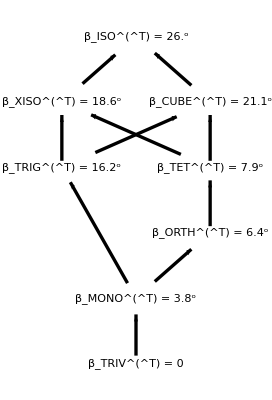

[T] = 1(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

#### BrownAn00 perturbed to its extreme

```mathematica
(*Tmat1=TmatBrownAn00;
Tmat2=Closest[TmatBrownAn00,ISO];
t1=-tpert[TmatBrownAn00];
TmatBrownAn00Pert=(1-t1) Tmat1+t1 Tmat2;*)
TmatBrownAn00Pert=Tpert[TmatBrownAn00,tpertTmat[TmatBrownAn00]+0.01];
```

```mathematica
MatrixNote[TmatBrownAn00Pert]="T is BrownAn00Pert"
MatrixShortNote[TmatBrownAn00Pert]="An00p"
PrintVoigt[TmatBrownAn00Pert]
density[TmatBrownAn00Pert]=density[TmatBrownAn00];
```

T is BrownAn00Pert

An00p

The [T]_𝔹𝔹 matrix is (28.6367 | -7.92 | -23.76 | -15.345 | 18.0047 | -11.7208
-7.92 | 34.9067 | 1.98 | -9.075 | -23.911 | -3.50277
-23.76 | 1.98 | 57.0167 | -9.075 | 10.9552 | -22.4986
-15.345 | -9.075 | -9.075 | 101.402 | 79.4492 | 61.029
18.0047 | -23.911 | 10.9552 | 79.4492 | 192.372 | -30.4904
-11.7208 | -3.50277 | -22.4986 | 61.029 | -30.4904 | 189.267)

The eigenvalues are: {242.384,222.804,71.3223,39.2006,26.8933,0.995638}

The Voigt matrix is (35.7783 | 30.0767 | 27.1067 | 8.085 | -3.795 | -1.485
30.0767 | 227.178 | -14.8033 | -7.26 | -12.87 | -10.56
27.1067 | -14.8033 | 220.083 | -15.18 | 12.375 | -15.51
8.085 | -7.26 | -15.18 | 14.3183 | -3.96 | -11.88
-3.795 | -12.87 | 12.375 | -3.96 | 17.4533 | 0.99
-1.485 | -10.56 | -15.51 | -11.88 | 0.99 | 28.5083)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 213.502   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.678 = 38.87^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

```mathematica
(*cmin=0;cmax=36; dc=3;
contoursMONO[TmatBrownAn00Pert]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn00Pert]=cmax-dc;*)
```

#### Table 2, column An25

```mathematica
CmatBrownAn25=({{87.1, 43.9, 35.4, 6.1, -0.4, -0.6}, {43.9, 174.9, 18., -5.9, -2.9, -6.5}, {35.4, 18., 166.1, -2.9, 4.6, -10.7}, {6.1, -5.9, -2.9, 22.9, -1.3, -5.2}, {-0.4, -2.9, 4.6, -1.3, 29., 0.8}, {-0.6, -6.5, -10.7, -5.2, 0.8, 35.}});
TmatBrownAn25 = TmatOfCmat[CmatBrownAn25];
MatrixNote[TmatBrownAn25]="T is BrownAn25"
MatrixShortNote[TmatBrownAn25]="An25"
PrintVoigt[TmatBrownAn25]
density[TmatBrownAn25]=2653;
```

T is BrownAn25

An25

The [T]_𝔹𝔹 matrix is (45.8 | -2.6 | -10.4 | -12. | 3.4641 | -2.20454
-2.6 | 58. | 1.6 | -2.5 | -7.21688 | 1.06145
-10.4 | 1.6 | 70. | -5.9 | 8.25611 | -14.5336
-12. | -2.5 | -5.9 | 87.1 | 35.3916 | 28.7407
3.4641 | -7.21688 | 8.25611 | 35.3916 | 133.433 | -8.43814
-2.20454 | 1.06145 | -14.5336 | 28.7407 | -8.43814 | 207.567)

The eigenvalues are: {215.82,153.063,72.9576,68.3963,56.5929,35.0705}

The Voigt matrix is (87.1 | 43.9 | 35.4 | 6.1 | -0.4 | -0.6
43.9 | 174.9 | 18. | -5.9 | -2.9 | -6.5
35.4 | 18. | 166.1 | -2.9 | 4.6 | -10.7
6.1 | -5.9 | -2.9 | 22.9 | -1.3 | -5.2
-0.4 | -2.9 | 4.6 | -1.3 | 29. | 0.8
-0.6 | -6.5 | -10.7 | -5.2 | 0.8 | 35.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 101.274   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.356 = 20.4^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (78.8667 | 0. | 0. | 0. | 0. | 0.
0. | 78.8667 | 0. | 0. | 0. | 0.
0. | 0. | 78.8667 | 0. | 0. | 0.
0. | 0. | 0. | 78.8667 | 0. | 0.
0. | 0. | 0. | 0. | 78.8667 | 0.
0. | 0. | 0. | 0. | 0. | 207.567)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 42.9 and μ = 39.4333, bulk modulus κ = 69.1889, Poisson ratio = 0.260526

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn25]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn25]=cmax-dc;*)
```

#### Table 2, column An37

```mathematica
CmatBrownAn37=({{96.2, 46.1, 38.4, 5.9, -0.2, -0.4}, {46.1, 189.4, 15.4, -7., -5.1, -6.8}, {38.4, 15.4, 171.9, 2.2, 7.2, -9.8}, {5.9, -7., 2.2, 23.6, -1.1, -4.8}, {-0.2, -5.1, 7.2, -1.1, 33.1, 1.4}, {-0.4, -6.8, -9.8, -4.8, 1.4, 35.5}});
TmatBrownAn37 = TmatOfCmat[CmatBrownAn37];
MatrixNote[TmatBrownAn37]="T is BrownAn37"
MatrixShortNote[TmatBrownAn37]="An37"
PrintVoigt[TmatBrownAn37]
density[TmatBrownAn37]=2666;
```

T is BrownAn37

An37

The [T]_𝔹𝔹 matrix is (47.2 | -2.2 | -9.6 | -12.9 | -3.17543 | 0.898146
-2.2 | 66.2 | 2.8 | -4.9 | -11.3738 | 1.55134
-9.6 | 2.8 | 71. | -6.4 | 7.15914 | -13.8804
-12.9 | -4.9 | -6.4 | 96.7 | 40.1836 | 28.659
-3.17543 | -11.3738 | 7.15914 | 40.1836 | 141.7 | -4.6669
0.898146 | 1.55134 | -13.8804 | 28.659 | -4.6669 | 219.1)

The eigenvalues are: {227.095,166.063,75.7461,72.0686,62.1546,38.772}

The Voigt matrix is (96.2 | 46.1 | 38.4 | 5.9 | -0.2 | -0.4
46.1 | 189.4 | 15.4 | -7. | -5.1 | -6.8
38.4 | 15.4 | 171.9 | 2.2 | 7.2 | -9.8
5.9 | -7. | 2.2 | 23.6 | -1.1 | -4.8
-0.2 | -5.1 | 7.2 | -1.1 | 33.1 | 1.4
-0.4 | -6.8 | -9.8 | -4.8 | 1.4 | 35.5)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 108.122   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.358 = 20.49^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (84.56 | 0. | 0. | 0. | 0. | 0.
0. | 84.56 | 0. | 0. | 0. | 0.
0. | 0. | 84.56 | 0. | 0. | 0.
0. | 0. | 0. | 84.56 | 0. | 0.
0. | 0. | 0. | 0. | 84.56 | 0.
0. | 0. | 0. | 0. | 0. | 219.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 44.8467 and μ = 42.28, bulk modulus κ = 73.0333, Poisson ratio = 0.257365

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn37]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn37]=cmax-dc;*)
```

#### Table 2, column An48

```mathematica
CmatBrownAn48=({{104.6, 51.5, 43.9, 6.5, 0.1, -0.8}, {51.5, 201.4, 14.5, -2.4, -4.8, -9.9}, {43.9, 14.5, 172.8, -0.4, 6.9, -5.7}, {6.5, -2.4, -0.4, 22.9, -1., -3.8}, {0.1, -4.8, 6.9, -1., 33., 2.1}, {-0.8, -9.9, -5.7, -3.8, 2.1, 35.6}});
TmatBrownAn48 = TmatOfCmat[CmatBrownAn48];
MatrixNote[TmatBrownAn48]="T is BrownAn48"
MatrixShortNote[TmatBrownAn48]="An48"
PrintVoigt[TmatBrownAn48]
density[TmatBrownAn48]=2683;
```

T is BrownAn48

An48

The [T]_𝔹𝔹 matrix is (45.8 | -2. | -7.6 | -8.9 | 2.82902 | 3.02104
-2. | 66. | 4.2 | -4.9 | -10.681 | 1.79629
-7.6 | 4.2 | 71.2 | -9.1 | 0.404145 | -13.3905
-8.9 | -4.9 | -9.1 | 101.5 | 44.9179 | 27.5159
2.82902 | -10.681 | 0.404145 | 44.9179 | 144.433 | 1.17851
3.02104 | 1.79629 | -13.3905 | 27.5159 | 1.17851 | 232.867)

The eigenvalues are: {240.97,170.587,76.3638,72.1154,62.0117,39.7521}

The Voigt matrix is (104.6 | 51.5 | 43.9 | 6.5 | 0.1 | -0.8
51.5 | 201.4 | 14.5 | -2.4 | -4.8 | -9.9
43.9 | 14.5 | 172.8 | -0.4 | 6.9 | -5.7
6.5 | -2.4 | -0.4 | 22.9 | -1. | -3.8
0.1 | -4.8 | 6.9 | -1. | 33. | 2.1
-0.8 | -9.9 | -5.7 | -3.8 | 2.1 | 35.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 112.252   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.356 = 20.41^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (85.7867 | 0. | 0. | 0. | 0. | 0.
0. | 85.7867 | 0. | 0. | 0. | 0.
0. | 0. | 85.7867 | 0. | 0. | 0.
0. | 0. | 0. | 85.7867 | 0. | 0.
0. | 0. | 0. | 0. | 85.7867 | 0.
0. | 0. | 0. | 0. | 0. | 232.867)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.0267 and μ = 42.8933, bulk modulus κ = 77.6222, Poisson ratio = 0.266681

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn48]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn48]=cmax-dc;*)
```

#### Table 2, column An60

```mathematica
CmatBrownAn60=({{109.3, 53.1, 42.1, 7.6, 1.2, -7.7}, {53.1, 185.5, 21.9, -2.9, 0.7, -6.8}, {42.1, 21.9, 164.1, 0.2, 2.5, 0.7}, {7.6, -2.9, 0.2, 22.2, 0.2, 1.4}, {1.2, 0.7, 2.5, 0.2, 33.1, 2.8}, {-7.7, -6.8, 0.7, 1.4, 2.8, 36.8}});
TmatBrownAn60 = TmatOfCmat[CmatBrownAn60];
MatrixNote[TmatBrownAn60]="T is BrownAn60"
MatrixShortNote[TmatBrownAn60]="An60"
PrintVoigt[TmatBrownAn60]
density[TmatBrownAn60]=2702;
```

T is BrownAn60

An60

The [T]_𝔹𝔹 matrix is (44.4 | 0.4 | 2.8 | -10.5 | 2.48261 | 4.00083
0.4 | 66.2 | 5.6 | -0.5 | -1.78979 | 3.59258
2.8 | 5.6 | 73.6 | 0.9 | -9.17987 | -11.2677
-10.5 | -0.5 | 0.9 | 94.3 | 33.6595 | 22.8619
2.48261 | -1.78979 | -9.17987 | 33.6595 | 133.567 | 2.07418
4.00083 | 3.59258 | -11.2677 | 22.8619 | 2.07418 | 231.033)

The eigenvalues are: {236.248,151.495,80.9577,72.0631,62.4015,39.9345}

The Voigt matrix is (109.3 | 53.1 | 42.1 | 7.6 | 1.2 | -7.7
53.1 | 185.5 | 21.9 | -2.9 | 0.7 | -6.8
42.1 | 21.9 | 164.1 | 0.2 | 2.5 | 0.7
7.6 | -2.9 | 0.2 | 22.2 | 0.2 | 1.4
1.2 | 0.7 | 2.5 | 0.2 | 33.1 | 2.8
-7.7 | -6.8 | 0.7 | 1.4 | 2.8 | 36.8)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 93.0792   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.305 = 17.48^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.4133 | 0. | 0. | 0. | 0. | 0.
0. | 82.4133 | 0. | 0. | 0. | 0.
0. | 0. | 82.4133 | 0. | 0. | 0.
0. | 0. | 0. | 82.4133 | 0. | 0.
0. | 0. | 0. | 0. | 82.4133 | 0.
0. | 0. | 0. | 0. | 0. | 231.033)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.54 and μ = 41.2067, bulk modulus κ = 77.0111, Poisson ratio = 0.272958

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn60]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn60]=cmax-dc;*)
```

#### Table 2, column An67

```mathematica
CmatBrownAn67=({{120.3, 54.4, 40.8, 9.2, 2.3, -10.1}, {54.4, 193.5, 16.1, 0.9, 3.1, -2.9}, {40.8, 16.1, 171.9, -0.9, 2.2, -0.3}, {9.2, 0.9, -0.9, 24., 0.7, 0.3}, {2.3, 3.1, 2.2, 0.7, 35.5, 3.2}, {-10.1, -2.9, -0.3, 0.3, 3.2, 37.3}});
TmatBrownAn67 = TmatOfCmat[CmatBrownAn67];
MatrixNote[TmatBrownAn67]="T is BrownAn67"
MatrixShortNote[TmatBrownAn67]="An67"
PrintVoigt[TmatBrownAn67]
density[TmatBrownAn67]=2721;
```

T is BrownAn67

An67

The [T]_𝔹𝔹 matrix is (48. | 1.4 | 0.6 | -8.3 | 6.87047 | 7.51177
1.4 | 71. | 6.4 | 0.8 | 0.57735 | 6.20537
0.6 | 6.4 | 74.6 | 7.2 | -7.15914 | -10.8594
-8.3 | 0.8 | 7.2 | 102.5 | 35.3916 | 19.8
6.87047 | 0.57735 | -7.15914 | 35.3916 | 147.1 | 5.16188
7.51177 | 6.20537 | -10.8594 | 19.8 | 5.16188 | 236.1)

The eigenvalues are: {241.274,164.002,91.3898,75.5333,63.3167,43.7846}

The Voigt matrix is (120.3 | 54.4 | 40.8 | 9.2 | 2.3 | -10.1
54.4 | 193.5 | 16.1 | 0.9 | 3.1 | -2.9
40.8 | 16.1 | 171.9 | -0.9 | 2.2 | -0.3
9.2 | 0.9 | -0.9 | 24. | 0.7 | 0.3
2.3 | 3.1 | 2.2 | 0.7 | 35.5 | 3.2
-10.1 | -2.9 | -0.3 | 0.3 | 3.2 | 37.3)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 100.323   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.315 = 18.027^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (88.64 | 0. | 0. | 0. | 0. | 0.
0. | 88.64 | 0. | 0. | 0. | 0.
0. | 0. | 88.64 | 0. | 0. | 0.
0. | 0. | 0. | 88.64 | 0. | 0.
0. | 0. | 0. | 0. | 88.64 | 0.
0. | 0. | 0. | 0. | 0. | 236.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 49.1533 and μ = 44.32, bulk modulus κ = 78.7, Poisson ratio = 0.262927

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn67]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn67]=cmax-dc;*)
```

#### Table 2, column An78

```mathematica
CmatBrownAn78=({{120.4, 56.6, 49.9, 9., 3.2, -3.}, {56.6, 191.6, 26.3, 2.1, 5.4, -9.9}, {49.9, 26.3, 163.7, 1.7, 1.7, -8.1}, {9., 2.1, 1.7, 23.3, 0.8, 0.9}, {3.2, 5.4, 1.7, 0.8, 32.8, 4.5}, {-3., -9.9, -8.1, 0.9, 4.5, 35.}});
TmatBrownAn78 = TmatOfCmat[CmatBrownAn78];
MatrixNote[TmatBrownAn78]="T is BrownAn78"
MatrixShortNote[TmatBrownAn78]="An78"
PrintVoigt[TmatBrownAn78]
density[TmatBrownAn78]=2725;
```

T is BrownAn78

An78

The [T]_𝔹𝔹 matrix is (46.6 | 1.6 | 1.8 | -6.9 | 4.4456 | 10.4512
1.6 | 65.6 | 9. | 2.2 | 3.00222 | 8.40991
1.8 | 9. | 70. | -6.9 | 1.90526 | -17.1464
-6.9 | 2.2 | -6.9 | 99.4 | 34.1791 | 19.4326
4.4456 | 3.00222 | 1.90526 | 34.1791 | 129.2 | 5.09117
10.4512 | 8.40991 | -17.1464 | 19.4326 | 5.09117 | 247.1)

The eigenvalues are: {252.902,149.465,82.9281,72.7627,56.297,43.5452}

The Voigt matrix is (120.4 | 56.6 | 49.9 | 9. | 3.2 | -3.
56.6 | 191.6 | 26.3 | 2.1 | 5.4 | -9.9
49.9 | 26.3 | 163.7 | 1.7 | 1.7 | -8.1
9. | 2.1 | 1.7 | 23.3 | 0.8 | 0.9
3.2 | 5.4 | 1.7 | 0.8 | 32.8 | 4.5
-3. | -9.9 | -8.1 | 0.9 | 4.5 | 35.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 93.416   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.295 = 16.88^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.16 | 0. | 0. | 0. | 0. | 0.
0. | 82.16 | 0. | 0. | 0. | 0.
0. | 0. | 82.16 | 0. | 0. | 0.
0. | 0. | 0. | 82.16 | 0. | 0.
0. | 0. | 0. | 0. | 82.16 | 0.
0. | 0. | 0. | 0. | 0. | 247.1)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 54.98 and μ = 41.08, bulk modulus κ = 82.3667, Poisson ratio = 0.286175

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn78]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn78]=cmax-dc;*)
```

#### Table 2, column An96

```mathematica
CmatBrownAn96=({{132.2, 64., 55.3, 9.5, 5.1, -10.8}, {64., 200.2, 31.9, 7.5, 3.5, -7.2}, {55.3, 31.9, 163.9, 6.6, 0.5, 1.6}, {9.5, 7.5, 6.6, 24.6, 3., -2.2}, {5.1, 3.5, 0.5, 3., 36.6, 5.2}, {-10.8, -7.2, 1.6, -2.2, 5.2, 36.}});
TmatBrownAn96 = TmatOfCmat[CmatBrownAn96];
MatrixNote[TmatBrownAn96]="T is BrownAn96"
MatrixShortNote[TmatBrownAn96]="An96"
PrintVoigt[TmatBrownAn96]
density[TmatBrownAn96]=2757;
```

T is BrownAn96

An96

The [T]_𝔹𝔹 matrix is (49.2 | 6. | -4.4 | -2. | 2.19393 | 19.2693
6. | 73.2 | 10.4 | -1.6 | 4.38786 | 7.43012
-4.4 | 10.4 | 72. | 3.6 | -12.2398 | -13.3905
-2. | -1.6 | 3.6 | 102.2 | 33.1399 | 18.2079
2.19393 | 4.38786 | -12.2398 | 33.1399 | 127.867 | 10.7009
19.2693 | 7.43012 | -13.3905 | 18.2079 | 10.7009 | 266.233)

The eigenvalues are: {272.65,148.053,87.1567,80.6492,57.098,45.0931}

The Voigt matrix is (132.2 | 64. | 55.3 | 9.5 | 5.1 | -10.8
64. | 200.2 | 31.9 | 7.5 | 3.5 | -7.2
55.3 | 31.9 | 163.9 | 6.6 | 0.5 | 1.6
9.5 | 7.5 | 6.6 | 24.6 | 3. | -2.2
5.1 | 3.5 | 0.5 | 3. | 36.6 | 5.2
-10.8 | -7.2 | 1.6 | -2.2 | 5.2 | 36.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 93.4734   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.278 = 15.95^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (84.8933 | 0. | 0. | 0. | 0. | 0.
0. | 84.8933 | 0. | 0. | 0. | 0.
0. | 0. | 84.8933 | 0. | 0. | 0.
0. | 0. | 0. | 84.8933 | 0. | 0.
0. | 0. | 0. | 0. | 84.8933 | 0.
0. | 0. | 0. | 0. | 0. | 266.233)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 60.4467 and μ = 42.4467, bulk modulus κ = 88.7444, Poisson ratio = 0.293735

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn96]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn96]=cmax-dc;*)
```

## Brown and Abramson (2016) maps

#### Table 3, Sample 1

```mathematica
CmatBrownAbramson2016s1=({{119.2, 47.5, 41.2, 0, -1.7, 0}, {47.5, 182.2, 58.2, 0, -5.6, 0}, {41.2, 58.2, 228.0, 0, -30.6, 0}, {0, 0, 0, 75.6, 0, 4.7}, {-1.7, -5.6, -30.6, 0, 45.9, 0}, {0, 0, 0, 4.7, 0, 49.2}});
TmatBrownAbramson2016s1= TmatOfCmat[CmatBrownAbramson2016s1];
MatrixNote[TmatBrownAbramson2016s1]="T is BrownAbramson1"
MatrixShortNote[TmatBrownAbramson2016s1]="BA1"
PrintVoigt[TmatBrownAbramson2016s1]
density[TmatBrownAbramson2016s1]=3027;
```

T is BrownAbramson1

BA1

The [T]_𝔹𝔹 matrix is (151.2 | 0 | 9.4 | 0 | 0 | 0
0 | 91.8 | 0 | -3.9 | 31.1192 | -30.9452
9.4 | 0 | 98.4 | 0 | 0 | 0
0 | -3.9 | 0 | 103.2 | 8.37158 | 32.6599
0 | 31.1192 | 0 | 8.37158 | 151.8 | -37.4767
0 | -30.9452 | 0 | 32.6599 | -37.4767 | 274.4)

The eigenvalues are: {296.712,153.54,152.824,96.7764,94.3306,76.6176}

The Voigt matrix is (119.2 | 47.5 | 41.2 | 0 | -1.7 | 0
47.5 | 182.2 | 58.2 | 0 | -5.6 | 0
41.2 | 58.2 | 228. | 0 | -30.6 | 0
0 | 0 | 0 | 75.6 | 0 | 4.7
-1.7 | -5.6 | -30.6 | 0 | 45.9 | 0
0 | 0 | 0 | 4.7 | 0 | 49.2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 112.551   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.286 = 16.39^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (119.28 | 0. | 0. | 0. | 0. | 0.
0. | 119.28 | 0. | 0. | 0. | 0.
0. | 0. | 119.28 | 0. | 0. | 0.
0. | 0. | 0. | 119.28 | 0. | 0.
0. | 0. | 0. | 0. | 119.28 | 0.
0. | 0. | 0. | 0. | 0. | 274.4)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 51.7067 and μ = 59.64, bulk modulus κ = 91.4667, Poisson ratio = 0.232188

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAbramson2016s1]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s1]=cmax-dc;*)
```

#### rotation matrix from MSAT MS_axes()

```mathematica
RfromMSATBrownAbramson2016s1=({{0.971758767912463, 0, 0.235976475491204}, {0, 1, 0}, {-0.235976475491204, 0, 0.971758767912464}}); 
UfromMSATBrownAbramson2016s1 =Transpose[RfromMSATBrownAbramson2016s1];
```

#### Table 3, Sample 2

```mathematica
CmatBrownAbramson2016s2=({{122.7, 50.0, 44.3, 0, -1.4, 0}, {50.0, 184.6, 59.5, 0, -7.1, 0}, {44.3, 59.5, 223.7, 0, -29.4, 0}, {0, 0, 0, 70.5, 0, 5.3}, {-1.4, -7.1, -29.4, 0, 42.5, 0}, {0, 0, 0, 5.3, 0, 45.9}});
TmatBrownAbramson2016s2= TmatOfCmat[CmatBrownAbramson2016s2];
MatrixNote[TmatBrownAbramson2016s2]="T is BrownAbramson2"
MatrixShortNote[TmatBrownAbramson2016s2]="BA2"
PrintVoigt[TmatBrownAbramson2016s2]
density[TmatBrownAbramson2016s2]=3255;
```

T is BrownAbramson2

BA2

The [T]_𝔹𝔹 matrix is (141. | 0 | 10.6 | 0 | 0 | 0
0 | 85. | 0 | -5.7 | 29.0407 | -30.9452
10.6 | 0 | 91.8 | 0 | 0 | 0
0 | -5.7 | 0 | 103.65 | 9.09327 | 31.4759
0 | 29.0407 | 0 | 9.09327 | 147.817 | -33.9176
0 | -30.9452 | 0 | 31.4759 | -33.9176 | 279.533)

The eigenvalues are: {298.592,150.718,143.187,95.7109,89.6134,70.9795}

The Voigt matrix is (122.7 | 50. | 44.3 | 0 | -1.4 | 0
50. | 184.6 | 59.5 | 0 | -7.1 | 0
44.3 | 59.5 | 223.7 | 0 | -29.4 | 0
0 | 0 | 0 | 70.5 | 0 | 5.3
-1.4 | -7.1 | -29.4 | 0 | 42.5 | 0
0 | 0 | 0 | 5.3 | 0 | 45.9)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 107.948   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.278 = 15.93^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (113.853 | 0. | 0. | 0. | 0. | 0.
0. | 113.853 | 0. | 0. | 0. | 0.
0. | 0. | 113.853 | 0. | 0. | 0.
0. | 0. | 0. | 113.853 | 0. | 0.
0. | 0. | 0. | 0. | 113.853 | 0.
0. | 0. | 0. | 0. | 0. | 279.533)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 55.2267 and μ = 56.9267, bulk modulus κ = 93.1778, Poisson ratio = 0.246211

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s2]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s2]=cmax-dc;*)
```

#### Table 3, Sample 3

```mathematica
CmatBrownAbramson2016s3=({{133.6, 50.9, 43.1, 0, -0.8, 0}, {50.9, 193.4, 58.3, 0, -10.8, 0}, {43.1, 58.3, 225.8, 0, -30.3, 0}, {0, 0, 0, 75.5, 0, 3.8}, {-0.8, -10.8, -30.3, 0, 47.5, 0}, {0, 0, 0, 3.8, 0, 50.4}});
TmatBrownAbramson2016s3= TmatOfCmat[CmatBrownAbramson2016s3];
MatrixNote[TmatBrownAbramson2016s3]="T is BrownAbramson3"
MatrixShortNote[TmatBrownAbramson2016s3]="BA3"
PrintVoigt[TmatBrownAbramson2016s3]
density[TmatBrownAbramson2016s3]=3162;
```

T is BrownAbramson3

BA3

The [T]_𝔹𝔹 matrix is (151. | 0 | 7.6 | 0 | 0 | 0
0 | 95. | 0 | -10. | 28.2902 | -34.2112
7.6 | 0 | 100.8 | 0 | 0 | 0
0 | -10. | 0 | 112.6 | 8.48705 | 30.6186
0 | 28.2902 | 0 | 8.48705 | 154.4 | -29.2742
0 | -34.2112 | 0 | 30.6186 | -29.2742 | 285.8)

The eigenvalues are: {304.178,157.799,152.125,107.222,99.6746,78.6013}

The Voigt matrix is (133.6 | 50.9 | 43.1 | 0 | -0.8 | 0
50.9 | 193.4 | 58.3 | 0 | -10.8 | 0
43.1 | 58.3 | 225.8 | 0 | -30.3 | 0
0 | 0 | 0 | 75.5 | 0 | 3.8
-0.8 | -10.8 | -30.3 | 0 | 47.5 | 0
0 | 0 | 0 | 3.8 | 0 | 50.4)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 105.568   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.26 = 14.92^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (122.76 | 0. | 0. | 0. | 0. | 0.
0. | 122.76 | 0. | 0. | 0. | 0.
0. | 0. | 122.76 | 0. | 0. | 0.
0. | 0. | 0. | 122.76 | 0. | 0.
0. | 0. | 0. | 0. | 122.76 | 0.
0. | 0. | 0. | 0. | 0. | 285.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 54.3467 and μ = 61.38, bulk modulus κ = 95.2667, Poisson ratio = 0.234806

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s3]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s3]=cmax-dc;*)
```

#### Table 3, Sample 4

```mathematica
CmatBrownAbramson2016s4=({{122.8, 51.8, 45.9, 0, -0.7, 0}, {51.8, 189.3, 62.3, 0, -7.0, 0}, {45.9, 62.3, 222.9, 0, -30.0, 0}, {0, 0, 0, 71.5, 0, 5.4}, {-0.7, -7.0, -30.0, 0, 46.8, 0}, {0, 0, 0, 5.4, 0, 46.2}});
TmatBrownAbramson2016s4= TmatOfCmat[CmatBrownAbramson2016s4];
MatrixNote[TmatBrownAbramson2016s4]="T is BrownAbramson4"
MatrixShortNote[TmatBrownAbramson2016s4]="BA4"
PrintVoigt[TmatBrownAbramson2016s4]
density[TmatBrownAbramson2016s4]=3293;
```

T is BrownAbramson4

BA4

The [T]_𝔹𝔹 matrix is (143. | 0 | 10.8 | 0 | 0 | 0
0 | 93.6 | 0 | -6.3 | 30.1954 | -30.7819
10.8 | 0 | 92.4 | 0 | 0 | 0
0 | -6.3 | 0 | 104.25 | 9.72835 | 33.8438
0 | 30.1954 | 0 | 9.72835 | 145.75 | -32.5976
0 | -30.7819 | 0 | 33.8438 | -32.5976 | 285.)

The eigenvalues are: {303.783,151.769,145.209,96.7565,90.1913,76.2908}

The Voigt matrix is (122.8 | 51.8 | 45.9 | 0 | -0.7 | 0
51.8 | 189.3 | 62.3 | 0 | -7. | 0
45.9 | 62.3 | 222.9 | 0 | -30. | 0
0 | 0 | 0 | 71.5 | 0 | 5.4
-0.7 | -7. | -30. | 0 | 46.8 | 0
0 | 0 | 0 | 5.4 | 0 | 46.2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 106.991   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.271 = 15.53^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (115.8 | 0. | 0. | 0. | 0. | 0.
0. | 115.8 | 0. | 0. | 0. | 0.
0. | 0. | 115.8 | 0. | 0. | 0.
0. | 0. | 0. | 115.8 | 0. | 0.
0. | 0. | 0. | 0. | 115.8 | 0.
0. | 0. | 0. | 0. | 0. | 285.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 56.4 and μ = 57.9, bulk modulus κ = 95., Poisson ratio = 0.246719

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s4]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s4]=cmax-dc;*)
```

#### Table 3, Sample 5

```mathematica
CmatBrownAbramson2016s5=({{108.6, 48.4, 37.7, 0, 1.0, 0}, {48.4, 191.6, 59.2, 0, -5.6, 0}, {37.7, 59.2, 230.8, 0, -29.6, 0}, {0, 0, 0, 77.0, 0, 7.9}, {1.0, -5.6, -29.6, 0, 50.0, 0}, {0, 0, 0, 7.9, 0, 48.6}});
TmatBrownAbramson2016s5= TmatOfCmat[CmatBrownAbramson2016s5];
MatrixNote[TmatBrownAbramson2016s5]="T is BrownAbramson5"
MatrixShortNote[TmatBrownAbramson2016s5]="BA5"
PrintVoigt[TmatBrownAbramson2016s5]
density[TmatBrownAbramson2016s5]=3038;
```

T is BrownAbramson5

BA5

The [T]_𝔹𝔹 matrix is (154. | 0 | 15.8 | 0 | 0 | 0
0 | 100. | 0 | -6.6 | 31.5233 | -27.9242
15.8 | 0 | 97.2 | 0 | 0 | 0
0 | -6.6 | 0 | 101.7 | 11.547 | 42.6619
0 | 31.5233 | 0 | 11.547 | 155.433 | -38.0659
0 | -27.9242 | 0 | 42.6619 | -38.0659 | 273.867)

The eigenvalues are: {299.099,159.987,158.099,93.4067,93.1008,78.5076}

The Voigt matrix is (108.6 | 48.4 | 37.7 | 0 | 1. | 0
48.4 | 191.6 | 59.2 | 0 | -5.6 | 0
37.7 | 59.2 | 230.8 | 0 | -29.6 | 0
0 | 0 | 0 | 77. | 0 | 7.9
1. | -5.6 | -29.6 | 0 | 50. | 0
0 | 0 | 0 | 7.9 | 0 | 48.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 120.791   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.303 = 17.38^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (121.667 | 0. | 0. | 0. | 0. | 0.
0. | 121.667 | 0. | 0. | 0. | 0.
0. | 0. | 121.667 | 0. | 0. | 0.
0. | 0. | 0. | 121.667 | 0. | 0.
0. | 0. | 0. | 0. | 121.667 | 0.
0. | 0. | 0. | 0. | 0. | 273.867)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 50.7333 and μ = 60.8333, bulk modulus κ = 91.2889, Poisson ratio = 0.227368

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAbramson2016s5]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s5]=cmax-dc;*)
```

#### Table 3, Sample 6

```mathematica
CmatBrownAbramson2016s6=({{131.1, 53.2, 47.2, 0, -1.0, 0}, {53.2, 186.6, 60.3, 0, -8.5, 0}, {47.2, 60.3, 224.3, 0, -30.3, 0}, {0, 0, 0, 72.5, 0, 4.4}, {-1.0, -8.5, -30.3, 0, 46.5, 0}, {0, 0, 0, 4.4, 0, 48.0}});
TmatBrownAbramson2016s6= TmatOfCmat[CmatBrownAbramson2016s6];
MatrixNote[TmatBrownAbramson2016s6]="T is BrownAbramson6"
MatrixShortNote[TmatBrownAbramson2016s6]="BA6"
PrintVoigt[TmatBrownAbramson2016s6]
density[TmatBrownAbramson2016s6]=3213;
```

T is BrownAbramson6

BA6

The [T]_𝔹𝔹 matrix is (145. | 0 | 8.8 | 0 | 0 | 0
0 | 93. | 0 | -7.5 | 29.5026 | -32.4966
8.8 | 0 | 96. | 0 | 0 | 0
0 | -7.5 | 0 | 105.65 | 8.45818 | 28.0058
0 | 29.5026 | 0 | 8.45818 | 148.55 | -31.1127
0 | -32.4966 | 0 | 28.0058 | -31.1127 | 287.8)

The eigenvalues are: {304.91,152.645,146.532,101.091,94.4675,76.3541}

The Voigt matrix is (131.1 | 53.2 | 47.2 | 0 | -1. | 0
53.2 | 186.6 | 60.3 | 0 | -8.5 | 0
47.2 | 60.3 | 224.3 | 0 | -30.3 | 0
0 | 0 | 0 | 72.5 | 0 | 4.4
-1. | -8.5 | -30.3 | 0 | 46.5 | 0
0 | 0 | 0 | 4.4 | 0 | 48.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 103.398   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.259 = 14.85^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (117.64 | 0. | 0. | 0. | 0. | 0.
0. | 117.64 | 0. | 0. | 0. | 0.
0. | 0. | 117.64 | 0. | 0. | 0.
0. | 0. | 0. | 117.64 | 0. | 0.
0. | 0. | 0. | 0. | 117.64 | 0.
0. | 0. | 0. | 0. | 0. | 287.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 56.72 and μ = 58.82, bulk modulus κ = 95.9333, Poisson ratio = 0.245456

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s6]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s6]=cmax-dc;*)
```

#### Table 3, Sample 7

```mathematica
CmatBrownAbramson2016s7=({{122.7, 52.6, 47.5, 0, -2.0, 0}, {52.6, 178.6, 60.8, 0, -9.5, 0}, {47.5, 60.8, 216.6, 0, -31.0, 0}, {0, 0, 0, 67.5, 0, 6.3}, {-2.0, -9.5, -31.0, 0, 39.7, 0}, {0, 0, 0, 6.3, 0, 40.8}});
TmatBrownAbramson2016s7= TmatOfCmat[CmatBrownAbramson2016s7];
MatrixNote[TmatBrownAbramson2016s7]="T is BrownAbramson7"
MatrixShortNote[TmatBrownAbramson2016s7]="BA7"
PrintVoigt[TmatBrownAbramson2016s7]
density[TmatBrownAbramson2016s7]=3418;
```

T is BrownAbramson7

BA7

The [T]_𝔹𝔹 matrix is (135. | 0 | 12.6 | 0 | 0 | 0
0 | 79.4 | 0 | -7.5 | 29.1562 | -34.7011
12.6 | 0 | 81.6 | 0 | 0 | 0
0 | -7.5 | 0 | 98.05 | 8.45818 | 28.2508
0 | 29.1562 | 0 | 8.45818 | 139.95 | -31.8198
0 | -34.7011 | 0 | 28.2508 | -31.8198 | 279.9)

The eigenvalues are: {297.882,143.07,137.824,92.4646,78.7763,63.8838}

The Voigt matrix is (122.7 | 52.6 | 47.5 | 0 | -2. | 0
52.6 | 178.6 | 60.8 | 0 | -9.5 | 0
47.5 | 60.8 | 216.6 | 0 | -31. | 0
0 | 0 | 0 | 67.5 | 0 | 6.3
-2. | -9.5 | -31. | 0 | 39.7 | 0
0 | 0 | 0 | 6.3 | 0 | 40.8)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 107.978   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.285 = 16.36^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (106.8 | 0. | 0. | 0. | 0. | 0.
0. | 106.8 | 0. | 0. | 0. | 0.
0. | 0. | 106.8 | 0. | 0. | 0.
0. | 0. | 0. | 106.8 | 0. | 0.
0. | 0. | 0. | 0. | 106.8 | 0.
0. | 0. | 0. | 0. | 0. | 279.9)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 57.7 and μ = 53.4, bulk modulus κ = 93.3, Poisson ratio = 0.259676

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s7]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s7]=cmax-dc;*)
```

#### Table 3, Sample 8

```mathematica
CmatBrownAbramson2016s8=({{141.6, 57.1, 49.6, 0, -0.2, 0}, {57.1, 197.8, 60.9, 0, -10.9, 0}, {49.6, 60.9, 225.4, 0, -31.4, 0}, {0, 0, 0, 75.8, 0, 3.3}, {-0.2, -10.9, -31.4, 0, 49.9, 0}, {0, 0, 0, 3.3, 0, 51.7}});
TmatBrownAbramson2016s8= TmatOfCmat[CmatBrownAbramson2016s8];
MatrixNote[TmatBrownAbramson2016s8]="T is BrownAbramson8"
MatrixShortNote[TmatBrownAbramson2016s8]="BA8"
PrintVoigt[TmatBrownAbramson2016s8]
density[TmatBrownAbramson2016s8]=3163;
```

T is BrownAbramson8

BA8

The [T]_𝔹𝔹 matrix is (151.6 | 0 | 6.6 | 0 | 0 | 0
0 | 99.8 | 0 | -10.7 | 29.849 | -34.7011
6.6 | 0 | 103.4 | 0 | 0 | 0
0 | -10.7 | 0 | 112.6 | 9.69948 | 27.5568
0 | 29.849 | 0 | 9.69948 | 152.2 | -25.3851
0 | -34.7011 | 0 | 27.5568 | -25.3851 | 300.)

The eigenvalues are: {315.144,159.23,152.487,110.204,102.513,80.0215}

The Voigt matrix is (141.6 | 57.1 | 49.6 | 0 | -0.2 | 0
57.1 | 197.8 | 60.9 | 0 | -10.9 | 0
49.6 | 60.9 | 225.4 | 0 | -31.4 | 0
0 | 0 | 0 | 75.8 | 0 | 3.3
-0.2 | -10.9 | -31.4 | 0 | 49.9 | 0
0 | 0 | 0 | 3.3 | 0 | 51.7)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 100.99   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.242 = 13.89^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (123.92 | 0. | 0. | 0. | 0. | 0.
0. | 123.92 | 0. | 0. | 0. | 0.
0. | 0. | 123.92 | 0. | 0. | 0.
0. | 0. | 0. | 123.92 | 0. | 0.
0. | 0. | 0. | 0. | 123.92 | 0.
0. | 0. | 0. | 0. | 0. | 300.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 58.6933 and μ = 61.96, bulk modulus κ = 100., Poisson ratio = 0.243231

```mathematica
(*cmin=0;cmax=12; dc=1;
contoursMONO[TmatBrownAbramson2016s8]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s8]=cmax-dc;*)
```

#### Table 3, Sample 9

```mathematica
CmatBrownAbramson2016s9=({{148.7, 56.5, 48.8, 0, 0.3, 0}, {56.5, 204.6, 61.9, 0, -6.9, 0}, {48.8, 61.9, 232.1, 0, -28.8, 0}, {0, 0, 0, 76.7, 0, 1.9}, {0.3, -6.9, -28.8, 0, 54.1, 0}, {0, 0, 0, 1.9, 0, 52.9}});
TmatBrownAbramson2016s9= TmatOfCmat[CmatBrownAbramson2016s9];
MatrixNote[TmatBrownAbramson2016s9]="T is BrownAbramson9"
MatrixShortNote[TmatBrownAbramson2016s9]="BA9"
PrintVoigt[TmatBrownAbramson2016s9]
density[TmatBrownAbramson2016s9]=3190;
```

T is BrownAbramson9

BA9

The [T]_𝔹𝔹 matrix is (153.4 | 0 | 3.8 | 0 | 0 | 0
0 | 108.2 | 0 | -7.2 | 29.4449 | -28.904
3.8 | 0 | 105.8 | 0 | 0 | 0
0 | -7.2 | 0 | 120.15 | 8.57365 | 28.1691
0 | 29.4449 | 0 | 8.57365 | 158.65 | -25.5973
0 | -28.904 | 0 | 28.1691 | -25.5973 | 306.6)

The eigenvalues are: {319.982,166.428,153.701,116.23,105.499,90.9605}

The Voigt matrix is (148.7 | 56.5 | 48.8 | 0 | 0.3 | 0
56.5 | 204.6 | 61.9 | 0 | -6.9 | 0
48.8 | 61.9 | 232.1 | 0 | -28.8 | 0
0 | 0 | 0 | 76.7 | 0 | 1.9
0.3 | -6.9 | -28.8 | 0 | 54.1 | 0
0 | 0 | 0 | 1.9 | 0 | 52.9)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 95.4217   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.223 = 12.76^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (129.24 | 0. | 0. | 0. | 0. | 0.
0. | 129.24 | 0. | 0. | 0. | 0.
0. | 0. | 129.24 | 0. | 0. | 0.
0. | 0. | 0. | 129.24 | 0. | 0.
0. | 0. | 0. | 0. | 129.24 | 0.
0. | 0. | 0. | 0. | 0. | 306.6)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 59.12 and μ = 64.62, bulk modulus κ = 102.2, Poisson ratio = 0.238888

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatBrownAbramson2016s9]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s9]=cmax-dc;*)
```

## Aminzadeh et al. (2022) maps

#### Bukov gneiss: Table 3, 0.1 MPa pressure (column 1)

```mathematica
CmatAminzadehBukov0p1=({{89.90, 27.02, 14.85, 0.41, -0.51, -1.06}, {27.02, 78.88, 16.66, 0.05, 3.78, -0.02}, {14.85, 16.66, 45.05, -0.91, -0.55, 3.08}, {0.41, 0.05, -0.91, 19.68, -0.93, -1.66}, {-0.51, 3.78, -0.55, -0.93, 21.79, 1.11}, {-1.06, -0.02, 3.08, -1.66, 1.11, 28.55}});
TmatAminzadehBukov0p1= TmatOfCmat[CmatAminzadehBukov0p1];
MatrixNote[TmatAminzadehBukov0p1]="T is Aminzadeh-Bukov-0.1"
MatrixShortNote[TmatAminzadehBukov0p1]="BUK"
PrintVoigt[TmatAminzadehBukov0p1]
density[TmatAminzadehBukov0p1]=2750;
```

T is Aminzadeh-Bukov-0.1

BUK

The [T]_𝔹𝔹 matrix is (39.36 | -1.86 | -3.32 | -0.36 | 1.31636 | -0.367423
-1.86 | 43.58 | 2.22 | 4.29 | 2.52302 | 2.22087
-3.32 | 2.22 | 57.1 | 1.04 | -4.18002 | 1.63299
-0.36 | 4.29 | 1.04 | 57.37 | -4.2262 | -3.75997
1.31636 | 2.52302 | -4.18002 | -4.2262 | 46.1633 | 23.8554
-0.367423 | 2.22087 | 1.63299 | -3.75997 | 23.8554 | 110.297)

The eigenvalues are: {118.677,60.9115,56.5079,43.4662,38.8294,35.4776}

The Voigt matrix is (89.9 | 27.02 | 14.85 | 0.41 | -0.51 | -1.06
27.02 | 78.88 | 16.66 | 0.05 | 3.78 | -0.02
14.85 | 16.66 | 45.05 | -0.91 | -0.55 | 3.08
0.41 | 0.05 | -0.91 | 19.68 | -0.93 | -1.66
-0.51 | 3.78 | -0.55 | -0.93 | 21.79 | 1.11
-1.06 | -0.02 | 3.08 | -1.66 | 1.11 | 28.55)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 40.1551   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.253 = 14.52^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (48.7147 | 0. | 0. | 0. | 0. | 0.
0. | 48.7147 | 0. | 0. | 0. | 0.
0. | 0. | 48.7147 | 0. | 0. | 0.
0. | 0. | 0. | 48.7147 | 0. | 0.
0. | 0. | 0. | 0. | 48.7147 | 0.
0. | 0. | 0. | 0. | 0. | 110.297)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 20.5273 and μ = 24.3573, bulk modulus κ = 36.7656, Poisson ratio = 0.228668

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatAminzadehBukov0p1]=Range[cmin,cmax,dc];
MaxForScaling[TmatAminzadehBukov0p1]=cmax-dc;*)
```

#### Grimsel granite: Table 4, 0.1 MPa pressure (column 1)

```mathematica
CmatAminzadehGrimsel0p1=({{48.16, 19.34, 13.23, -1.18, 0.06, -0.30}, {19.34, 44.60, 10.81, 0.53, -1.70, 0.43}, {13.23, 10.81, 23.07, -0.29, 0.36, -0.98}, {-1.18, 0.53, -0.29, 10.63, 0.73, 0.85}, {0.06, -1.70, 0.36, 0.73, 7.67, 0.70}, {-0.30, 0.43, -0.98, 0.85, 0.70, 13.85}});
TmatAminzadehGrimsel0p1= TmatOfCmat[CmatAminzadehGrimsel0p1];
MatrixNote[TmatAminzadehGrimsel0p1]="T is Aminzadeh-Grimsel-0.1"
MatrixShortNote[TmatAminzadehGrimsel0p1]="GRM"
PrintVoigt[TmatAminzadehGrimsel0p1]
density[TmatAminzadehGrimsel0p1]=2700;
```

T is Aminzadeh-Grimsel-0.1

GRM

The [T]_𝔹𝔹 matrix is (21.26 | 1.46 | 1.7 | 1.71 | -0.0404145 | -0.767507
1.46 | 15.34 | 1.4 | -1.76 | -1.36255 | -1.04512
1.7 | 1.4 | 27.7 | 0.73 | 1.20666 | -0.694022
1.71 | -1.76 | 0.73 | 27.04 | 0.369504 | -2.44132
-0.0404145 | -1.36255 | 1.20666 | 0.369504 | 21.26 | 14.4391
-0.767507 | -1.04512 | -0.694022 | -2.44132 | 14.4391 | 67.53)

The eigenvalues are: {71.8275,29.0811,26.971,20.9293,17.1381,14.183}

The Voigt matrix is (48.16 | 19.34 | 13.23 | -1.18 | 0.06 | -0.3
19.34 | 44.6 | 10.81 | 0.53 | -1.7 | 0.43
13.23 | 10.81 | 23.07 | -0.29 | 0.36 | -0.98
-1.18 | 0.53 | -0.29 | 10.63 | 0.73 | 0.85
0.06 | -1.7 | 0.36 | 0.73 | 7.67 | 0.7
-0.3 | 0.43 | -0.98 | 0.85 | 0.7 | 13.85)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 23.8576   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.276 = 15.81^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (22.52 | 0. | 0. | 0. | 0. | 0.
0. | 22.52 | 0. | 0. | 0. | 0.
0. | 0. | 22.52 | 0. | 0. | 0.
0. | 0. | 0. | 22.52 | 0. | 0.
0. | 0. | 0. | 0. | 22.52 | 0.
0. | 0. | 0. | 0. | 0. | 67.53)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 15.0033 and μ = 11.26, bulk modulus κ = 22.51, Poisson ratio = 0.285633

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatAminzadehGrimsel0p1]=Range[cmin,cmax,dc];
MaxForScaling[TmatAminzadehGrimsel0p1]=cmax-dc;*)
```

## List of maps

#### Browaeys and Chevrot (2004) - olivine

```mathematica
CmatBColivine=1.({{192, 66, 60, 0, 0, 0}, {66, 160, 56, 0, 0, 0}, {60, 56, 272, 0, 0, 0}, {0, 0, 0, 60, 0, 0}, {0, 0, 0, 0, 62, 0}, {0, 0, 0, 0, 0, 49}});
TmatBColivine = TmatOfCmat[CmatBColivine];
MatrixNote[TmatBColivine]="T is BColivine"
MatrixShortNote[TmatBColivine]="BCO"
PrintVoigt[TmatBColivine]
```

T is BColivine

BCO

The [T]_𝔹𝔹 matrix is (120. | 0 | 0 | 0 | 0 | 0
0 | 124. | 0 | 0 | 0 | 0
0 | 0 | 98. | 0 | 0 | 0
0 | 0 | 0 | 110. | -6.9282 | -14.6969
0 | 0 | 0 | -6.9282 | 184.667 | -41.4836
0 | 0 | 0 | -14.6969 | -41.4836 | 329.333)

The eigenvalues are: {341.054,175.274,124.,120.,107.672,98.}

The Voigt matrix is (192. | 66. | 60. | 0 | 0 | 0
66. | 160. | 56. | 0 | 0 | 0
60. | 56. | 272. | 0 | 0 | 0
0 | 0 | 0 | 60. | 0 | 0
0 | 0 | 0 | 0 | 62. | 0
0 | 0 | 0 | 0 | 0 | 49.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 92.1014   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.208 = 11.95^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (127.333 | 0. | 0. | 0. | 0. | 0.
0. | 127.333 | 0. | 0. | 0. | 0.
0. | 0. | 127.333 | 0. | 0. | 0.
0. | 0. | 0. | 127.333 | 0. | 0.
0. | 0. | 0. | 0. | 127.333 | 0.
0. | 0. | 0. | 0. | 0. | 329.333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 67.3333 and μ = 63.6667, bulk modulus κ = 109.778, Poisson ratio = 0.256997

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatBColivine]=Range[cmin,cmax,dc];
MaxForScaling[TmatBColivine]=cmax-dc;*)
```

#### lattice for TmatBColivine:

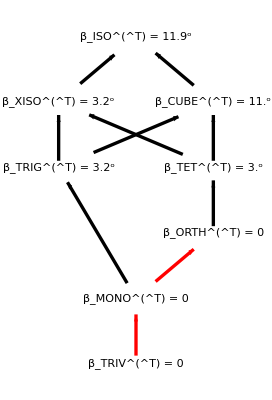

#### Browaeys and Chevrot (2004) - enstatite

```mathematica
CmatBCenstatite=1.({{225, 54, 72, 0, 0, 0}, {54, 214, 53, 0, 0, 0}, {72, 53, 178, 0, 0, 0}, {0, 0, 0, 78, 0, 0}, {0, 0, 0, 0, 82, 0}, {0, 0, 0, 0, 0, 76}});
TmatBCenstatite = TmatOfCmat[CmatBCenstatite];
MatrixNote[TmatBCenstatite]="T is BCenstatite"
MatrixShortNote[TmatBCenstatite]="BCE"
PrintVoigt[TmatBCenstatite]
```

T is BCenstatite

BCE

The [T]_𝔹𝔹 matrix is (156. | 0 | 0 | 0 | 0 | 0
0 | 164. | 0 | 0 | 0 | 0
0 | 0 | 152. | 0 | 0 | 0
0 | 0 | 0 | 165.5 | 7.79423 | -12.2474
0 | 0 | 0 | 7.79423 | 126.5 | 15.5563
0 | 0 | 0 | -12.2474 | 15.5563 | 325.)

The eigenvalues are: {327.047,166.502,164.,156.,152.,123.45}

The Voigt matrix is (225. | 54. | 72. | 0 | 0 | 0
54. | 214. | 53. | 0 | 0 | 0
72. | 53. | 178. | 0 | 0 | 0
0 | 0 | 0 | 78. | 0 | 0
0 | 0 | 0 | 0 | 82. | 0
0 | 0 | 0 | 0 | 0 | 76.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 43.5293   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.092 = 5.27^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (152.8 | 0. | 0. | 0. | 0. | 0.
0. | 152.8 | 0. | 0. | 0. | 0.
0. | 0. | 152.8 | 0. | 0. | 0.
0. | 0. | 0. | 152.8 | 0. | 0.
0. | 0. | 0. | 0. | 152.8 | 0.
0. | 0. | 0. | 0. | 0. | 325.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 57.4 and μ = 76.4, bulk modulus κ = 108.333, Poisson ratio = 0.214499

```mathematica
(*cmin=0;cmax=4.5; dc=0.5;
contoursMONO[TmatBCenstatite]=Range[cmin,cmax,dc];
MaxForScaling[TmatBCenstatite]=cmax-dc;*)
```

#### lattice for TmatBCenstatite:

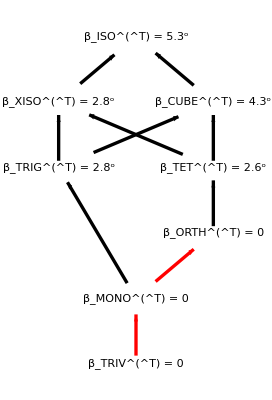

#### Igel, Mora, Riollet (1995) [units of 10^11 dyne/cm^2 = 10^10 N/m^2= 10 GPa; 1 dyne/cm^2 = 0.1 N/m^2] We multiply by 10 to put these in units of GPa.

```mathematica
CmatIgel=10({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
TmatIgel = TmatOfCmat[CmatIgel];
MatrixNote[TmatIgel]="T is Igel"
MatrixShortNote[TmatIgel]="Igel"
PrintVoigt[TmatIgel]
density[TmatIgel]=1000;
```

T is Igel

Igel

The [T]_𝔹𝔹 matrix is (100. | 7. | 10.5 | 52. | -39.2598 | -31.0269
7. | 80. | -20. | -2. | -4.6188 | 3.26599
10.5 | -20. | 60. | -4.5 | -1.90526 | 3.18434
52. | -2. | -4.5 | 55. | 0 | -12.2474
-39.2598 | -4.6188 | -1.90526 | 0 | 55. | 21.2132
-31.0269 | 3.26599 | 3.18434 | -12.2474 | 21.2132 | 130.)

The eigenvalues are: {177.924,101.797,92.2349,58.3219,43.0288,6.69364}

The Voigt matrix is (100. | 35. | 25. | -50. | 1. | 3.
35. | 80. | 15. | 2. | -1. | -1.5
25. | 15. | 60. | 10. | 4. | 2.4
-50. | 2. | 10. | 50. | 3.5 | 5.25
1. | -1. | 4. | 3.5 | 40. | -10.
3. | -1.5 | 2.4 | 5.25 | -10. | 30.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 120.102   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.533 = 30.55^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (70. | 0. | 0. | 0. | 0. | 0.
0. | 70. | 0. | 0. | 0. | 0.
0. | 0. | 70. | 0. | 0. | 0.
0. | 0. | 0. | 70. | 0. | 0.
0. | 0. | 0. | 0. | 70. | 0.
0. | 0. | 0. | 0. | 0. | 130.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 20. and μ = 35., bulk modulus κ = 43.3333, Poisson ratio = 0.181818

```mathematica
(*cmin=0;cmax=30; dc=3;
contoursMONO[TmatIgel]=Range[cmin,cmax,dc];
MaxForScaling[TmatIgel]=cmax-dc;*)
```

#### lattice for TmatIgel:

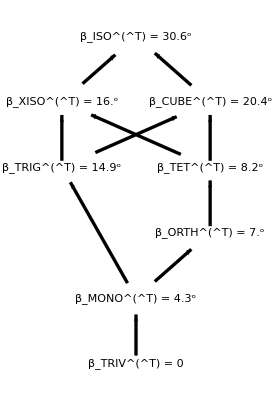

[T] = 1(10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0. | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

#### Map used in SSA2023 by Aakash Gupta, generated from ES_FarFromMono.nb This map is far from MONO, and its Poisson parameter for its closest ISO is near 0.25.

```mathematica
TmatSSA2023=({{0.317082, -0.00658517, 0.227862, 0.219176, 0.114762, -0.244823}, {-0.00658517, 0.07346, -0.114858, -0.0207015, 0.0275774, -0.142342}, {0.227862, -0.114858, 0.420424, 0.212793, 0.0528639, 0.120438}, {0.219176, -0.0207015, 0.212793, 0.241031, 0.102265, -0.162818}, {0.114762, 0.0275774, 0.0528639, 0.102265, 0.0962717, -0.147361}, {-0.244823, -0.142342, 0.120438, -0.162818, -0.147361, 0.64901}});
```

```mathematica
MatrixNote[TmatSSA2023]="T is SSA2023"
MatrixShortNote[TmatSSA2023]="SSA"
PrintVoigt[TmatSSA2023]
```

T is SSA2023

SSA

The [T]_𝔹𝔹 matrix is (0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

The eigenvalues are: {0.965054,0.701544,0.060227,0.0422136,0.0158499,0.0123903}

The Voigt matrix is (0.357328 | 0.0423998 | 0.344492 | -0.176408 | -0.0397992 | -0.0419674
0.0423998 | 0.209533 | 0.0934665 | 0.0427684 | -0.0605007 | 0.170826
0.344492 | 0.0934665 | 0.419451 | -0.166206 | -0.0740327 | 0.0186476
-0.176408 | 0.0427684 | -0.166206 | 0.158541 | -0.00329258 | 0.113931
-0.0397992 | -0.0605007 | -0.0740327 | -0.00329258 | 0.03673 | -0.057429
-0.0419674 | 0.170826 | 0.0186476 | 0.113931 | -0.057429 | 0.210212)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.806 = 46.19^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, bulk modulus κ = 0.216337, Poisson ratio = 0.274506

```mathematica
(*cmin=0;cmax=40; dc=4;
contoursMONO[TmatSSA2023]=Range[cmin,cmax,dc];
MaxForScaling[TmatSSA2023]=cmax-dc;*)
```

#### lattice for TmatSSA2023:

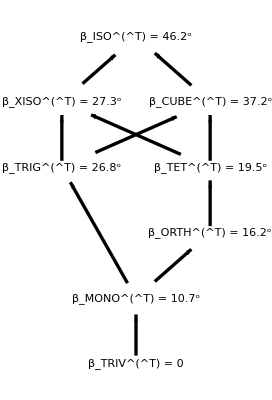

[T] = 1(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

#### Rob Arts 1993 thesis, p. 243 Mensch and Rasolofosaon (1997 GJI), Appendix B Dry Vosges sandstone (Eq B4) [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatArtsVosges=({{10.3, 0.9, 1.3, 1.4, 1.1, 0.8}, {0.9, 10.6, 2.1, 0.2, -0.2, -0.6}, {1.3, 2.1, 14.1, 0, -0.5, -1.0}, {1.4, 0.2, 0, 5.1, 0, 0.2}, {1.1, -0.2, -0.5, 0, 6.0, 0}, {0.8, -0.6, -1.0, 0.2, 0, 4.9}});
TmatArtsVosges = TmatOfCmat[CmatArtsVosges];
MatrixNote[TmatArtsVosges]="T is A-Vosges-sandstone"
MatrixShortNote[TmatArtsVosges]="AVos"
PrintVoigt[TmatArtsVosges]
density[TmatArtsVosges]=2080;
```

T is A-Vosges-sandstone

AVos

The [T]_𝔹𝔹 matrix is (10.2 | 0 | 0.4 | -1.2 | 0.92376 | 1.30639
0 | 12. | 0 | -1.3 | 1.09697 | 0.326599
0.4 | 0 | 9.8 | -1.4 | 1.27017 | -0.653197
-1.2 | -1.3 | -1.4 | 9.55 | -0.375278 | 0.449073
0.92376 | 1.09697 | 1.27017 | -0.375278 | 10.9167 | -2.09775
1.30639 | 0.326599 | -0.653197 | 0.449073 | -2.09775 | 14.5333)

The eigenvalues are: {15.902,13.5505,11.3843,9.73458,9.12961,7.29896}

The Voigt matrix is (10.3 | 0.9 | 1.3 | 1.4 | 1.1 | 0.8
0.9 | 10.6 | 2.1 | 0.2 | -0.2 | -0.6
1.3 | 2.1 | 14.1 | 0 | -0.5 | -1.
1.4 | 0.2 | 0 | 5.1 | 0 | 0.2
1.1 | -0.2 | -0.5 | 0 | 6. | 0
0.8 | -0.6 | -1. | 0.2 | 0 | 4.9)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 5.97595   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.213 = 12.22^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (10.4933 | 0. | 0. | 0. | 0. | 0.
0. | 10.4933 | 0. | 0. | 0. | 0.
0. | 0. | 10.4933 | 0. | 0. | 0.
0. | 0. | 0. | 10.4933 | 0. | 0.
0. | 0. | 0. | 0. | 10.4933 | 0.
0. | 0. | 0. | 0. | 0. | 14.5333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.34667 and μ = 5.24667, bulk modulus κ = 4.84444, Poisson ratio = 0.102123

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatArtsVosges]=Range[cmin,cmax,dc];
MaxForScaling[TmatArtsVosges]=cmax-dc;*)
```

#### Vestrum et al. (1996), Table 2; also used in Dellinger (2005), Appendix A [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatVestrum=({{16.85, 7.88, 6.81, 0.07, -0.18, 0.12}, {7.88, 16.03, 6.51, 0.00, -0.26, -0.08}, {6.81, 6.51, 11.14, 0.00, -0.05, -0.04}, {0.07, 0.00, 0.00, 3.03, 0.01, 0.04}, {-0.18, -0.26, -0.05, 0.01, 3.40, -0.01}, {0.12, -0.08, -0.04, 0.04, -0.01, 3.89}});
TmatVestrum = TmatOfCmat[CmatVestrum];
MatrixNote[TmatVestrum]="T is Vestrum"
MatrixShortNote[TmatVestrum]="Vest"
PrintVoigt[TmatVestrum]
density[TmatVestrum]=1300;  (* representative of "phenolic resin"; not listed in publication *)
```

T is Vestrum

Vest

The [T]_𝔹𝔹 matrix is (6.06 | 0.02 | 0.08 | -0.07 | 0.0404145 | 0.0571548
0.02 | 6.8 | -0.02 | -0.08 | -0.196299 | -0.400083
0.08 | -0.02 | 7.78 | -0.2 | 0.069282 | 0
-0.07 | -0.08 | -0.2 | 8.56 | -0.0635085 | -0.457238
0.0404145 | -0.196299 | 0.069282 | -0.0635085 | 6.65333 | 3.07356
0.0571548 | -0.400083 | 0 | -0.457238 | 3.07356 | 28.8067)

The eigenvalues are: {29.2436,8.60517,7.73878,6.81924,6.20594,6.04729}

The Voigt matrix is (16.85 | 7.88 | 6.81 | 0.07 | -0.18 | 0.12
7.88 | 16.03 | 6.51 | 0 | -0.26 | -0.08
6.81 | 6.51 | 11.14 | 0 | -0.05 | -0.04
0.07 | 0 | 0 | 3.03 | 0.01 | 0.04
-0.18 | -0.26 | -0.05 | 0.01 | 3.4 | -0.01
0.12 | -0.08 | -0.04 | 0.04 | -0.01 | 3.89)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 4.87785   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.147 = 8.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (7.17067 | 0. | 0. | 0. | 0. | 0.
0. | 7.17067 | 0. | 0. | 0. | 0.
0. | 0. | 7.17067 | 0. | 0. | 0.
0. | 0. | 0. | 7.17067 | 0. | 0.
0. | 0. | 0. | 0. | 7.17067 | 0.
0. | 0. | 0. | 0. | 0. | 28.8067)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 7.212 and μ = 3.58533, bulk modulus κ = 9.60222, Poisson ratio = 0.333971

```mathematica
(*cmin=0;cmax=8; dc=0.5;
contoursMONO[TmatVestrum]=Range[cmin,cmax,dc];
MaxForScaling[TmatVestrum]=cmax-dc;*)
```

#### Russell, Gaherty, et al. (2019 JGR), Table 1 [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatRussell=({{271.6149, 101.6837, 101.2700, 0, 0, −0.1902}, {101.6837, 233.9946, 99.9429, 0, 0, 0.3918}, {101.2700, 99.9429, 239.5542, 0, 0, 0.0071}, {0, 0, 0, 66.1769, 0.0452, 0}, {0, 0, 0, 0.0452, 74.6177, 0}, {−0.1902, 0.3918, 0.0071, 0, 0, 71.9655}});
TmatRussell = TmatOfCmat[CmatRussell];
MatrixNote[TmatRussell]="T is Russell"
MatrixShortNote[TmatRussell]="Russ"
PrintVoigt[TmatRussell]
```

T is Russell

Russ

The [T]_𝔹𝔹 matrix is (132.354 | 0.0904 | 0 | 0 | 0 | 0
0.0904 | 149.235 | 0 | 0 | 0 | 0
0 | 0 | 143.931 | 0.582 | 0.108195 | 0.170403
0 | 0 | 0.582 | 151.121 | -10.0938 | -15.9002
0 | 0 | 0.108195 | -10.0938 | 143.724 | 6.75419
0 | 0 | 0.170403 | -15.9002 | 6.75419 | 450.319)

The eigenvalues are: {451.334,157.213,149.236,143.943,136.605,132.353}

The Voigt matrix is (271.615 | 101.684 | 101.27 | 0 | 0 | -0.1902
101.684 | 233.995 | 99.9429 | 0 | 0 | 0.3918
101.27 | 99.9429 | 239.554 | 0 | 0 | 0.0071
0 | 0 | 0 | 66.1769 | 0.0452 | 0
0 | 0 | 0 | 0.0452 | 74.6177 | 0
-0.1902 | 0.3918 | 0.0071 | 0 | 0 | 71.9655)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 31.8626   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.057 = 3.29^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (144.073 | 0. | 0. | 0. | 0. | 0.
0. | 144.073 | 0. | 0. | 0. | 0.
0. | 0. | 144.073 | 0. | 0. | 0.
0. | 0. | 0. | 144.073 | 0. | 0.
0. | 0. | 0. | 0. | 144.073 | 0.
0. | 0. | 0. | 0. | 0. | 450.319)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 102.082 and μ = 72.0365, bulk modulus κ = 150.106, Poisson ratio = 0.293139

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatRussell]=Range[cmin,cmax,dc];
MaxForScaling[TmatRussell]=cmax-dc;*)
```

#### lattice for TmatRussell:

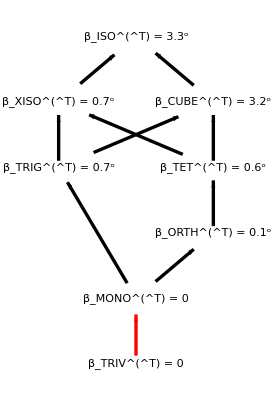

[T] = 1(132.354 | 0.0904 | 0. | 0. | 0. | 0.
0.0904 | 149.235 | 0. | 0. | 0. | 0.
0. | 0. | 143.931 | 0.582 | 0.108195 | 0.170403
0. | 0. | 0.582 | 151.121 | -10.0938 | -15.9002
0. | 0. | 0.108195 | -10.0938 | 143.724 | 6.75419
0. | 0. | 0.170403 | -15.9002 | 6.75419 | 450.319)

#### Francois, Geymonat, Berthaud (1998), Table 3 superalloy monocrystal (NOT oak) And also Norris (2006), Eq. 74 [who note a typo in the original for the C53 entry [the corrected entry was confirmed by C. Tape e-communication with Francois in July 2024] [units of GPa = 10^9 Pa = 10^9 N/m2] see Check_Tmat_FrancoisNorris.nb

```mathematica
CmatFrancois=1.({{243, 136, 135, 22, 52, -17}, {136, 239, 137, -28, 11, 16}, {135, 137, 233, 29, -49, 3}, {22, -28, 29, 133, -10, -4}, {52, 11, -49, -10, 119, -2}, {-17, 16, 3, -4, -2, 130}});
TmatFrancois = TmatOfCmat[CmatFrancois];
MatrixNote[TmatFrancois]="T is Francois"
MatrixShortNote[TmatFrancois]="Fra"
PrintVoigt[TmatFrancois]
(* density obtained via e-communication from M. Francois on 2023-07-03; it not listed in the 1998 publication or the 1995 thesis *)
density[TmatFrancois]=8600;
```

T is Francois

Fra

The [T]_𝔹𝔹 matrix is (266. | -20. | -8. | -50. | -36.9504 | 18.7794
-20. | 238. | -4. | -41. | 92.9534 | 11.431
-8. | -4. | 260. | 33. | -4.04145 | 1.63299
-50. | -41. | 33. | 105. | -2.3094 | -0.816497
-36.9504 | 92.9534 | -4.04145 | -2.3094 | 99.6667 | 3.77124
18.7794 | 11.431 | 1.63299 | -0.816497 | 3.77124 | 510.333)

The eigenvalues are: {512.272,311.93,285.277,243.802,78.7826,46.9368}

The Voigt matrix is (243. | 136. | 135. | 22. | 52. | -17.
136. | 239. | 137. | -28. | 11. | 16.
135. | 137. | 233. | 29. | -49. | 3.
22. | -28. | 29. | 133. | -10. | -4.
52. | 11. | -49. | -10. | 119. | -2.
-17. | 16. | 3. | -4. | -2. | 130.)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 246.682   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.353 = 20.23^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (193.733 | 0. | 0. | 0. | 0. | 0.
0. | 193.733 | 0. | 0. | 0. | 0.
0. | 0. | 193.733 | 0. | 0. | 0.
0. | 0. | 0. | 193.733 | 0. | 0.
0. | 0. | 0. | 0. | 193.733 | 0.
0. | 0. | 0. | 0. | 0. | 510.333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 105.533 and μ = 96.8667, bulk modulus κ = 170.111, Poisson ratio = 0.260705

```mathematica
(*cmin=0;cmax=20; dc=2;
contoursMONO[TmatFrancois]=Range[cmin,cmax,dc];
MaxForScaling[TmatFrancois]=cmax-dc;*)
```

#### Francois (1995) thesis, p. 53: oak wood [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatFrancoisOak=({{3.51, 0.47, 1.27, -0.56, -0.67, -0.02}, {0.47, 13.20, 1.03, 0.24, -0.04, -0.07}, {1.27, 1.03, 2.97, 0.14, -0.23, -0.59}, {-0.56, 0.24, 0.14, 0.37, 0.17, 0.06}, {-0.67, -0.04, -0.23, 0.17, 1.09, -0.07}, {-0.02, -0.07, -0.59, 0.06, -0.07, 0.81}});
TmatFrancoisOak = TmatOfCmat[CmatFrancoisOak];
MatrixNote[TmatFrancoisOak]="T is FrancoisOak"
MatrixShortNote[TmatFrancoisOak]="Foak"
PrintVoigt[TmatFrancoisOak]
density[TmatFrancoisOak]=953;
```

T is FrancoisOak

Foak

The [T]_𝔹𝔹 matrix is (0.74 | 0.34 | 0.12 | 0.8 | -0.34641 | -0.146969
0.34 | 2.18 | -0.14 | 0.63 | -0.144338 | -0.767507
0.12 | -0.14 | 1.62 | -0.05 | 0.629312 | -0.555218
0.8 | 0.63 | -0.05 | 7.885 | 2.93583 | 3.85795
-0.34641 | -0.144338 | 0.629312 | 2.93583 | 3.38833 | 2.21796
-0.146969 | -0.767507 | -0.555218 | 3.85795 | 2.21796 | 8.40667)

The eigenvalues are: {13.3513,4.92377,2.74917,1.6284,1.2553,0.31202}

The Voigt matrix is (3.51 | 0.47 | 1.27 | -0.56 | -0.67 | -0.02
0.47 | 13.2 | 1.03 | 0.24 | -0.04 | -0.07
1.27 | 1.03 | 2.97 | 0.14 | -0.23 | -0.59
-0.56 | 0.24 | 0.14 | 0.37 | 0.17 | 0.06
-0.67 | -0.04 | -0.23 | 0.17 | 1.09 | -0.07
-0.02 | -0.07 | -0.59 | 0.06 | -0.07 | 0.81)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 9.67988   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.722 = 41.38^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3.16267 | 0. | 0. | 0. | 0. | 0.
0. | 3.16267 | 0. | 0. | 0. | 0.
0. | 0. | 3.16267 | 0. | 0. | 0.
0. | 0. | 0. | 3.16267 | 0. | 0.
0. | 0. | 0. | 0. | 3.16267 | 0.
0. | 0. | 0. | 0. | 0. | 8.40667)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.748 and μ = 1.58133, bulk modulus κ = 2.80222, Poisson ratio = 0.262515

#### Francois (1995) thesis, p. 53: beech wood THIS ELASTIC MAP HAS A NEGATIVE EIGENVALUE. [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatFrancoisBeech=({{2.45, 4.58, 0.91, -0.59, 0.27, 0.13}, {4.58, 19.47, 0.80, 1.64, -1.02, -0.77}, {0.91, 0.80, 4.70, 0.70, 0.25, -0.88}, {-0.59, 1.64, 0.70, 3.15, 0.32, -0.17}, {0.27, -1.02, 0.25, 0.32, 1.08, -0.86}, {0.13, -0.77, -0.88, -0.17, -0.86, 2.54}});
TmatFrancoisBeech = TmatOfCmat[CmatFrancoisBeech];
MatrixNote[TmatFrancoisBeech]="T is FrancoisBeech"
MatrixShortNote[TmatFrancoisBeech]="Fbch"
PrintVoigt[TmatFrancoisBeech]
density[TmatFrancoisBeech]=897.6;
```

T is FrancoisBeech

Fbch

The [T]_𝔹𝔹 matrix is (6.3 | 0.64 | -0.34 | 2.23 | -0.202073 | 1.42887
0.64 | 2.16 | -1.72 | -1.29 | -0.721688 | -0.408248
-0.34 | -1.72 | 5.08 | -0.9 | 0.646632 | -1.24107
2.23 | -1.29 | -0.9 | 6.38 | 4.97676 | 6.90348
-0.202073 | -0.721688 | 0.646632 | 4.97676 | 7.17333 | 4.70697
1.42887 | -0.408248 | -1.24107 | 6.90348 | 4.70697 | 13.0667)

The eigenvalues are: {21.1299,7.34656,5.76496,4.00141,1.9624,-0.0451972}

The Voigt matrix is (2.45 | 4.58 | 0.91 | -0.59 | 0.27 | 0.13
4.58 | 19.47 | 0.8 | 1.64 | -1.02 | -0.77
0.91 | 0.8 | 4.7 | 0.7 | 0.25 | -0.88
-0.59 | 1.64 | 0.7 | 3.15 | 0.32 | -0.17
0.27 | -1.02 | 0.25 | 0.32 | 1.08 | -0.86
0.13 | -0.77 | -0.88 | -0.17 | -0.86 | 2.54)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 15.3621   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.711 = 40.76^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (5.41867 | 0. | 0. | 0. | 0. | 0.
0. | 5.41867 | 0. | 0. | 0. | 0.
0. | 0. | 5.41867 | 0. | 0. | 0.
0. | 0. | 0. | 5.41867 | 0. | 0.
0. | 0. | 0. | 0. | 5.41867 | 0.
0. | 0. | 0. | 0. | 0. | 13.0667)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2.54933 and μ = 2.70933, bulk modulus κ = 4.35556, Poisson ratio = 0.242394

#### Francois (1995) thesis, p. 53: beech wood PERTURBED SUCH THAT IT HAS POSITIVE EIGENVALUES [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
tpert=tpertTmat[TmatFrancoisBeech,0.01,0.1,-2]+0.01
TmatFrancoisBeechPert = Tpert[TmatFrancoisBeech,tpert];
MatrixNote[TmatFrancoisBeechPert]="T is FrancoisBeechPert"
MatrixShortNote[TmatFrancoisBeechPert]="Fbchp"
PrintVoigt[TmatFrancoisBeechPert]
density[TmatFrancoisBeechPert]=density[TmatFrancoisBeech];
```

0.02

T is FrancoisBeechPert

Fbchp

The [T]_𝔹𝔹 matrix is (6.28237 | 0.6272 | -0.3332 | 2.1854 | -0.198031 | 1.40029
0.6272 | 2.22517 | -1.6856 | -1.2642 | -0.707254 | -0.400083
-0.3332 | -1.6856 | 5.08677 | -0.882 | 0.6337 | -1.21625
2.1854 | -1.2642 | -0.882 | 6.36077 | 4.87722 | 6.76541
-0.198031 | -0.707254 | 0.6337 | 4.87722 | 7.13824 | 4.61283
1.40029 | -0.400083 | -1.21625 | 6.76541 | 4.61283 | 13.0667)

The eigenvalues are: {20.8967,7.31024,5.77184,4.07666,2.03677,0.0678148}

The Voigt matrix is (2.56036 | 4.53939 | 0.942787 | -0.5782 | 0.2646 | 0.1274
4.53939 | 19.24 | 0.834987 | 1.6072 | -0.9996 | -0.7546
0.942787 | 0.834987 | 4.76536 | 0.686 | 0.245 | -0.8624
-0.5782 | 1.6072 | 0.686 | 3.14119 | 0.3136 | -0.1666
0.2646 | -0.9996 | 0.245 | 0.3136 | 1.11259 | -0.8428
0.1274 | -0.7546 | -0.8624 | -0.1666 | -0.8428 | 2.54339)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 15.0549   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.701 = 40.19^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (5.41867 | 0. | 0. | 0. | 0. | 0.
0. | 5.41867 | 0. | 0. | 0. | 0.
0. | 0. | 5.41867 | 0. | 0. | 0.
0. | 0. | 0. | 5.41867 | 0. | 0.
0. | 0. | 0. | 0. | 5.41867 | 0.
0. | 0. | 0. | 0. | 0. | 13.0667)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2.54933 and μ = 2.70933, bulk modulus κ = 4.35556, Poisson ratio = 0.242394

#### Francois (1995) thesis, p. 53: sipo mahogany wood THIS ELASTIC MAP HAS A NEGATIVE EIGENVALUE. [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatFrancoisSipo=({{2.31, 0.26, 0.18, 0.28, 0.09, -0.25}, {0.26, 1.54, 1.23, 0.19, 1.02, 0.05}, {0.18, 1.23, 12.32, 1.63, 0.15, 0.01}, {0.28, 0.19, 1.63, 0.53, 0.51, -0.02}, {0.09, 1.02, 0.15, 0.51, 0.38, -0.11}, {-0.25, 0.05, 0.01, -0.02, -0.11, 0.61}});
TmatFrancoisSipo = TmatOfCmat[CmatFrancoisSipo];
MatrixNote[TmatFrancoisSipo]="T is FrancoisSipo"
MatrixShortNote[TmatFrancoisSipo]="Fspo"
PrintVoigt[TmatFrancoisSipo]
density[TmatFrancoisSipo]=585;
```

T is FrancoisSipo

Fspo

The [T]_𝔹𝔹 matrix is (1.06 | 1.02 | -0.04 | -0.09 | -1.61081 | 1.71464
1.02 | 0.76 | -0.22 | 0.93 | 0.467654 | 1.02879
-0.04 | -0.22 | 1.22 | 0.3 | -0.127017 | -0.155134
-0.09 | 0.93 | 0.3 | 1.665 | -0.828498 | 0.11431
-1.61081 | 0.467654 | -0.127017 | -0.828498 | 8.00167 | -5.11003
1.71464 | 1.02879 | -0.155134 | 0.11431 | -5.11003 | 6.50333)

The eigenvalues are: {12.9472,2.9429,2.19126,1.15125,-0.816936,0.794313}

The Voigt matrix is (2.31 | 0.26 | 0.18 | 0.28 | 0.09 | -0.25
0.26 | 1.54 | 1.23 | 0.19 | 1.02 | 0.05
0.18 | 1.23 | 12.32 | 1.63 | 0.15 | 0.01
0.28 | 0.19 | 1.63 | 0.53 | 0.51 | -0.02
0.09 | 1.02 | 0.15 | 0.51 | 0.38 | -0.11
-0.25 | 0.05 | 0.01 | -0.02 | -0.11 | 0.61)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 10.4466   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.88 = 50.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.54133 | 0. | 0. | 0. | 0. | 0.
0. | 2.54133 | 0. | 0. | 0. | 0.
0. | 0. | 2.54133 | 0. | 0. | 0.
0. | 0. | 0. | 2.54133 | 0. | 0.
0. | 0. | 0. | 0. | 2.54133 | 0.
0. | 0. | 0. | 0. | 0. | 6.50333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.32067 and μ = 1.27067, bulk modulus κ = 2.16778, Poisson ratio = 0.254824

#### Francois (1995) thesis, p. 53: sipo mahogany wood PERTURBED SUCH THAT IT HAS POSITIVE EIGENVALUES [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
tpert=tpertTmat[TmatFrancoisSipo,0.01,0.3,-2]+0.01
TmatFrancoisSipoPert = Tpert[TmatFrancoisSipo,tpert];
MatrixNote[TmatFrancoisSipoPert]="T is FrancoisSipoPert"
MatrixShortNote[TmatFrancoisSipoPert]="Fspop"
PrintVoigt[TmatFrancoisSipoPert]
density[TmatFrancoisSipoPert]=density[TmatFrancoisSipo];
```

0.25

T is FrancoisSipoPert

Fspop

The [T]_𝔹𝔹 matrix is (1.43033 | 0.765 | -0.03 | -0.0675 | -1.20811 | 1.28598
0.765 | 1.20533 | -0.165 | 0.6975 | 0.35074 | 0.771589
-0.03 | -0.165 | 1.55033 | 0.225 | -0.0952628 | -0.116351
-0.0675 | 0.6975 | 0.225 | 1.88408 | -0.621373 | 0.0857321
-1.20811 | 0.35074 | -0.0952628 | -0.621373 | 6.63658 | -3.83252
1.28598 | 0.771589 | -0.116351 | 0.0857321 | -3.83252 | 6.50333)

The eigenvalues are: {10.7861,3.16798,2.31429,1.57288,1.32805,0.0406971}

The Voigt matrix is (2.698 | 0.525167 | 0.465167 | 0.21 | 0.0675 | -0.1875
0.525167 | 2.1205 | 1.25267 | 0.1425 | 0.765 | 0.0375
0.465167 | 1.25267 | 10.2055 | 1.2225 | 0.1125 | 0.0075
0.21 | 0.1425 | 1.2225 | 0.715167 | 0.3825 | -0.015
0.0675 | 0.765 | 0.1125 | 0.3825 | 0.602667 | -0.0825
-0.1875 | 0.0375 | 0.0075 | -0.015 | -0.0825 | 0.775167)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 7.83494   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.737 = 42.21^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.54133 | 0. | 0. | 0. | 0. | 0.
0. | 2.54133 | 0. | 0. | 0. | 0.
0. | 0. | 2.54133 | 0. | 0. | 0.
0. | 0. | 0. | 2.54133 | 0. | 0.
0. | 0. | 0. | 0. | 2.54133 | 0.
0. | 0. | 0. | 0. | 0. | 6.50333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.32067 and μ = 1.27067, bulk modulus κ = 2.16778, Poisson ratio = 0.254824

#### Francois (1995) thesis, p. 54: dry Vosges sandstone [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatFrancoisVosges=({{12.2, -2.2, 1.9, 0.9, 0.8, -0.5}, {-2.2, 13.0, 2.9, 0.2, -0.3, 0.4}, {1.9, 2.9, 13.9, 0.0, -0.0, 0.1}, {0.9, 0.2, 0.0, 4.0, 1.2, 0.0}, {0.8, -0.3, -0.0, 1.2, 5.4, 0.0}, {-0.5, 0.4, 0.1, 0.0, 0.0, 5.4}});
TmatFrancoisVosges = TmatOfCmat[CmatFrancoisVosges];
MatrixNote[TmatFrancoisVosges]="T is F-Vosges-sandstone"
MatrixShortNote[TmatFrancoisVosges]="FVos"
PrintVoigt[TmatFrancoisVosges]
density[TmatFrancoisVosges]=density[TmatArtsVosges];
```

T is F-Vosges-sandstone

FVos

The [T]_𝔹𝔹 matrix is (8. | 2.4 | 0 | -0.7 | 0.635085 | 0.898146
2.4 | 10.8 | 0 | -1.1 | 0.288675 | 0.408248
0 | 0 | 10.8 | 0.9 | -0.173205 | 0
-0.7 | -1.1 | 0.9 | 14.8 | -0.34641 | 0.734847
0.635085 | 0.288675 | -0.173205 | -0.34641 | 9.53333 | -2.78129
0.898146 | 0.408248 | 0 | 0.734847 | -2.78129 | 14.7667)

The eigenvalues are: {16.4453,15.1848,11.7572,10.5771,8.33445,6.40119}

The Voigt matrix is (12.2 | -2.2 | 1.9 | 0.9 | 0.8 | -0.5
-2.2 | 13. | 2.9 | 0.2 | -0.3 | 0.4
1.9 | 2.9 | 13.9 | 0 | 0 | 0.1
0.9 | 0.2 | 0 | 4. | 1.2 | 0
0.8 | -0.3 | 0 | 1.2 | 5.4 | 0
-0.5 | 0.4 | 0.1 | 0 | 0 | 5.4)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 7.85841   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.271 = 15.53^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (10.7867 | 0. | 0. | 0. | 0. | 0.
0. | 10.7867 | 0. | 0. | 0. | 0.
0. | 0. | 10.7867 | 0. | 0. | 0.
0. | 0. | 0. | 10.7867 | 0. | 0.
0. | 0. | 0. | 0. | 10.7867 | 0.
0. | 0. | 0. | 0. | 0. | 14.7667)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.32667 and μ = 5.39333, bulk modulus κ = 4.92222, Poisson ratio = 0.0987103

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatArtsVosges]=Range[cmin,cmax,dc];
MaxForScaling[TmatArtsVosges]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG100, 0.1 MPa

```mathematica
CmatLokajicekWG100lp=({{47.6, 16.7, 16.3, 0.1, -1.1, -2}, {16.7, 51.1, 16.8, 0, -0.6, -2.1}, {16.3, 16.8, 51.7, 0.2, -1.8, -1.2}, {0.1, 0, 0.2, 16.8, -0.2, -0.2}, {-1.1, -0.6, -1.8, -0.2, 16.8, 0.1}, {-2, -2.1, -1.2, -0.2, 0.1, 16.8}});
```

```mathematica
TmatLokajicekWG100lp = TmatOfCmat[CmatLokajicekWG100lp];
MatrixNote[TmatLokajicekWG100lp]="T is Lokajicek-WG100-lp"
MatrixShortNote[TmatLokajicekWG100lp]="Lok1"
PrintVoigt[TmatLokajicekWG100lp]
density[TmatLokajicekWG100lp]=2635;
```

T is Lokajicek-WG100-lp

Lok1

The [T]_𝔹𝔹 matrix is (33.6 | -0.4 | -0.4 | -0.1 | -0.173205 | 0.244949
-0.4 | 33.6 | 0.2 | 0.5 | 1.09697 | -2.85774
-0.4 | 0.2 | 33.6 | -0.1 | -0.981495 | -4.32743
-0.1 | 0.5 | -0.1 | 32.65 | 0.721688 | 1.63299
-0.173205 | 1.09697 | -0.981495 | 0.721688 | 34.4167 | -1.03709
0.244949 | -2.85774 | -4.32743 | 1.63299 | -1.03709 | 83.3333)

The eigenvalues are: {83.942,35.7219,34.0307,33.0105,32.4111,32.0838}

The Voigt matrix is (47.6 | 16.7 | 16.3 | 0.1 | -1.1 | -2.
16.7 | 51.1 | 16.8 | 0 | -0.6 | -2.1
16.3 | 16.8 | 51.7 | 0.2 | -1.8 | -1.2
0.1 | 0 | 0.2 | 16.8 | -0.2 | -0.2
-1.1 | -0.6 | -1.8 | -0.2 | 16.8 | 0.1
-2. | -2.1 | -1.2 | -0.2 | 0.1 | 16.8)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 8.34578   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.074 = 4.26^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (33.5733 | 0. | 0. | 0. | 0. | 0.
0. | 33.5733 | 0. | 0. | 0. | 0.
0. | 0. | 33.5733 | 0. | 0. | 0.
0. | 0. | 0. | 33.5733 | 0. | 0.
0. | 0. | 0. | 0. | 33.5733 | 0.
0. | 0. | 0. | 0. | 0. | 83.3333)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 16.5867 and μ = 16.7867, bulk modulus κ = 27.7778, Poisson ratio = 0.248502

```mathematica
(*cmin=0;cmax=4.5; dc=0.5;
contoursMONO[TmatLokajicekWG100lp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG100lp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG100, 400 MPa

```mathematica
CmatLokajicekWG100hp=({{101.4, 34.8, 34.4, 0.2, 0.6, 0.7}, {34.8, 100.8, 33.4, 0.9, 0.9, 1}, {34.4, 33.4, 104.4, 0.9, 0.4, 0.4}, {0.2, 0.9, 0.9, 34.1, 0.1, 0.2}, {0.6, 0.9, 0.4, 0.1, 34.3, 0}, {0.7, 1, 0.4, 0.2, 0, 34.4}});
```

```mathematica
TmatLokajicekWG100hp = TmatOfCmat[CmatLokajicekWG100hp];
MatrixNote[TmatLokajicekWG100hp]="T is Lokajicek-WG100-hp"
MatrixShortNote[TmatLokajicekWG100hp]="Lok2"
PrintVoigt[TmatLokajicekWG100hp]
density[TmatLokajicekWG100hp]=density[TmatLokajicekWG100lp];
```

T is Lokajicek-WG100-hp

Lok2

The [T]_𝔹𝔹 matrix is (68.2 | 0.2 | 0.4 | 0.7 | -0.404145 | 1.63299
0.2 | 68.6 | 0 | 0.3 | 0.404145 | 1.55134
0.4 | 0 | 68.8 | 0.3 | 0.519615 | 1.71464
0.7 | 0.3 | 0.3 | 66.3 | 0.404145 | -0.653197
-0.404145 | 0.404145 | 0.519615 | 0.404145 | 69.7 | -1.13137
1.63299 | 1.55134 | 1.71464 | -0.653197 | -1.13137 | 170.6)

The eigenvalues are: {170.695,70.1139,68.9835,68.6372,67.7971,65.9732}

The Voigt matrix is (101.4 | 34.8 | 34.4 | 0.2 | 0.6 | 0.7
34.8 | 100.8 | 33.4 | 0.9 | 0.9 | 1.
34.4 | 33.4 | 104.4 | 0.9 | 0.4 | 0.4
0.2 | 0.9 | 0.9 | 34.1 | 0.1 | 0.2
0.6 | 0.9 | 0.4 | 0.1 | 34.3 | 0
0.7 | 1. | 0.4 | 0.2 | 0 | 34.4)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 5.38591   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.0235 = 1.35^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (68.32 | 0. | 0. | 0. | 0. | 0.
0. | 68.32 | 0. | 0. | 0. | 0.
0. | 0. | 68.32 | 0. | 0. | 0.
0. | 0. | 0. | 68.32 | 0. | 0.
0. | 0. | 0. | 0. | 68.32 | 0.
0. | 0. | 0. | 0. | 0. | 170.6)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 34.0933 and μ = 34.16, bulk modulus κ = 56.8667, Poisson ratio = 0.249756

```mathematica
(*cmin=0;cmax=1.3; dc=0.1;
contoursMONO[TmatLokajicekWG100hp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG100hp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG600, 0.1 MPa

```mathematica
CmatLokajicekWG600lp=({{3.5, 1.3, 1.3, 0, -0.2, -0.5}, {1.3, 3.4, 1.2, -0.1, -0.1, -0.4}, {1.3, 1.2, 3.4, -0.1, -0.2, -0.2}, {0, -0.1, -0.1, 1.2, 0, 0}, {-0.2, -0.1, -0.2, 0, 1.2, 0}, {-0.5, -0.4, -0.2, 0, 0, 1.3}});
```

```mathematica
TmatLokajicekWG600lp = TmatOfCmat[CmatLokajicekWG600lp];
MatrixNote[TmatLokajicekWG600lp]="T is Lokajicek-WG600-lp"
MatrixShortNote[TmatLokajicekWG600lp]="Lok3"
PrintVoigt[TmatLokajicekWG600lp]
density[TmatLokajicekWG600lp]=density[TmatLokajicekWG100lp];
```

T is Lokajicek-WG600-lp

Lok3

The [T]_𝔹𝔹 matrix is (2.4 | 0 | 0 | -0.1 | 0.057735 | -0.163299
0 | 2.4 | 0 | 0.1 | 0.057735 | -0.408248
0 | 0 | 2.6 | 0.1 | -0.288675 | -0.898146
-0.1 | 0.1 | 0.1 | 2.15 | 0.0288675 | -0.0816497
0.057735 | 0.057735 | -0.288675 | 0.0288675 | 2.18333 | 0.0471405
-0.163299 | -0.408248 | -0.898146 | -0.0816497 | 0.0471405 | 5.96667)

The eigenvalues are: {6.24436,2.63467,2.45739,2.29532,2.11735,1.95091}

The Voigt matrix is (3.5 | 1.3 | 1.3 | 0 | -0.2 | -0.5
1.3 | 3.4 | 1.2 | -0.1 | -0.1 | -0.4
1.3 | 1.2 | 3.4 | -0.1 | -0.2 | -0.2
0 | -0.1 | -0.1 | 1.2 | 0 | 0
-0.2 | -0.1 | -0.2 | 0 | 1.2 | 0
-0.5 | -0.4 | -0.2 | 0 | 0 | 1.3)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 1.54747   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.192 = 11.021^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.34667 | 0. | 0. | 0. | 0. | 0.
0. | 2.34667 | 0. | 0. | 0. | 0.
0. | 0. | 2.34667 | 0. | 0. | 0.
0. | 0. | 0. | 2.34667 | 0. | 0.
0. | 0. | 0. | 0. | 2.34667 | 0.
0. | 0. | 0. | 0. | 0. | 5.96667)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1.20667 and μ = 1.17333, bulk modulus κ = 1.98889, Poisson ratio = 0.253501

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatLokajicekWG600lp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG600lp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG600, 400 MPa

```mathematica
CmatLokajicekWG600hp=({{99.5, 32.8, 33.0, 0.7, -0.2, 0.8}, {32.8, 99.3, 33.2, 1.0, 0.5, 1.0}, {33.0, 33.2, 102.3, 0.6, 0, 0.7}, {0.7, 1.0, 0.6, 33.5, 0.1, 0.1}, {-0.2, 0.5, 0, 0.1, 33.5, 0.1}, {0.8, 1.0, 0.7, 0.1, 0.1, 33.4}});
```

```mathematica
TmatLokajicekWG600hp = TmatOfCmat[CmatLokajicekWG600hp];
MatrixNote[TmatLokajicekWG600hp]="T is Lokajicek-WG600-hp"
MatrixShortNote[TmatLokajicekWG600hp]="Lok4"
PrintVoigt[TmatLokajicekWG600hp]
density[TmatLokajicekWG600hp]=density[TmatLokajicekWG100lp];
```

T is Lokajicek-WG600-hp

Lok4

The [T]_𝔹𝔹 matrix is (67. | 0.2 | 0.2 | 0.3 | 0.288675 | 1.87794
0.2 | 67. | 0.2 | 0.7 | 0.173205 | 0.244949
0.2 | 0.2 | 66.8 | 0.2 | 0.23094 | 2.04124
0.3 | 0.7 | 0.2 | 66.6 | -0.173205 | 0
0.288675 | 0.173205 | 0.23094 | -0.173205 | 68.1333 | -1.50849
1.87794 | 0.244949 | 2.04124 | 0 | -1.50849 | 166.367)

The eigenvalues are: {166.468,68.3107,67.6915,66.7852,66.637,66.0081}

The Voigt matrix is (99.5 | 32.8 | 33. | 0.7 | -0.2 | 0.8
32.8 | 99.3 | 33.2 | 1. | 0.5 | 1.
33. | 33.2 | 102.3 | 0.6 | 0 | 0.7
0.7 | 1. | 0.6 | 33.5 | 0.1 | 0.1
-0.2 | 0.5 | 0 | 0.1 | 33.5 | 0.1
0.8 | 1. | 0.7 | 0.1 | 0.1 | 33.4)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 4.83308   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.0216 = 1.24^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (67.1067 | 0. | 0. | 0. | 0. | 0.
0. | 67.1067 | 0. | 0. | 0. | 0.
0. | 0. | 67.1067 | 0. | 0. | 0.
0. | 0. | 0. | 67.1067 | 0. | 0.
0. | 0. | 0. | 0. | 67.1067 | 0.
0. | 0. | 0. | 0. | 0. | 166.367)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 33.0867 and μ = 33.5533, bulk modulus κ = 55.4556, Poisson ratio = 0.248249

```mathematica
(*cmin=0;cmax=1.3; dc=0.1;
contoursMONO[TmatLokajicekWG600hp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG600hp]=cmax-dc;*)
```

#### THIS IS A MAP FOR TESTING ONLY Becker et al. (2008, 2014) https://www-udc.ig.utexas.edu/external/becker/anisotropy_model.html Line 12794 of safs417nc3_er.s.0.75.WLD.200.savd.dat

```mathematica
CmatBecker=({{2.51779*^2, 9.32360*^1, 8.44840*^1, 7.62656*^-1, 1.08919, 1.28893*^1}, {9.32360*^1, 2.33514*^2, 8.64265*^1, 1.21066, 6.10859*^-1, 7.16282}, {8.44840*^1, 8.64265*^1, 2.14772*^2, 5.12094*^-1, 1.80794*^-1, -1.88478}, {7.62656*^-1, 1.21066, 5.12094*^-1, 6.82019*^1, 3.21513, 8.08571*^-1}, {1.08919, 6.10859*^-1, 1.80794*^-1, 3.21513, 7.07792*^1, 8.87808*^-1}, {1.28893*^1, 7.16282, -1.88478, 8.08571*^-1, 8.87808*^-1, 7.90952*^1}});
```

```mathematica
TmatBecker = TmatOfCmat[CmatBecker];
MatrixNote[TmatBecker]="T is Becker"
MatrixShortNote[TmatBecker]="Becker"
PrintVoigt[TmatBecker]
```

T is Becker

Becker

The [T]_𝔹𝔹 matrix is (136.404 | 6.43026 | 1.61714 | 0.448004 | 0.547979 | 2.02933
6.43026 | 141.558 | 1.77562 | -0.478331 | 0.772761 | 1.5357
1.61714 | 1.77562 | 158.19 | -5.72648 | 13.7535 | 14.8336
0.448004 | -0.478331 | -5.72648 | 149.41 | -6.39415 | -6.66363
0.547979 | 0.772761 | 13.7535 | -6.39415 | 141.202 | 16.808
2.02933 | 1.5357 | 14.8336 | -6.66363 | 16.808 | 409.453)

The eigenvalues are: {411.71,167.401,147.16,145.136,132.797,132.014}

The Voigt matrix is (251.779 | 93.236 | 84.484 | 0.762656 | 1.08919 | 12.8893
93.236 | 233.514 | 86.4265 | 1.21066 | 0.610859 | 7.16282
84.484 | 86.4265 | 214.772 | 0.512094 | 0.180794 | -1.88478
0.762656 | 1.21066 | 0.512094 | 68.2019 | 3.21513 | 0.808571
1.08919 | 0.610859 | 0.180794 | 3.21513 | 70.7792 | 0.887808
12.8893 | 7.16282 | -1.88478 | 0.808571 | 0.887808 | 79.0952)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 44.971   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.086 = 4.92^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (145.353 | 0. | 0. | 0. | 0. | 0.
0. | 145.353 | 0. | 0. | 0. | 0.
0. | 0. | 145.353 | 0. | 0. | 0.
0. | 0. | 0. | 145.353 | 0. | 0.
0. | 0. | 0. | 0. | 145.353 | 0.
0. | 0. | 0. | 0. | 0. | 409.453)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 88.0332 and μ = 72.6765, bulk modulus κ = 136.484, Poisson ratio = 0.273889

```mathematica
(*cmin=0;cmax=5; dc=0.5;
contoursMONO[TmatBecker]=Range[cmin,cmax,dc];
MaxForScaling[TmatBecker]=cmax-dc;*)
```

```mathematica
(* MinimizationFacts[TmatBecker,XISO]*)
```

## Ismail and Mainprice (1998) maps (Table 2)

#### Total database

```mathematica
CmatIsmailMainpriceTotal=({{195.45, 71.11, 72.08, -0.06, -0.09, -0.08}, {71.11, 236.91, 72.37, 0.17, -0.20, -0.11}, {72.08, 72.37, 205.92, 0.37, -0.21, -00.09}, {-0.06, 0.17, 0.37, 71.37, -0.18, -0.36}, {-0.09, -0.20, -0.21, -0.18, 62.99, 0.06}, {-0.08, -0.11, -0.09, -0.36, 0.06, 69.77}});
```

```mathematica
TmatIsmailMainpriceTotal = TmatOfCmat[CmatIsmailMainpriceTotal];
MatrixNote[TmatIsmailMainpriceTotal]="T is IM1998-total"
MatrixShortNote[TmatIsmailMainpriceTotal]="IMtot"
PrintVoigt[TmatIsmailMainpriceTotal]
```

T is IM1998-total

IMtot

The [T]_𝔹𝔹 matrix is (142.74 | -0.36 | -0.72 | 0.23 | -0.363731 | 0.391918
-0.36 | 125.98 | 0.12 | -0.11 | 0.0750555 | -0.408248
-0.72 | 0.12 | 139.54 | -0.03 | -0.0057735 | -0.228619
0.23 | -0.11 | -0.03 | 145.07 | 11.801 | 17.0444
-0.363731 | 0.0750555 | -0.0057735 | 11.801 | 136.743 | 4.31099
0.391918 | -0.408248 | -0.228619 | 17.0444 | 4.31099 | 356.467)

The eigenvalues are: {357.958,152.115,142.913,139.386,128.202,125.966}

The Voigt matrix is (195.45 | 71.11 | 72.08 | -0.06 | -0.09 | -0.08
71.11 | 236.91 | 72.37 | 0.17 | -0.2 | -0.11
72.08 | 72.37 | 205.92 | 0.37 | -0.21 | -0.09
-0.06 | 0.17 | 0.37 | 71.37 | -0.18 | -0.36
-0.09 | -0.2 | -0.21 | -0.18 | 62.99 | 0.06
-0.08 | -0.11 | -0.09 | -0.36 | 0.06 | 69.77)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 33.4676   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.071 = 4.06^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (138.015 | 0. | 0. | 0. | 0. | 0.
0. | 138.015 | 0. | 0. | 0. | 0.
0. | 0. | 138.015 | 0. | 0. | 0.
0. | 0. | 0. | 138.015 | 0. | 0.
0. | 0. | 0. | 0. | 138.015 | 0.
0. | 0. | 0. | 0. | 0. | 356.467)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 72.8173 and μ = 69.0073, bulk modulus κ = 118.822, Poisson ratio = 0.256716

```mathematica
(*cmin=0;cmax=4; dc=0.4;
contoursMONO[TmatIsmailMainpriceTotal]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceTotal]=cmax-dc;*)
```

#### Fast spreading ridge

```mathematica
CmatIsmailMainpriceRidge=({{195.91, 71.12, 72.21, -0.07, -0.24, -0.14}, {71.12, 239.36, 71.87, 0.03, -0.36, -0.16}, {72.21, 71.87, 203.72, 0.40, -0.39, 0.02}, {-0.07, 0.03, 0.40, 71.05, -0.15, -0.60}, {-0.24, -0.36, -0.39, -0.15, 62.49, 0.01}, {-0.14, -0.16, 0.02, -0.60, 0.01, 70.24}});
```

```mathematica
TmatIsmailMainpriceRidge = TmatOfCmat[CmatIsmailMainpriceRidge];
MatrixNote[TmatIsmailMainpriceRidge]="T is IM1998-spreading-ridge"
MatrixShortNote[TmatIsmailMainpriceRidge]="IMrdg"
PrintVoigt[TmatIsmailMainpriceRidge]
```

T is IM1998-spreading-ridge

IMrdg

The [T]_𝔹𝔹 matrix is (142.1 | -0.3 | -1.2 | 0.1 | -0.484974 | 0.293939
-0.3 | 124.98 | 0.02 | -0.12 | 0.103923 | -0.808332
-1.2 | 0.02 | 140.48 | -0.02 | -0.196299 | -0.228619
0.1 | -0.12 | -0.02 | 146.515 | 12.7392 | 17.5996
-0.484974 | 0.103923 | -0.196299 | 12.7392 | 136.012 | 6.1259
0.293939 | -0.808332 | -0.228619 | 17.5996 | 6.1259 | 356.463)

The eigenvalues are: {358.164,153.452,142.746,139.85,127.373,124.965}

The Voigt matrix is (195.91 | 71.12 | 72.21 | -0.07 | -0.24 | -0.14
71.12 | 239.36 | 71.87 | 0.03 | -0.36 | -0.16
72.21 | 71.87 | 203.72 | 0.4 | -0.39 | 0.02
-0.07 | 0.03 | 0.4 | 71.05 | -0.15 | -0.6
-0.24 | -0.36 | -0.39 | -0.15 | 62.49 | 0.01
-0.14 | -0.16 | 0.02 | -0.6 | 0.01 | 70.24)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 35.9628   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.076 = 4.36^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (138.017 | 0. | 0. | 0. | 0. | 0.
0. | 138.017 | 0. | 0. | 0. | 0.
0. | 0. | 138.017 | 0. | 0. | 0.
0. | 0. | 0. | 138.017 | 0. | 0.
0. | 0. | 0. | 0. | 138.017 | 0.
0. | 0. | 0. | 0. | 0. | 356.463)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 72.8153 and μ = 69.0087, bulk modulus κ = 118.821, Poisson ratio = 0.25671

```mathematica
(*cmin=0;cmax=4.4; dc=0.4;
contoursMONO[TmatIsmailMainpriceRidge]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceRidge]=cmax-dc;*)
```

#### Subduction zone

```mathematica
CmatIsmailMainpriceSubduction=({{192.07, 69.92, 72.35, 0.21, -0.04, 0.10}, {69.92, 237.08, 73.47, -0.31, 0.25, 0.61}, {72.35, 73.47, 208.75, -0.30, 0.23, -0.28}, {0.21, -0.31, -0.30, 72.55, 0.01, 0.38}, {-0.04, 0.25, 0.23, 0.01, 63.28, 0.09}, {0.10, 0.61, -0.28, 0.38, 0.09, 68.5}});
```

```mathematica
TmatIsmailMainpriceSubduction = TmatOfCmat[CmatIsmailMainpriceSubduction];
MatrixNote[TmatIsmailMainpriceSubduction]="T is IM1998-subduction"
MatrixShortNote[TmatIsmailMainpriceSubduction]="IMsub"
PrintVoigt[TmatIsmailMainpriceSubduction]
```

T is IM1998-subduction

IMsub

The [T]_𝔹𝔹 matrix is (145.1 | 0.02 | 0.76 | -0.52 | 0.288675 | -0.326599
0.02 | 126.56 | 0.18 | 0.29 | -0.144338 | 0.359258
0.76 | 0.18 | 137. | 0.51 | 0.733235 | 0.351094
-0.52 | 0.29 | 0.51 | 144.655 | 12.3466 | 18.8325
0.288675 | -0.144338 | 0.733235 | 12.3466 | 136.785 | 1.33643
-0.326599 | 0.359258 | 0.351094 | 18.8325 | 1.33643 | 356.46)

The eigenvalues are: {358.15,152.497,145.185,136.891,127.376,126.46}

The Voigt matrix is (192.07 | 69.92 | 72.35 | 0.21 | -0.04 | 0.1
69.92 | 237.08 | 73.47 | -0.31 | 0.25 | 0.61
72.35 | 73.47 | 208.75 | -0.3 | 0.23 | -0.28
0.21 | -0.31 | -0.3 | 72.55 | 0.01 | 0.38
-0.04 | 0.25 | 0.23 | 0.01 | 63.28 | 0.09
0.1 | 0.61 | -0.28 | 0.38 | 0.09 | 68.5)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 35.3592   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.075 = 4.29^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (138.02 | 0. | 0. | 0. | 0. | 0.
0. | 138.02 | 0. | 0. | 0. | 0.
0. | 0. | 138.02 | 0. | 0. | 0.
0. | 0. | 0. | 138.02 | 0. | 0.
0. | 0. | 0. | 0. | 138.02 | 0.
0. | 0. | 0. | 0. | 0. | 356.46)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 72.8133 and μ = 69.01, bulk modulus κ = 118.82, Poisson ratio = 0.256704

```mathematica
(*cmin=0;cmax=4.4; dc=0.4;
contoursMONO[TmatIsmailMainpriceSubduction]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceSubduction]=cmax-dc;*)
```

#### Kimberlites

```mathematica
CmatIsmailMainpriceKimberlite=({{194.51, 70.79, 71.83, -0.12, 0.78, -0.36}, {70.79, 229.24, 73.21, 0.32, 0.19, 0.01}, {71.83, 73.21, 213.98, -0.22, 0.52, -0.22}, {-0.12, 0.32, -0.22, 71.66, -0.06, 0.38}, {0.78, 0.19, 0.52, -0.06, 64.49, -0.13}, {-0.36, 0.01, -0.22, 0.38, -0.13, 68.27}});
```

```mathematica
TmatIsmailMainpriceKimberlite = TmatOfCmat[CmatIsmailMainpriceKimberlite];
MatrixNote[TmatIsmailMainpriceKimberlite]="T is IM1998-kimberlite"
MatrixShortNote[TmatIsmailMainpriceKimberlite]="IMkim"
PrintVoigt[TmatIsmailMainpriceKimberlite]
```

T is IM1998-kimberlite

IMkim

The [T]_𝔹𝔹 matrix is (143.32 | -0.12 | 0.76 | 0.44 | 0.369504 | -0.0163299
-0.12 | 128.98 | -0.26 | -0.59 | -0.0404145 | 1.21658
0.76 | -0.26 | 136.54 | 0.37 | 0.0519615 | -0.465403
0.44 | -0.59 | 0.37 | 141.085 | 9.22894 | 14.7418
0.369504 | -0.0404145 | 0.0519615 | 9.22894 | 140.182 | -1.80784
-0.0163299 | 1.21658 | -0.465403 | 14.7418 | -1.80784 | 356.463)

The eigenvalues are: {357.481,149.536,143.346,136.469,130.887,128.852}

The Voigt matrix is (194.51 | 70.79 | 71.83 | -0.12 | 0.78 | -0.36
70.79 | 229.24 | 73.21 | 0.32 | 0.19 | 0.01
71.83 | 73.21 | 213.98 | -0.22 | 0.52 | -0.22
-0.12 | 0.32 | -0.22 | 71.66 | -0.06 | 0.38
0.78 | 0.19 | 0.52 | -0.06 | 64.49 | -0.13
-0.36 | 0.01 | -0.22 | 0.38 | -0.13 | 68.27)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 27.2754   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.058 = 3.31^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (138.021 | 0. | 0. | 0. | 0. | 0.
0. | 138.021 | 0. | 0. | 0. | 0.
0. | 0. | 138.021 | 0. | 0. | 0.
0. | 0. | 0. | 138.021 | 0. | 0.
0. | 0. | 0. | 0. | 138.021 | 0.
0. | 0. | 0. | 0. | 0. | 356.463)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 72.814 and μ = 69.0107, bulk modulus κ = 118.821, Poisson ratio = 0.256704

```mathematica
(*cmin=0;cmax=3.6; dc=0.4;
contoursMONO[TmatIsmailMainpriceKimberlite]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceKimberlite]=cmax-dc;*)
```

## Ji, Zhao, Francis (1994) maps (Table 1)

#### Castle Rock

```mathematica
CmatJi1994CastleRock=({{228.05, 66.26, 68.07, -0.12, -0.12, -0.94}, {66.26, 195.91, 68.25, -0.08, 0.11, -0.18}, {68.07, 68.25, 201.65, -0.37, 0.02, 0.36}, {-0.12, -0.08, -0.37, 65.00, 0.07, 0.12}, {-0.12, 0.11, 0.02, 0.07, 71.06, -0.41}, {-0.94, -0.18, 0.36, 0.12, -0.41, 69.61}});
```

```mathematica
TmatJi1994CastleRock = TmatOfCmat[CmatJi1994CastleRock];
MatrixNote[TmatJi1994CastleRock]="T is Ji1994-CastleRock"
MatrixShortNote[TmatJi1994CastleRock]="JiCR"
PrintVoigt[TmatJi1994CastleRock]
```

T is Ji1994-CastleRock

JiCR

The [T]_𝔹𝔹 matrix is (130. | 0.14 | 0.24 | 0.04 | 0.311769 | -0.465403
0.14 | 142.12 | -0.82 | 0.23 | -0.0288675 | 0.00816497
0.24 | -0.82 | 139.22 | 0.76 | -1.06232 | -0.620537
0.04 | 0.23 | 0.76 | 145.72 | -9.38194 | -13.0476
0.311769 | -0.0288675 | -1.06232 | -9.38194 | 136.3 | 3.97394
-0.465403 | 0.00816497 | -0.620537 | -13.0476 | 3.97394 | 343.59)

The eigenvalues are: {344.551,150.73,142.339,138.916,130.569,129.845}

The Voigt matrix is (228.05 | 66.26 | 68.07 | -0.12 | -0.12 | -0.94
66.26 | 195.91 | 68.25 | -0.08 | 0.11 | -0.18
68.07 | 68.25 | 201.65 | -0.37 | 0.02 | 0.36
-0.12 | -0.08 | -0.37 | 65. | 0.07 | 0.12
-0.12 | 0.11 | 0.02 | 0.07 | 71.06 | -0.41
-0.94 | -0.18 | 0.36 | 0.12 | -0.41 | 69.61)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 26.4049   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.057 = 3.27^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (138.672 | 0. | 0. | 0. | 0. | 0.
0. | 138.672 | 0. | 0. | 0. | 0.
0. | 0. | 138.672 | 0. | 0. | 0.
0. | 0. | 0. | 138.672 | 0. | 0.
0. | 0. | 0. | 0. | 138.672 | 0.
0. | 0. | 0. | 0. | 0. | 343.59)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 68.306 and μ = 69.336, bulk modulus κ = 114.53, Poisson ratio = 0.248129

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatJi1994CastleRock]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994CastleRock]=cmax-dc;*)
```

#### Alligator Lake

```mathematica
CmatJi1994AlligatorLake=({{214.57, 67.34, 68.54, -0.09, 0.38, 0.40}, {67.34, 200.38, 68.01, 0.50, 0.26, 0.94}, {68.54, 68.01, 211.04, -0.43, 0.49, 0.02}, {-0.09, 0.50, -0.43, 67.79, 0.56, 0.20}, {0.38, 0.26, 0.49, 0.56, 71.24, 0.01}, {0.40, 0.94, 0.02, 0.20, 0.01, 69.51}});
```

```mathematica
TmatJi1994AlligatorLake = TmatOfCmat[CmatJi1994AlligatorLake];
MatrixNote[TmatJi1994AlligatorLake]="T is Ji1994-AlligatorLake"
MatrixShortNote[TmatJi1994AlligatorLake]="JiAL"
PrintVoigt[TmatJi1994AlligatorLake]
```

T is Ji1994-AlligatorLake

JiAL

The [T]_𝔹𝔹 matrix is (135.58 | 1.12 | 0.4 | 0.59 | 0.733235 | -0.0163299
1.12 | 142.48 | 0.02 | -0.12 | -0.196299 | 0.922641
0.4 | 0.02 | 139.02 | 0.54 | 0.750555 | 1.11044
0.59 | -0.12 | 0.54 | 140.135 | -3.7903 | -6.00941
0.733235 | -0.196299 | 0.750555 | -3.7903 | 141.265 | -2.12132
-0.0163299 | 0.922641 | 1.11044 | -6.00941 | -2.12132 | 344.59)

The eigenvalues are: {344.796,144.52,142.654,139.45,136.748,134.902}

The Voigt matrix is (214.57 | 67.34 | 68.54 | -0.09 | 0.38 | 0.4
67.34 | 200.38 | 68.01 | 0.5 | 0.26 | 0.94
68.54 | 68.01 | 211.04 | -0.43 | 0.49 | 0.02
-0.09 | 0.5 | -0.43 | 67.79 | 0.56 | 0.2
0.38 | 0.26 | 0.49 | 0.56 | 71.24 | 0.01
0.4 | 0.94 | 0.02 | 0.2 | 0.01 | 69.51)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 12.1798   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.0262 = 1.5^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (139.696 | 0. | 0. | 0. | 0. | 0.
0. | 139.696 | 0. | 0. | 0. | 0.
0. | 0. | 139.696 | 0. | 0. | 0.
0. | 0. | 0. | 139.696 | 0. | 0.
0. | 0. | 0. | 0. | 139.696 | 0.
0. | 0. | 0. | 0. | 0. | 344.59)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 68.298 and μ = 69.848, bulk modulus κ = 114.863, Poisson ratio = 0.247195

```mathematica
(*cmin=0;cmax=1.6; dc=0.2;
contoursMONO[TmatJi1994AlligatorLake]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994AlligatorLake]=cmax-dc;*)
```

#### Nunivak Island

```mathematica
CmatJi1994NunivakIsland=({{224.44, 67.27, 70.71, -0.28, -0.33, -0.94}, {67.27, 193.13, 68.69, 0.29, 0.19, -0.88}, {70.71, 68.69, 210.52, 0.57, -0.25, -0.25}, {-0.28, 0.29, 0.57, 65.52, -0.65, 0.00}, {-0.33, 0.19, -0.25, -0.65, 73.03, -0.05}, {-0.94, -0.88, -0.25, 0.00, -0.05, 68.65}});
```

```mathematica
TmatJi1994NunivakIsland = TmatOfCmat[CmatJi1994NunivakIsland];
MatrixNote[TmatJi1994NunivakIsland]="T is Ji1994-NunivakIsland"
MatrixShortNote[TmatJi1994NunivakIsland]="JiNI"
PrintVoigt[TmatJi1994NunivakIsland]
```

T is Ji1994-NunivakIsland

JiNI

The [T]_𝔹𝔹 matrix is (131.04 | -1.3 | 0 | 0.57 | -0.652406 | 0.473568
-1.3 | 146.06 | -0.1 | 0.52 | 0.207846 | -0.318434
0 | -0.1 | 137.3 | 0.06 | -0.762102 | -1.69015
0.57 | 0.52 | 0.06 | 141.515 | -7.87217 | -13.6069
-0.652406 | 0.207846 | -0.762102 | -7.87217 | 139.432 | -1.9634
0.473568 | -0.318434 | -1.69015 | -13.6069 | -1.9634 | 347.143)

The eigenvalues are: {348.065,148.106,146.179,137.33,131.93,130.88}

The Voigt matrix is (224.44 | 67.27 | 70.71 | -0.28 | -0.33 | -0.94
67.27 | 193.13 | 68.69 | 0.29 | 0.19 | -0.88
70.71 | 68.69 | 210.52 | 0.57 | -0.25 | -0.25
-0.28 | 0.29 | 0.57 | 65.52 | -0.65 | 0
-0.33 | 0.19 | -0.25 | -0.65 | 73.03 | -0.05
-0.94 | -0.88 | -0.25 | 0 | -0.05 | 68.65)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 25.2506   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.054 = 3.1^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (139.069 | 0. | 0. | 0. | 0. | 0.
0. | 139.069 | 0. | 0. | 0. | 0.
0. | 0. | 139.069 | 0. | 0. | 0.
0. | 0. | 0. | 139.069 | 0. | 0.
0. | 0. | 0. | 0. | 139.069 | 0.
0. | 0. | 0. | 0. | 0. | 347.143)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 69.358 and μ = 69.5347, bulk modulus κ = 115.714, Poisson ratio = 0.249682

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatJi1994NunivakIsland]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994NunivakIsland]=cmax-dc;*)
```

## Maps from Tape and Tape (2024) – TmatMar17

#### TmatMar17 - exact expression

```mathematica
TmatPert=({{474, 22, 22, 18, 4, 10}, {22, 374, -22, 28, -16, -34}, {22, -22, 318, 6, -26, 6}, {18, 28, 6, 262, 8, 14}, {4, -16, -26, 8, 32, 42}, {10, -34, 6, 14, 42, 74}});
```

```mathematica
Urot=ZRot[-20.Degree].XRot[-30Degree];
TmatMar17exact=MatrixUbar[Urot].TmatPert.Transpose[MatrixUbar[Urot]];
MatrixNote[TmatMar17exact]="T is Mar17x"
MatrixShortNote[TmatMar17exact]="Mar17x"
PrintVoigt[TmatMar17exact]
```

T is Mar17x

Mar17x

The [T]_𝔹𝔹 matrix is (206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

The eigenvalues are: {483.05,387.082,311.329,256.996,91.5538,3.98966}

The Voigt matrix is (159.872 | -47.9805 | -32.4866 | 48.086 | -0.86007 | 19.3337
-47.9805 | 284.11 | -124.091 | 32.1945 | 2.44376 | 19.6896
-32.4866 | -124.091 | 187.135 | -104.165 | -52.5638 | -44.2037
48.086 | 32.1945 | -104.165 | 103.111 | -33.7188 | 8.53098
-0.86007 | 2.44376 | -52.5638 | -33.7188 | 176.429 | 16.1203
19.3337 | 19.6896 | -44.2037 | 8.53098 | 16.1203 | 171.902)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 350.348   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.49 = 28.06^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 74.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -72.6667 and μ = 146., bulk modulus κ = 24.6667, Poisson ratio = -0.495455

#### TmatMar17 (Eq. 93) - rounded to 0.1 This is the version used in the paper.

```mathematica
TmatMar17=({{206.2, -67.4, 17.1, -15.9, 166.6, -19.5}, {-67.4, 352.9, 32.2, 3.3, 61.6, -41.6}, {17.1, 32.2, 343.8, 0.4, 73.6, -4.2}, {-15.9, 3.3, 0.4, 270.0, 88.8, 13.3}, {166.6, 61.6, 73.6, 88.8, 287.1, 30.7}, {-19.5, -41.6, -4.2, 13.3, 30.7, 74.0}});
```

```mathematica
MatrixNote[TmatMar17]="T is Mar17"
MatrixShortNote[TmatMar17]="Mar17"
PrintVoigt[TmatMar17]
```

T is Mar17

Mar17

The [T]_𝔹𝔹 matrix is (206.2 | -67.4 | 17.1 | -15.9 | 166.6 | -19.5
-67.4 | 352.9 | 32.2 | 3.3 | 61.6 | -41.6
17.1 | 32.2 | 343.8 | 0.4 | 73.6 | -4.2
-15.9 | 3.3 | 0.4 | 270. | 88.8 | 13.3
166.6 | 61.6 | 73.6 | 88.8 | 287.1 | 30.7
-19.5 | -41.6 | -4.2 | 13.3 | 30.7 | 74.)

The eigenvalues are: {483.066,387.05,311.312,257.018,91.543,4.01094}

The Voigt matrix is (159.861 | -48.0112 | -32.4304 | 48.0824 | -0.850741 | 19.3318
-48.0112 | 284.117 | -124.108 | 32.1824 | 2.44926 | 19.7318
-32.4304 | -124.108 | 187.122 | -104.147 | -52.5479 | -44.2076
48.0824 | 32.1824 | -104.147 | 103.1 | -33.7 | 8.55
-0.850741 | 2.44926 | -52.5479 | -33.7 | 176.45 | 16.1
19.3318 | 19.7318 | -44.2076 | 8.55 | 16.1 | 171.9)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 350.334   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.49 = 28.06^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 74.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -72.6667 and μ = 146., bulk modulus κ = 24.6667, Poisson ratio = -0.495455

```mathematica
(*cmin=0;cmax=27; dc=3;
contoursMONO[TmatMar17]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17]=cmax-dc;*)
```

#### lattice for TmatMar17:

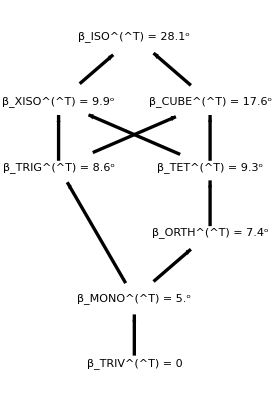

[T] = 1(206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

#### Rounded versions used in MSAT

```mathematica
Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[TmatMar17exact]],1]];
```

The Voigt matrix is (159.9 | -48.0 | -32.5 | 48.1 | -0.9 | 19.3
-48.0 | 284.1 | -124.1 | 32.2 | 2.4 | 19.7
-32.5 | -124.1 | 187.1 | -104.2 | -52.6 | -44.2
48.1 | 32.2 | -104.2 | 103.1 | -33.7 | 8.5
-0.9 | 2.4 | -52.6 | -33.7 | 176.4 | 16.1
19.3 | 19.7 | -44.2 | 8.5 | 16.1 | 171.9)

```mathematica
Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[TmatMar17]],1]];
```

The Voigt matrix is (159.9 | -48.0 | -32.4 | 48.1 | -0.9 | 19.3
-48.0 | 284.1 | -124.1 | 32.2 | 2.4 | 19.7
-32.4 | -124.1 | 187.1 | -104.1 | -52.5 | -44.2
48.1 | 32.2 | -104.1 | 103.1 | -33.7 | 8.5
-0.9 | 2.4 | -52.5 | -33.7 | 176.5 | 16.1
19.3 | 19.7 | -44.2 | 8.5 | 16.1 | 171.9)

#### U obtained from MSAT (use for node mode 1)

```mathematica
RfromMSATMar17=({{0.468078008543277, 0.261329948254664, 0.844162091107729}, {0.804629451471810, -0.520976355566523, -0.284877311776136}, {0.365341516587334, 0.812582485096645, -0.454131347929019}}); 
UfromMSATMar17 =Transpose[RfromMSATMar17];
```

```mathematica
RfromMSATMar17STIFF=({{-0.427114116100300, -0.789118875485163, 0.441435082634912}, {-0.745745521753299, 0.583505623551795, 0.321535074398317}, {-0.511309249488760, -0.191866066922902, -0.837705356166938}});
UfromMSATMar17STIFF =Transpose[RfromMSATMar17STIFF];
```

```mathematica
RfromMSATMar17STIFFwithCrounded=({{-0.4284, -0.7880, 0.4422}, {-0.7448, 0.5850, 0.3210}, {-0.5116, -0.1919, -0.8375}});
```

```mathematica
UfromMSATMar17STIFFwithCrounded=Transpose[RfromMSATMar17STIFFwithCrounded];
UfromMSATMar17STIFFwithCroundedmod=UfromMSATMar17STIFFwithCrounded.YRot[π].ZRot[-40Degree];
```

#### TmatMar17 - modified to have a more physical Poisson parameter (for closest ISO) The difference is that the (6,6) entry is 656 larger than the (6,6) entry of TmatMar17.

```mathematica
TISO=Closest[TmatMar17,ISO];
Tdiff=TmatMar17-TISO;
TISOmod=TISO; TISOmod[[6,6]]=730;
TmatMar17mod=Tdiff+TISOmod;
```

```mathematica
MatrixNote[TmatMar17mod]="T is Mar17mod"
MatrixShortNote[TmatMar17mod]="Mar17mod"
PrintVoigt[TmatMar17mod]
```

T is Mar17mod

Mar17mod

The [T]_𝔹𝔹 matrix is (206.2 | -67.4 | 17.1 | -15.9 | 166.6 | -19.5
-67.4 | 352.9 | 32.2 | 3.3 | 61.6 | -41.6
17.1 | 32.2 | 343.8 | 0.4 | 73.6 | -4.2
-15.9 | 3.3 | 0.4 | 270. | 88.8 | 13.3
166.6 | 61.6 | 73.6 | 88.8 | 287.1 | 30.7
-19.5 | -41.6 | -4.2 | 13.3 | 30.7 | 730.)

The eigenvalues are: {736.576,482.917,380.472,310.972,253.109,25.9528}

The Voigt matrix is (378.527 | 170.655 | 186.236 | 48.0824 | -0.850741 | 19.3318
170.655 | 502.784 | 94.5583 | 32.1824 | 2.44926 | 19.7318
186.236 | 94.5583 | 405.789 | -104.147 | -52.5479 | -44.2076
48.0824 | 32.1824 | -104.147 | 103.1 | -33.7 | 8.55
-0.850741 | 2.44926 | -52.5479 | -33.7 | 176.45 | 16.1
19.3318 | 19.7318 | -44.2076 | 8.55 | 16.1 | 171.9)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 350.334   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.344 = 19.68^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 730.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 146. and μ = 146., bulk modulus κ = 243.333, Poisson ratio = 0.25

```mathematica
(*cmin=0;cmax=20; dc=2;
contoursMONO[TmatMar17mod]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17mod]=cmax-dc;*)
```

#### differences in T and in C

```mathematica
MatrixForm[TmatMar17mod-TmatMar17]
MatrixForm[CmatOfTmat[TmatMar17mod]]
MatrixForm[CmatOfTmat[TmatMar17mod]-CmatOfTmat[TmatMar17]]
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 656.)

(378.527 | 170.655 | 186.236 | 48.0824 | -0.850741 | 19.3318
170.655 | 502.784 | 94.5583 | 32.1824 | 2.44926 | 19.7318
186.236 | 94.5583 | 405.789 | -104.147 | -52.5479 | -44.2076
48.0824 | 32.1824 | -104.147 | 103.1 | -33.7 | 8.55
-0.850741 | 2.44926 | -52.5479 | -33.7 | 176.45 | 16.1
19.3318 | 19.7318 | -44.2076 | 8.55 | 16.1 | 171.9)

(218.667 | 218.667 | 218.667 | 0. | 0. | 0.
218.667 | 218.667 | 218.667 | 0. | 0. | 0.
218.667 | 218.667 | 218.667 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

#### U obtained from MSAT (use for node mode 1)

```mathematica
RfromMSATMar17mod=({{-0.468078008543277, -0.261329948254664, -0.844162091107729}, {-0.804629451471809, 0.520976355566525, 0.284877311776135}, {0.365341516587337, 0.812582485096643, -0.454131347929020}}); 
UfromMSATMar17mod =Transpose[RfromMSATMar17mod];
```

## Maps from Tape and Tape (2024)

#### MONO map a (Eq. 57) - TmatJuly16

```mathematica
TT24MONOa=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 2, 1, 0}, {0, 0, 2, 4, 0, 0}, {0, 0, 1, 0, 5, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
MatrixNote[TT24MONOa]="T is TT24MONOa"
MatrixShortNote[TT24MONOa]="MONOa"
PrintVoigt[TT24MONOa]
```

T is TT24MONOa

MONOa

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 2 | 1 | 0
0 | 0 | 2 | 4 | 0 | 0
0 | 0 | 1 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)

The eigenvalues are: {6,6,3+√3,2,3-√3,1}

The Voigt matrix is (29/6 | 5/6 | 1/3 | 0 | 0 | 1/6 (-6+√3)
5/6 | 29/6 | 1/3 | 0 | 0 | 1/6 (6+√3)
1/3 | 1/3 | 16/3 | 0 | 0 | -1/(√3)
0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1/6 (-6+√3) | 1/6 (6+√3) | -1/(√3) | 0 | 0 | 3/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 2 √5   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.461 = 26.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 6.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1 and μ = 3/2, bulk modulus κ = 2, Poisson ratio = 1/5

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24MONOa]]]];
```

The Voigt matrix is (4.83333 | 0.833333 | 0.333333 | 0. | 0. | -0.711325
0.833333 | 4.83333 | 0.333333 | 0. | 0. | 1.28868
0.333333 | 0.333333 | 5.33333 | 0. | 0. | -0.57735
0. | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
-0.711325 | 1.28868 | -0.57735 | 0. | 0. | 1.5)

#### MONO map b (Eq. 59) - TmatJune8

```mathematica
TT24MONOb=({{28, -2, 0, 0, 0, 0}, {-2, 61, 0, 0, 0, 0}, {0, 0, 71, -4, 6, 8}, {0, 0, -4, 68, 10, 0}, {0, 0, 6, 10, 62, -3}, {0, 0, 8, 0, -3, 59}});
```

```mathematica
MatrixNote[TT24MONOb]="T is TT24MONOb"
MatrixShortNote[TT24MONOb]="MONOb"
PrintVoigt[TT24MONOb]
```

T is TT24MONOb

MONOb

The [T]_𝔹𝔹 matrix is (28 | -2 | 0 | 0 | 0 | 0
-2 | 61 | 0 | 0 | 0 | 0
0 | 0 | 71 | -4 | 6 | 8
0 | 0 | -4 | 68 | 10 | 0
0 | 0 | 6 | 10 | 62 | -3
0 | 0 | 8 | 0 | -3 | 59)

The eigenvalues are: {Root76.5Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,4]76.52870371540331,Root75.5Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,3]75.48673732504164,1/2 (89+√1105),Root59.2Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,2]59.22570612086892,Root48.8Root[16682408-1062803 #1+25080 #1^2-260 #1^3+#1^4&,1]48.758852838686124,1/2 (89-√1105)}

The Voigt matrix is (64-√2-10/(√3) | -4-√2 | -1+1/(√2)+10/(√3) | 0 | 0 | 2+4 √(2/3)+√3
-4-√2 | 64-√2+10/(√3) | -1+1/(√2)-10/(√3) | 0 | 0 | -2+4 √(2/3)+√3
-1+1/(√2)+10/(√3) | -1+1/(√2)-10/(√3) | 61+2 √2 | 0 | 0 | (-6+4 √2)/(√3)
0 | 0 | 0 | 14 | -1 | 0
0 | 0 | 0 | -1 | 61/2 | 0
2+4 √(2/3)+√3 | -2+4 √(2/3)+√3 | (-6+4 √2)/(√3) | 0 | 0 | 71/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 2 √413   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.278 = 15.92^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (58. | 0. | 0. | 0. | 0. | 0.
0. | 58. | 0. | 0. | 0. | 0.
0. | 0. | 58. | 0. | 0. | 0.
0. | 0. | 0. | 58. | 0. | 0.
0. | 0. | 0. | 0. | 58. | 0.
0. | 0. | 0. | 0. | 0. | 59.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1/3 and μ = 29, bulk modulus κ = 59/3, Poisson ratio = 1/176

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24MONOb]]]];
```

The Voigt matrix is (56.8123 | -5.41421 | 5.48061 | 0. | 0. | 6.99804
-5.41421 | 68.3593 | -6.0664 | 0. | 0. | 2.99804
5.48061 | -6.0664 | 63.8284 | 0. | 0. | -0.198115
0. | 0. | 0. | 14. | -1. | 0.
0. | 0. | 0. | -1. | 30.5 | 0.
6.99804 | 2.99804 | -0.198115 | 0. | 0. | 35.5)

#### ORTH map a (Eq. 62) - TmatJune12

```mathematica
TT24ORTHa=({{86, 0, 0, 0, 0, 0}, {0, 51, 0, 0, 0, 0}, {0, 0, 32, 0, 0, 0}, {0, 0, 0, 46, -20, 13}, {0, 0, 0, -20, 45, -2}, {0, 0, 0, 13, -2, 87}});
```

```mathematica
MatrixNote[TT24ORTHa]="T is TT24ORTHa"
MatrixShortNote[TT24ORTHa]="ORTHa"
PrintVoigt[TT24ORTHa]
```

T is TT24ORTHa

ORTHa

The [T]_𝔹𝔹 matrix is (86 | 0 | 0 | 0 | 0 | 0
0 | 51 | 0 | 0 | 0 | 0
0 | 0 | 32 | 0 | 0 | 0
0 | 0 | 0 | 46 | -20 | 13
0 | 0 | 0 | -20 | 45 | -2
0 | 0 | 0 | 13 | -2 | 87)

The eigenvalues are: {Root92.2Root[-138541+9414 #1-178 #1^2+#1^3&,3]92.17238684956311,86,Root61.3Root[-138541+9414 #1-178 #1^2+#1^3&,2]61.31301189642678,51,32,Root24.5Root[-138541+9414 #1-178 #1^2+#1^3&,1]24.514601254010113}

The Voigt matrix is (1/6 (357-4 √2+40 √3-26 √6) | 1/6 (81-4 √2) | 1/6 (84+2 √2-40 √3-13 √6) | 0 | 0 | 0
1/6 (81-4 √2) | 1/6 (357-4 √2-40 √3+26 √6) | 1/6 (84+2 √2+40 √3+13 √6) | 0 | 0 | 0
1/6 (84+2 √2-40 √3-13 √6) | 1/6 (84+2 √2+40 √3+13 √6) | 59+(4 √2)/3 | 0 | 0 | 0
0 | 0 | 0 | 43 | 0 | 0
0 | 0 | 0 | 0 | 51/2 | 0
0 | 0 | 0 | 0 | 0 | 16)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 2 √697   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.349 = 19.98^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (52. | 0. | 0. | 0. | 0. | 0.
0. | 52. | 0. | 0. | 0. | 0.
0. | 0. | 52. | 0. | 0. | 0.
0. | 0. | 0. | 52. | 0. | 0.
0. | 0. | 0. | 0. | 52. | 0.
0. | 0. | 0. | 0. | 0. | 87.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35/3 and μ = 26, bulk modulus κ = 29, Poisson ratio = 35/226

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24ORTHa]]]]
```

The Voigt matrix is (59.4897 | 12.5572 | -2.38283 | 0. | 0. | 0.
12.5572 | 57.6246 | 31.3256 | 0. | 0. | 0.
-2.38283 | 31.3256 | 60.8856 | 0. | 0. | 0.
0. | 0. | 0. | 43. | 0. | 0.
0. | 0. | 0. | 0. | 25.5 | 0.
0. | 0. | 0. | 0. | 0. | 16.)

#### ORTH map b (Eq. 77a) - ORTHtest (BC_BrowaeysChevrotNotes.nb)

```mathematica
TT24ORTHb=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24ORTHb]="T is TT24ORTHb"
MatrixShortNote[TT24ORTHb]="ORTHb"
PrintVoigt[TT24ORTHb]
```

T is TT24ORTHb

ORTHb

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {5,2,1,1,1,1}

The Voigt matrix is (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 5/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 2 √3   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.647 = 37.09^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -1/3 and μ = 1, bulk modulus κ = 1/3, Poisson ratio = -1/4

#### TET map a (Eq. 65) - TmatJuly22TET

```mathematica
TT24TETa=({{60, 0, 0, 0, 0, 0}, {0, 60, 0, 0, 0, 0}, {0, 0, 15, 0, 0, 0}, {0, 0, 0, 71, 0, 0}, {0, 0, 0, 0, 58, 6}, {0, 0, 0, 0, 6, 15}});
```

```mathematica
MatrixNote[TT24TETa]="T is TT24TETa"
MatrixShortNote[TT24TETa]="TETa"
PrintVoigt[TT24TETa]
```

T is TT24TETa

TETa

The [T]_𝔹𝔹 matrix is (60 | 0 | 0 | 0 | 0 | 0
0 | 60 | 0 | 0 | 0 | 0
0 | 0 | 15 | 0 | 0 | 0
0 | 0 | 0 | 71 | 0 | 0
0 | 0 | 0 | 0 | 58 | 6
0 | 0 | 0 | 0 | 6 | 15)

The eigenvalues are: {71,60,60,1/2 (73+√1993),15,1/2 (73-√1993)}

The Voigt matrix is (301/6+2 √2 | -125/6+2 √2 | -43/3-√2 | 0 | 0 | 0
-125/6+2 √2 | 301/6+2 √2 | -43/3-√2 | 0 | 0 | 0
-43/3-√2 | -43/3-√2 | 131/3-4 √2 | 0 | 0 | 0
0 | 0 | 0 | 30 | 0 | 0
0 | 0 | 0 | 0 | 30 | 0
0 | 0 | 0 | 0 | 0 | 15/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √(9814/5)   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.356 = 20.42^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (52.8 | 0. | 0. | 0. | 0. | 0.
0. | 52.8 | 0. | 0. | 0. | 0.
0. | 0. | 52.8 | 0. | 0. | 0.
0. | 0. | 0. | 52.8 | 0. | 0.
0. | 0. | 0. | 0. | 52.8 | 0.
0. | 0. | 0. | 0. | 0. | 15.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -63/5 and μ = 132/5, bulk modulus κ = 5, Poisson ratio = -21/46

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24TETa]]]]
```

The Voigt matrix is (52.9951 | -18.0049 | -15.7475 | 0. | 0. | 0.
-18.0049 | 52.9951 | -15.7475 | 0. | 0. | 0.
-15.7475 | -15.7475 | 38.0098 | 0. | 0. | 0.
0. | 0. | 0. | 30. | 0. | 0.
0. | 0. | 0. | 0. | 30. | 0.
0. | 0. | 0. | 0. | 0. | 7.5)

#### TET map b (Eq. 67) - TmatSep6TET

```mathematica
TT24TETb=({{2, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24TETb]="T is TT24TETb"
MatrixShortNote[TT24TETb]="TETb"
PrintVoigt[TT24TETb]
```

T is TT24TETb

TETb

The [T]_𝔹𝔹 matrix is (2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {3,2,2,2,1,1}

The Voigt matrix is (7/6 | 1/6 | -1/3 | 0 | 0 | 0
1/6 | 7/6 | -1/3 | 0 | 0 | 0
-1/3 | -1/3 | 5/3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 3/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √2   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.299 = 17.15^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -1/3 and μ = 1, bulk modulus κ = 1/3, Poisson ratio = -1/4

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24TETb]]]]
```

The Voigt matrix is (1.16667 | 0.166667 | -0.333333 | 0. | 0. | 0.
0.166667 | 1.16667 | -0.333333 | 0. | 0. | 0.
-0.333333 | -0.333333 | 1.66667 | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1.5)

#### XISO maps in Figure 6 (see BC_TsubXISO_2024-01-26.nb)

#### two reference matrices

```mathematica
Tmat1=TmatForXISO/.{a->1.,c->2.,e->3.,f->4.,k->0};
Tmat2=TmatForXISO/.{a->1.,c->1.5,e->2.3,f->3.5,k->0};
MatrixForm[Tmat1]
MatrixForm[Tmat2]
```

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 2. | 0 | 0 | 0
0 | 0 | 0 | 2. | 0 | 0
0 | 0 | 0 | 0 | 3. | 0
0 | 0 | 0 | 0 | 0 | 4.)

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1.5 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 0 | 0
0 | 0 | 0 | 0 | 2.3 | 0
0 | 0 | 0 | 0 | 0 | 3.5)

#### two U

```mathematica
θ1=-60.Degree;
ϕ1=30.Degree;
U1=UsHat[{θ1,0,ϕ1}];
θ2=40.Degree;
ϕ2=40.Degree;
U2=UsHat[{θ2,0,ϕ2}];
DispMat[U1,3]
DispMat[U2,3]
```

(0.433 | 0.866 | 0.250
-0.750 | 0.500 | -0.433
-0.500 | 0 | 0.866)

(0.587 | -0.643 | 0.492
0.492 | 0.766 | 0.413
-0.643 | 0 | 0.766)

#### four maps (from left to right in Figure 6)

```mathematica
TT24XISOa=Conj[Tmat2,U1];
TT24XISOb=Conj[Tmat1,U1];
TT24XISOc=Conj[Tmat1,U2];
TT24XISOd=Conj[Tmat2,U2];
```

```mathematica
(*optionsX ={ViewPoint->20xyztp[{0,70}],Lighting->{{"Ambient",White}},Boxed->False};
contoursX=contours[TT24XISOc,MONO]
MaxForScalingX=MaxForScaling[TT24XISOc,MONO]
MaxForScalingX=contoursX[[-1]]
Show[cpMONO[TT24XISOa,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOb,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOc,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOd,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]*)
```

```mathematica
PrintVoigt[TT24XISOa]
```

The [T]_𝔹𝔹 matrix is (1.65 | -0.303109 | 0.0703646 | 0.084375 | 0.487139 | 0
-0.303109 | 1.3 | 0.084375 | 0.167792 | -0.28125 | 0
0.0703646 | 0.084375 | 1.42656 | -0.0297696 | 0.234375 | 0
0.084375 | 0.167792 | -0.0297696 | 1.39219 | -0.135316 | 0
0.487139 | -0.28125 | 0.234375 | -0.135316 | 1.53125 | 0
0 | 0 | 0 | 0 | 0 | 3.5)

The eigenvalues are: {3.5,2.3,1.5,1.5,1.,1.}

The Voigt matrix is (2.19609 | 0.725781 | 0.578125 | 0.0984375 | -0.165086 | 0.082543
0.725781 | 2.03984 | 0.734375 | 0.182813 | 0.00270633 | 0.0527734
0.578125 | 0.734375 | 2.1875 | -0.28125 | 0.16238 | -0.135316
0.0984375 | 0.182813 | -0.28125 | 0.825 | -0.151554 | 0.0351823
-0.165086 | 0.00270633 | 0.16238 | -0.151554 | 0.65 | 0.0421875
0.082543 | 0.0527734 | -0.135316 | 0.0351823 | 0.0421875 | 0.713281)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 1.06395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.219 = 12.53^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.46 | 0. | 0. | 0. | 0. | 0.
0. | 1.46 | 0. | 0. | 0. | 0.
0. | 0. | 1.46 | 0. | 0. | 0.
0. | 0. | 0. | 1.46 | 0. | 0.
0. | 0. | 0. | 0. | 1.46 | 0.
0. | 0. | 0. | 0. | 0. | 3.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.68 and μ = 0.73, bulk modulus κ = 1.16667, Poisson ratio = 0.241135

```mathematica
PrintVoigt[TT24XISOb]
```

The [T]_𝔹𝔹 matrix is (2.04687 | -0.460076 | 0.0676582 | 0.210937 | 0.730709 | 0
-0.460076 | 1.51562 | 0.210937 | 0.311228 | -0.421875 | 0
0.0676582 | 0.210937 | 1.83203 | -0.0473608 | 0.398437 | 0
0.210937 | 0.311228 | -0.0473608 | 1.77734 | -0.230038 | 0
0.730709 | -0.421875 | 0.398437 | -0.230038 | 1.82813 | 0
0 | 0 | 0 | 0 | 0 | 4.)

The eigenvalues are: {4.,3.,2.,2.,1.,1.}

The Voigt matrix is (2.65951 | 0.749349 | 0.591146 | 0.105469 | -0.277399 | 0.138699
0.749349 | 2.39388 | 0.856771 | 0.316406 | 0.0338291 | 0.0913386
0.591146 | 0.856771 | 2.55208 | -0.421875 | 0.24357 | -0.230038
0.105469 | 0.316406 | -0.421875 | 1.02344 | -0.230038 | 0.0338291
-0.277399 | 0.0338291 | 0.24357 | -0.230038 | 0.757812 | 0.105469
0.138699 | 0.0913386 | -0.230038 | 0.0338291 | 0.105469 | 0.916016)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 1.67332   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.287 = 16.43^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.8 | 0. | 0. | 0. | 0. | 0.
0. | 1.8 | 0. | 0. | 0. | 0.
0. | 0. | 1.8 | 0. | 0. | 0.
0. | 0. | 0. | 1.8 | 0. | 0.
0. | 0. | 0. | 0. | 1.8 | 0.
0. | 0. | 0. | 0. | 0. | 4.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.733333 and μ = 0.9, bulk modulus κ = 1.33333, Poisson ratio = 0.22449

```mathematica
PrintVoigt[TT24XISOc]
```

The [T]_𝔹𝔹 matrix is (1.94372 | 0.632274 | 0.0735548 | -0.395992 | -0.303647 | 0
0.632274 | 2.16669 | 0.220681 | 0.282482 | -0.361872 | 0
0.0735548 | 0.220681 | 1.87657 | -0.0510893 | -0.547565 | 0
-0.395992 | 0.282482 | -0.0510893 | 1.59583 | 0.0965505 | 0
-0.303647 | -0.361872 | -0.547565 | 0.0965505 | 1.41719 | 0
0 | 0 | 0 | 0 | 0 | 4.)

The eigenvalues are: {4.,3.,2.,2.,1.,1.}

The Voigt matrix is (2.31171 | 0.771616 | 0.916679 | 0.110341 | -0.245704 | -0.132524
0.771616 | 2.42319 | 0.805192 | -0.285651 | 0.0367774 | -0.183613
0.916679 | 0.805192 | 2.27813 | 0.175311 | 0.208927 | 0.316137
0.110341 | -0.285651 | 0.175311 | 0.971858 | 0.316137 | 0.0367774
-0.245704 | 0.0367774 | 0.208927 | 0.316137 | 1.08335 | 0.110341
-0.132524 | -0.183613 | 0.316137 | 0.0367774 | 0.110341 | 0.938283)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 1.67332   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.287 = 16.43^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.8 | 0. | 0. | 0. | 0. | 0.
0. | 1.8 | 0. | 0. | 0. | 0.
0. | 0. | 1.8 | 0. | 0. | 0.
0. | 0. | 0. | 1.8 | 0. | 0.
0. | 0. | 0. | 0. | 1.8 | 0.
0. | 0. | 0. | 0. | 0. | 4.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.733333 and μ = 0.9, bulk modulus κ = 1.33333, Poisson ratio = 0.22449

```mathematica
PrintVoigt[TT24XISOd]
```

The [T]_𝔹𝔹 matrix is (1.56202 | 0.423587 | 0.094732 | -0.208215 | -0.214359 | 0
0.423587 | 1.7114 | 0.179408 | 0.129062 | -0.255463 | 0
0.094732 | 0.179408 | 1.47554 | -0.0321133 | -0.313979 | 0
-0.208215 | 0.129062 | -0.0321133 | 1.29907 | 0.055363 | 0
-0.214359 | -0.255463 | -0.313979 | 0.055363 | 1.25197 | 0
0 | 0 | 0 | 0 | 0 | 3.5)

The eigenvalues are: {3.5,2.3,1.5,1.5,1.,1.}

The Voigt matrix is (1.9929 | 0.725791 | 0.781307 | 0.0422275 | -0.138277 | -0.0745814
0.725791 | 2.05683 | 0.717379 | -0.165987 | -0.0092145 | -0.106695
0.781307 | 0.717379 | 2.00131 | 0.12376 | 0.147491 | 0.181276
0.0422275 | -0.165987 | 0.12376 | 0.78101 | 0.211793 | 0.047366
-0.138277 | -0.0092145 | 0.147491 | 0.211793 | 0.8557 | 0.0897041
-0.0745814 | -0.106695 | 0.181276 | 0.047366 | 0.0897041 | 0.737768)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 1.06395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.219 = 12.53^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.46 | 0. | 0. | 0. | 0. | 0.
0. | 1.46 | 0. | 0. | 0. | 0.
0. | 0. | 1.46 | 0. | 0. | 0.
0. | 0. | 0. | 1.46 | 0. | 0.
0. | 0. | 0. | 0. | 1.46 | 0.
0. | 0. | 0. | 0. | 0. | 3.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.68 and μ = 0.73, bulk modulus κ = 1.16667, Poisson ratio = 0.241135

## Maps from Tape and Tape (2022) – see ES_RefMatricesForCollage.nb

## Maps from Tape and Tape (2021)

#### TRIV (Eq. 23)

```mathematica
TT21TRIVnodenom=({{5, 0, 0, -2, 0, 0}, {0, 6, 0, 0, -2, 0}, {0, 0, 5, 0, 0, 0}, {-2, 0, 0, 5, 0, 0}, {0, -2, 0, 0, 6, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
denominator=5;
TT21TRIV=1/denominator TT21TRIVnodenom;
```

```mathematica
MatrixNote[TT21TRIV]="T is TT21TRIV"
MatrixShortNote[TT21TRIV]="TRIV"
PrintVoigt[TT21TRIV]
```

T is TT21TRIV

TRIV

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | -2/5 | 0 | 0
0 | 6/5 | 0 | 0 | -2/5 | 0
0 | 0 | 1 | 0 | 0 | 0
-2/5 | 0 | 0 | 1 | 0 | 0
0 | -2/5 | 0 | 0 | 6/5 | 0
0 | 0 | 0 | 0 | 0 | 6/5)

The eigenvalues are: {8/5,7/5,6/5,1,4/5,3/5}

The Voigt matrix is (11/10 | 1/10 | 0 | 1/5 | -1/(5 √3) | 0
1/10 | 11/10 | 0 | -1/5 | -1/(5 √3) | 0
0 | 0 | 6/5 | 0 | 2/(5 √3) | 0
1/5 | -1/5 | 0 | 1/2 | 0 | 0
-1/(5 √3) | -1/(5 √3) | 2/(5 √3) | 0 | 3/5 | 0
0 | 0 | 0 | 0 | 0 | 1/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = (√(86/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.298 = 17.1^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.08 | 0. | 0. | 0. | 0. | 0.
0. | 1.08 | 0. | 0. | 0. | 0.
0. | 0. | 1.08 | 0. | 0. | 0.
0. | 0. | 0. | 1.08 | 0. | 0.
0. | 0. | 0. | 0. | 1.08 | 0.
0. | 0. | 0. | 0. | 0. | 1.2)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1/25 and μ = 27/50, bulk modulus κ = 2/5, Poisson ratio = 1/29

#### lattice for TT21TRIV:

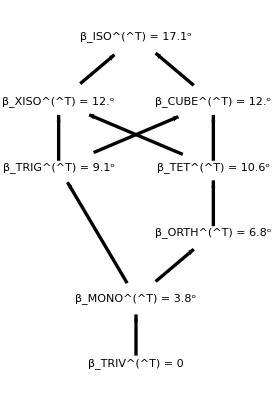

[T] = 1/5(5 | 0 | 0 | -2 | 0 | 0
0 | 6 | 0 | 0 | -2 | 0
0 | 0 | 5 | 0 | 0 | 0
-2 | 0 | 0 | 5 | 0 | 0
0 | -2 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 6)

#### MONO (Section 15.1)

```mathematica
denominator=80;
TT21MONO=1/denominator({{222, -12 √6, -82, 21 √6, -39 √2, 0}, {-12 √6, 196, 12 √6, 30, 10 √3, -16}, {-82, 12 √6, 222, 9 √6, -51 √2, 0}, {21 √6, 30, 9 √6, 242, -6 √3, -24}, {-39 √2, 10 √3, -51 √2, -6 √3, 254, -8 √3}, {0, -16, 0, -24, -8 √3, 304}});
```

```mathematica
MatrixNote[TT21MONO]="T is TT21MONO"
MatrixShortNote[TT21MONO]="MONO"
PrintVoigt[TT21MONO]
MatrixForm[N[TT21MONO]]
```

T is TT21MONO

MONO

The [T]_𝔹𝔹 matrix is (111/40 | -(3 √(3/2))/10 | -41/40 | (21 √(3/2))/40 | -39/(40 √2) | 0
-(3 √(3/2))/10 | 49/20 | (3 √(3/2))/10 | 3/8 | (√3)/8 | -1/5
-41/40 | (3 √(3/2))/10 | 111/40 | (9 √(3/2))/40 | -51/(40 √2) | 0
(21 √(3/2))/40 | 3/8 | (9 √(3/2))/40 | 121/40 | -(3 √3)/40 | -3/10
-39/(40 √2) | (√3)/8 | -51/(40 √2) | -(3 √3)/40 | 127/40 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 19/5)

The eigenvalues are: {4,4,4,3,2,1}

The Voigt matrix is (1/60 (203+4 √6) | 1/60 (17-2 √6) | 1/15 (2+√6) | -(17 √(3/2))/40 | -1/8-1/(5 √6) | -(13 √(3/2))/40
1/60 (17-2 √6) | 1/30 (97-4 √6) | 1/60 (17-2 √6) | (√(3/2))/10 | 1/4-1/(5 √6) | -(√(3/2))/10
1/15 (2+√6) | 1/60 (17-2 √6) | 1/60 (203+4 √6) | (13 √(3/2))/40 | -1/8-1/(5 √6) | (17 √(3/2))/40
-(17 √(3/2))/40 | (√(3/2))/10 | (13 √(3/2))/40 | 111/80 | -(3 √(3/2))/20 | -41/80
-1/8-1/(5 √6) | 1/4-1/(5 √6) | -1/8-1/(5 √6) | -(3 √(3/2))/20 | 49/40 | (3 √(3/2))/20
-(13 √(3/2))/40 | -(√(3/2))/10 | (17 √(3/2))/40 | -41/80 | (3 √(3/2))/20 | 111/80)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = (2 √(226/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.349 = 19.97^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.84 | 0. | 0. | 0. | 0. | 0.
0. | 2.84 | 0. | 0. | 0. | 0.
0. | 0. | 2.84 | 0. | 0. | 0.
0. | 0. | 0. | 2.84 | 0. | 0.
0. | 0. | 0. | 0. | 2.84 | 0.
0. | 0. | 0. | 0. | 0. | 3.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/25 and μ = 71/50, bulk modulus κ = 19/15, Poisson ratio = 8/87

(2.775 | -0.367423 | -1.025 | 0.642991 | -0.689429 | 0.
-0.367423 | 2.45 | 0.367423 | 0.375 | 0.216506 | -0.2
-1.025 | 0.367423 | 2.775 | 0.275568 | -0.901561 | 0.
0.642991 | 0.375 | 0.275568 | 3.025 | -0.129904 | -0.3
-0.689429 | 0.216506 | -0.901561 | -0.129904 | 3.175 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 3.8)

#### lattice for TT21MONO:

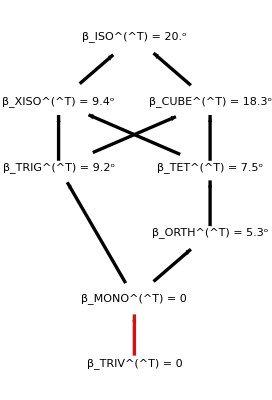

[T] = 1/80(222 | -12 √6 | -82 | 21 √6 | -39 √2 | 0
-12 √6 | 196 | 12 √6 | 30 | 10 √3 | -16
-82 | 12 √6 | 222 | 9 √6 | -51 √2 | 0
21 √6 | 30 | 9 √6 | 242 | -6 √3 | -24
-39 √2 | 10 √3 | -51 √2 | -6 √3 | 254 | -8 √3
0 | -16 | 0 | -24 | -8 √3 | 304)

#### ORTH (Section 15.2)

```mathematica
denominator=10;
TT21ORTH=1/denominator({{38, 18, 3 √2, -5 √2, -√6, -√8}, {18, 38, 3 √2, 5 √2, -√6, -√8}, {3 √2, 3 √2, 41, 0, -7 √3, 6}, {-5 √2, 5 √2, 0, 20, 0, 0}, {-√6, -√6, -7 √3, 0, 27, -2 √3}, {-√8, -√8, 6, 0, -2 √3, 56}});
```

```mathematica
MatrixNote[TT21ORTH]="T is TT21ORTH"
MatrixShortNote[TT21ORTH]="ORTH"
PrintVoigt[TT21ORTH]
MatrixForm[N[TT21ORTH]]
```

T is TT21ORTH

ORTH

The [T]_𝔹𝔹 matrix is (19/5 | 9/5 | 3/(5 √2) | -1/(√2) | -(√(3/2))/5 | -(√2)/5
9/5 | 19/5 | 3/(5 √2) | 1/(√2) | -(√(3/2))/5 | -(√2)/5
3/(5 √2) | 3/(5 √2) | 41/10 | 0 | -(7 √3)/10 | 3/5
-1/(√2) | 1/(√2) | 0 | 2 | 0 | 0
-(√(3/2))/5 | -(√(3/2))/5 | -(7 √3)/10 | 0 | 27/10 | -(√3)/5
-(√2)/5 | -(√2)/5 | 3/5 | 0 | -(√3)/5 | 28/5)

The eigenvalues are: {6,6,4,3,2,1}

The Voigt matrix is (1/60 (199-4 √6) | 1/60 (79-4 √6) | 1/30 (29+√6) | -(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | 1/20 (-7+2 √6)
1/60 (79-4 √6) | 1/60 (199-4 √6) | 1/30 (29+√6) | -(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | 1/20 (-7+2 √6)
1/30 (29+√6) | 1/30 (29+√6) | 1/15 (55+2 √6) | -(-3+√6)/(15 √2) | -(-3+√6)/(15 √2) | 1/10 (7+√6)
-(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | -(-3+√6)/(15 √2) | 19/10 | 9/10 | 3/(10 √2)
-(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | -(-3+√6)/(15 √2) | 9/10 | 19/10 | 3/(10 √2)
1/20 (-7+2 √6) | 1/20 (-7+2 √6) | 1/10 (7+√6) | 3/(10 √2) | 3/(10 √2) | 41/20)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = (9 √(26/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.419 = 23.98^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3.28 | 0. | 0. | 0. | 0. | 0.
0. | 3.28 | 0. | 0. | 0. | 0.
0. | 0. | 3.28 | 0. | 0. | 0.
0. | 0. | 0. | 3.28 | 0. | 0.
0. | 0. | 0. | 0. | 3.28 | 0.
0. | 0. | 0. | 0. | 0. | 5.6)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 58/75 and μ = 41/25, bulk modulus κ = 28/15, Poisson ratio = 29/181

(3.8 | 1.8 | 0.424264 | -0.707107 | -0.244949 | -0.282843
1.8 | 3.8 | 0.424264 | 0.707107 | -0.244949 | -0.282843
0.424264 | 0.424264 | 4.1 | 0. | -1.21244 | 0.6
-0.707107 | 0.707107 | 0. | 2. | 0. | 0.
-0.244949 | -0.244949 | -1.21244 | 0. | 2.7 | -0.34641
-0.282843 | -0.282843 | 0.6 | 0. | -0.34641 | 5.6)

#### lattice for TT21ORTH:

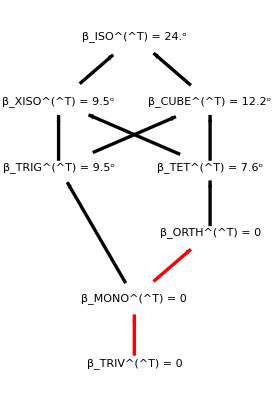

[T] = 1/10(38 | 18 | 3 √2 | -5 √2 | -√6 | -2 √2
18 | 38 | 3 √2 | 5 √2 | -√6 | -2 √2
3 √2 | 3 √2 | 41 | 0 | -7 √3 | 6
-5 √2 | 5 √2 | 0 | 20 | 0 | 0
-√6 | -√6 | -7 √3 | 0 | 27 | -2 √3
-2 √2 | -2 √2 | 6 | 0 | -2 √3 | 56)

#### TET (Section 15.3)

```mathematica
denominator=64;
TT21TET=1/denominator({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
```

```mathematica
MatrixNote[TT21TET]="T is TT21TET"
MatrixShortNote[TT21TET]="TET"
PrintVoigt[TT21TET]
MatrixForm[N[TT21TET]]
```

T is TT21TET

TET

The [T]_𝔹𝔹 matrix is (21/8 | (√(3/2))/8 | -5/8 | (3 √(3/2))/16 | 3/(16 √2) | 0
(√(3/2))/8 | 81/16 | -(√(3/2))/8 | -21/32 | -(7 √3)/32 | (√3)/4
-5/8 | -(√(3/2))/8 | 21/8 | -(3 √(3/2))/16 | -3/(16 √2) | 0
(3 √(3/2))/16 | -21/32 | -(3 √(3/2))/16 | 233/64 | (35 √3)/64 | -(√3)/8
3/(16 √2) | -(7 √3)/32 | -3/(16 √2) | (35 √3)/64 | 163/64 | -1/8
0 | (√3)/4 | 0 | -(√3)/8 | -1/8 | 11/2)

The eigenvalues are: {6,5,4,3,2,2}

The Voigt matrix is (1/96 (339+8 √2) | 1/48 (21-2 √2) | 1/96 (147+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
1/48 (21-2 √2) | 37/8-1/(3 √2) | 1/48 (21-2 √2) | (√(3/2))/8 | 1/16 (-7+2 √2) | -(√(3/2))/8
1/96 (147+8 √2) | 1/48 (21-2 √2) | 1/96 (339+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
-(√(3/2))/16 | (√(3/2))/8 | -(√(3/2))/16 | 21/16 | (√(3/2))/16 | -5/16
1/32 (7+4 √2) | 1/16 (-7+2 √2) | 1/32 (7+4 √2) | (√(3/2))/16 | 81/32 | -(√(3/2))/16
(√(3/2))/16 | -(√(3/2))/8 | (√(3/2))/16 | -5/16 | -(√(3/2))/16 | 21/16)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √(93/10)   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.32 = 18.33^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (3.3 | 0. | 0. | 0. | 0. | 0.
0. | 3.3 | 0. | 0. | 0. | 0.
0. | 0. | 3.3 | 0. | 0. | 0.
0. | 0. | 0. | 3.3 | 0. | 0.
0. | 0. | 0. | 0. | 3.3 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 11/15 and μ = 33/20, bulk modulus κ = 11/6, Poisson ratio = 2/13

(2.625 | 0.153093 | -0.625 | 0.22964 | 0.132583 | 0.
0.153093 | 5.0625 | -0.153093 | -0.65625 | -0.378886 | 0.433013
-0.625 | -0.153093 | 2.625 | -0.22964 | -0.132583 | 0.
0.22964 | -0.65625 | -0.22964 | 3.64063 | 0.947215 | -0.216506
0.132583 | -0.378886 | -0.132583 | 0.947215 | 2.54688 | -0.125
0. | 0.433013 | 0. | -0.216506 | -0.125 | 5.5)

#### lattice for TT21TET:

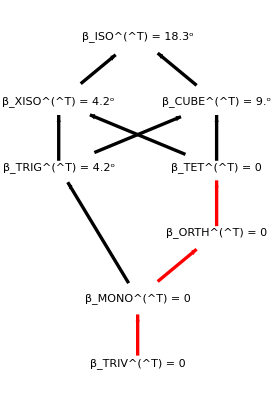

[T] = 1/64(168 | 4 √6 | -40 | 6 √6 | 6 √2 | 0
4 √6 | 324 | -4 √6 | -42 | -14 √3 | 16 √3
-40 | -4 √6 | 168 | -6 √6 | -6 √2 | 0
6 √6 | -42 | -6 √6 | 233 | 35 √3 | -8 √3
6 √2 | -14 √3 | -6 √2 | 35 √3 | 163 | -8
0 | 16 √3 | 0 | -8 √3 | -8 | 352)

#### XISO (Section 15.4)

```mathematica
denominator=128;
TT21XISO=1/denominator({{532, 92 √3, 122, -2 √3, -60, 48}, {92 √3, 348, -2 √3, 126, -20 √3, 16 √3}, {122, -2 √3, 349, 31 √3, -126, 24}, {-2 √3, 126, 31 √3, 287, -42 √3, 8 √3}, {-60, -20 √3, -126, -42 √3, 212, -16}, {48, 16 √3, 24, 8 √3, -16, 704}});
```

```mathematica
MatrixNote[TT21XISO]="T is TT21XISO"
MatrixShortNote[TT21XISO]="XISO"
PrintVoigt[TT21XISO]
MatrixForm[N[TT21XISO]]
```

T is TT21XISO

XISO

The [T]_𝔹𝔹 matrix is (133/32 | (23 √3)/32 | 61/64 | -(√3)/64 | -15/32 | 3/8
(23 √3)/32 | 87/32 | -(√3)/64 | 63/64 | -(5 √3)/32 | (√3)/8
61/64 | -(√3)/64 | 349/128 | (31 √3)/128 | -63/64 | 3/16
-(√3)/64 | 63/64 | (31 √3)/128 | 287/128 | -(21 √3)/64 | (√3)/16
-15/32 | -(5 √3)/32 | -63/64 | -(21 √3)/64 | 53/32 | -1/8
3/8 | (√3)/8 | 3/16 | (√3)/16 | -1/8 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/768 (2733-80 √2) | 1/768 (759-32 √2) | 1/192 (183-2 √2) | 1/128 √3 (-9+8 √2) | 1/128 (-73+8 √2) | 1/256 √3 (-73+8 √2)
1/768 (759-32 √2) | 1/768 (2229+16 √2) | 1/192 (309+10 √2) | 1/128 √3 (-11+8 √2) | 1/128 (53+8 √2) | 1/256 √3 (-11+8 √2)
1/192 (183-2 √2) | 1/192 (309+10 √2) | 1/48 (141+4 √2) | 1/32 √(3/2) (4+5 √2) | 1/32 (5+2 √2) | 1/64 √(3/2) (4+21 √2)
1/128 √3 (-9+8 √2) | 1/128 √3 (-11+8 √2) | 1/32 √(3/2) (4+5 √2) | 133/64 | (23 √3)/64 | 61/128
1/128 (-73+8 √2) | 1/128 (53+8 √2) | 1/32 (5+2 √2) | (23 √3)/64 | 87/64 | -(√3)/128
1/256 √3 (-73+8 √2) | 1/256 √3 (-11+8 √2) | 1/64 √(3/2) (4+21 √2) | 61/128 | -(√3)/128 | 349/256)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √(143/10)   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.434 = 24.85^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, bulk modulus κ = 11/6, Poisson ratio = 28/137

(4.15625 | 1.24491 | 0.953125 | -0.0270633 | -0.46875 | 0.375
1.24491 | 2.71875 | -0.0270633 | 0.984375 | -0.270633 | 0.216506
0.953125 | -0.0270633 | 2.72656 | 0.419481 | -0.984375 | 0.1875
-0.0270633 | 0.984375 | 0.419481 | 2.24219 | -0.568329 | 0.108253
-0.46875 | -0.270633 | -0.984375 | -0.568329 | 1.65625 | -0.125
0.375 | 0.216506 | 0.1875 | 0.108253 | -0.125 | 5.5)

#### lattice for TT21XISO:

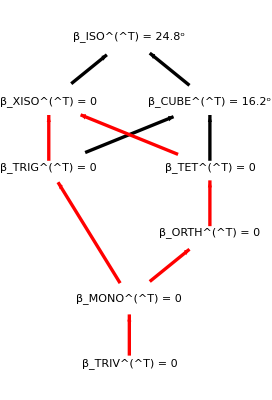

[T] = 1/128(532 | 92 √3 | 122 | -2 √3 | -60 | 48
92 √3 | 348 | -2 √3 | 126 | -20 √3 | 16 √3
122 | -2 √3 | 349 | 31 √3 | -126 | 24
-2 √3 | 126 | 31 √3 | 287 | -42 √3 | 8 √3
-60 | -20 √3 | -126 | -42 √3 | 212 | -16
48 | 16 √3 | 24 | 8 √3 | -16 | 704)

#### CUBE (Section 15.5)

```mathematica
denominator=36;
TT21CUBE=1/denominator({{52, 4, 16, -6, -2 √3, 0}, {4, 64, 4, 12, 4 √3, 0}, {16, 4, 52, -6, -2 √3, 0}, {-6, 12, -6, 45, 3 √3, 0}, {-2 √3, 4 √3, -2 √3, 3 √3, 39, 0}, {0, 0, 0, 0, 0, 108}});
```

```mathematica
MatrixNote[TT21CUBE]="T is TT21CUBE"
MatrixShortNote[TT21CUBE]="CUBE"
PrintVoigt[TT21CUBE]
MatrixForm[N[TT21CUBE]]
```

T is TT21CUBE

CUBE

The [T]_𝔹𝔹 matrix is (13/9 | 1/9 | 4/9 | -1/6 | -1/(6 √3) | 0
1/9 | 16/9 | 1/9 | 1/3 | 1/(3 √3) | 0
4/9 | 1/9 | 13/9 | -1/6 | -1/(6 √3) | 0
-1/6 | 1/3 | -1/6 | 5/4 | 1/(4 √3) | 0
-1/(6 √3) | 1/(3 √3) | -1/(6 √3) | 1/(4 √3) | 13/12 | 0
0 | 0 | 0 | 0 | 0 | 3)

The eigenvalues are: {3,2,2,1,1,1}

The Voigt matrix is (31/18 | 5/9 | 13/18 | 1/18 | -1/9 | 1/18
5/9 | 17/9 | 5/9 | -1/9 | 2/9 | -1/9
13/18 | 5/9 | 31/18 | 1/18 | -1/9 | 1/18
1/18 | -1/9 | 1/18 | 13/18 | 1/18 | 2/9
-1/9 | 2/9 | -1/9 | 1/18 | 8/9 | 1/18
1/18 | -1/9 | 1/18 | 2/9 | 1/18 | 13/18)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √(6/5)   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.247 = 14.18^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.4 | 0. | 0. | 0. | 0. | 0.
0. | 1.4 | 0. | 0. | 0. | 0.
0. | 0. | 1.4 | 0. | 0. | 0.
0. | 0. | 0. | 1.4 | 0. | 0.
0. | 0. | 0. | 0. | 1.4 | 0.
0. | 0. | 0. | 0. | 0. | 3.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/15 and μ = 7/10, bulk modulus κ = 1, Poisson ratio = 8/37

(1.44444 | 0.111111 | 0.444444 | -0.166667 | -0.096225 | 0.
0.111111 | 1.77778 | 0.111111 | 0.333333 | 0.19245 | 0.
0.444444 | 0.111111 | 1.44444 | -0.166667 | -0.096225 | 0.
-0.166667 | 0.333333 | -0.166667 | 1.25 | 0.144338 | 0.
-0.096225 | 0.19245 | -0.096225 | 0.144338 | 1.08333 | 0.
0. | 0. | 0. | 0. | 0. | 3.)

```mathematica
tpertTmat[TT21CUBE]=-2.49;
```

#### lattice for TT21CUBE:

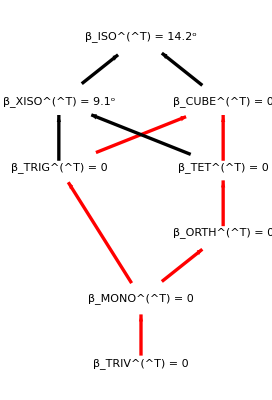

[T] = 1/36(52 | 4 | 16 | -6 | -2 √3 | 0
4 | 64 | 4 | 12 | 4 √3 | 0
16 | 4 | 52 | -6 | -2 √3 | 0
-6 | 12 | -6 | 45 | 3 √3 | 0
-2 √3 | 4 √3 | -2 √3 | 3 √3 | 39 | 0
0 | 0 | 0 | 0 | 0 | 108)

#### TRIG (Section 15.6)

```mathematica
denominator=16;
TT21TRIG=1/denominator({{4(8-√3), -8, 3 √2, -6 √2, -3 √6, 0}, {-8, 4(8+√3), 3 √2, 6 √2, -3 √6, 0}, {3 √2, 3 √2, 76, -2 √3, 12 √3, 4 √3}, {-6 √2, 6 √2, -2 √3, 24, 6, 0}, {-3 √6, -3 √6, 12 √3, 6, 52, 4}, {0, 0, 4 √3, 0, 4, 88}});
```

```mathematica
MatrixNote[TT21TRIG]="T is TT21TRIG"
MatrixShortNote[TT21TRIG]="TRIG"
PrintVoigt[TT21TRIG]
MatrixForm[N[TT21TRIG]]
```

T is TT21TRIG

TRIG

The [T]_𝔹𝔹 matrix is (1/4 (8-√3) | -1/2 | 3/(8 √2) | -3/(4 √2) | -(3 √(3/2))/8 | 0
-1/2 | 1/4 (8+√3) | 3/(8 √2) | 3/(4 √2) | -(3 √(3/2))/8 | 0
3/(8 √2) | 3/(8 √2) | 19/4 | -(√3)/8 | (3 √3)/4 | (√3)/4
-3/(4 √2) | 3/(4 √2) | -(√3)/8 | 3/2 | 3/8 | 0
-(3 √(3/2))/8 | -(3 √(3/2))/8 | (3 √3)/4 | 3/8 | 13/4 | 1/4
0 | 0 | (√3)/4 | 0 | 1/4 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/24 (75+2 √2-3 √3) | 1/24 (39+2 √2) | 1/24 (18-√2+3 √3) | 3/(16 √2) | -9/(16 √2) | 1/16 (6+2 √2+√3)
1/24 (39+2 √2) | 1/24 (75+2 √2+3 √3) | 1/24 (18-√2-3 √3) | -9/(16 √2) | 3/(16 √2) | 1/16 (6+2 √2-√3)
1/24 (18-√2+3 √3) | 1/24 (18-√2-3 √3) | 4-1/(3 √2) | 3/(8 √2) | 3/(8 √2) | 1/8 (-6+√2)
3/(16 √2) | -9/(16 √2) | 3/(8 √2) | 1-(√3)/8 | -1/4 | 3/(16 √2)
-9/(16 √2) | 3/(16 √2) | 3/(8 √2) | -1/4 | 1/8 (8+√3) | 3/(16 √2)
1/16 (6+2 √2+√3) | 1/16 (6+2 √2-√3) | 1/8 (-6+√2) | 3/(16 √2) | 3/(16 √2) | 19/8)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = √(7+(3/2+1/5 (-19/2+1/4 (-8-√3)+1/4 (-8+√3)))^2+(13/4+1/5 (-19/2+1/4 (-8-√3)+1/4 (-8+√3)))^2+(19/4+1/5 (-19/2+1/4 (-8-√3)+1/4 (-8+√3)))^2+(1/4 (8-√3)+1/5 (-19/2+1/4 (-8-√3)+1/4 (-8+√3)))^2+(1/4 (8+√3)+1/5 (-19/2+1/4 (-8-√3)+1/4 (-8+√3)))^2)   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.434 = 24.85^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, bulk modulus κ = 11/6, Poisson ratio = 28/137

(1.56699 | -0.5 | 0.265165 | -0.53033 | -0.459279 | 0.
-0.5 | 2.43301 | 0.265165 | 0.53033 | -0.459279 | 0.
0.265165 | 0.265165 | 4.75 | -0.216506 | 1.29904 | 0.433013
-0.53033 | 0.53033 | -0.216506 | 1.5 | 0.375 | 0.
-0.459279 | -0.459279 | 1.29904 | 0.375 | 3.25 | 0.25
0. | 0. | 0.433013 | 0. | 0.25 | 5.5)

#### lattice for TT21TRIG:

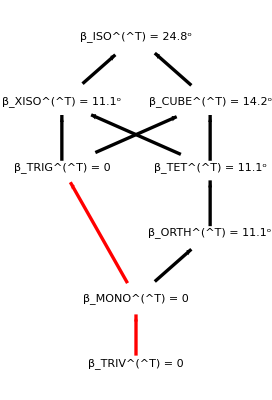

[T] = 1/16(4 (8-√3) | -8 | 3 √2 | -6 √2 | -3 √6 | 0
-8 | 4 (8+√3) | 3 √2 | 6 √2 | -3 √6 | 0
3 √2 | 3 √2 | 76 | -2 √3 | 12 √3 | 4 √3
-6 √2 | 6 √2 | -2 √3 | 24 | 6 | 0
-3 √6 | -3 √6 | 12 √3 | 6 | 52 | 4
0 | 0 | 4 √3 | 0 | 4 | 88)

#### ISO (there is no example in TT21; this is from elastic_mapping_iso.nb)

```mathematica
TT21ISO=({{3, 0, 0, 0, 0, 0}, {0, 3, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT21ISO]="T is TT21ISO"
MatrixShortNote[TT21ISO]="ISO"
PrintVoigt[TT21ISO]
MatrixForm[N[TT21ISO]]
```

T is TT21ISO

ISO

The [T]_𝔹𝔹 matrix is (3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {3,3,3,3,3,1}

The Voigt matrix is (7/3 | -2/3 | -2/3 | 0 | 0 | 0
-2/3 | 7/3 | -2/3 | 0 | 0 | 0
-2/3 | -2/3 | 7/3 | 0 | 0 | 0
0 | 0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 3/2 | 0
0 | 0 | 0 | 0 | 0 | 3/2)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 0   (Distance from T to 𝒯_ISO)

β_ISO^(□T) = 0, (Angle between T and 𝒯_ISO)

Since β_ISO^(□T) = 0, then T is assigned symmetry ISO.

Lamé parameters for T are λ = -2/3 and μ = 3/2, bulk modulus κ = 1/3, Poisson ratio = -2/5

(3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

#### lattice for TT21ISO:

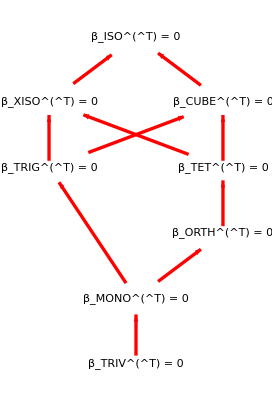

[T] = 1(3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

#### modified ISO to have a more physical Poisson parameter; here we adjust the T66 entry lam1/lam6 = (1 - 2nu) / (1 + nu) = 0.4 for nu = 0.25 lam6/lam1 = 2.5 for nu = 0.25

```mathematica
TT21ISOmod=TT21ISO;
TT21ISOmod[[6,6]]=2.5TT21ISO[[1,1]];
```

```mathematica
MatrixNote[TT21ISOmod]="T is TT21ISOmod"
MatrixShortNote[TT21ISOmod]="ISO"
PrintVoigt[TT21ISOmod]
MatrixForm[N[TT21ISOmod]]
```

T is TT21ISOmod

ISO

The [T]_𝔹𝔹 matrix is (3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 7.5)

The eigenvalues are: {7.5,3.,3.,3.,3.,3.}

The Voigt matrix is (4.5 | 1.5 | 1.5 | 0 | 0 | 0
1.5 | 4.5 | 1.5 | 0 | 0 | 0
1.5 | 1.5 | 4.5 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 0 | 0
0 | 0 | 0 | 0 | 1.5 | 0
0 | 0 | 0 | 0 | 0 | 1.5)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 0.   (Distance from T to 𝒯_ISO)

β_ISO^(□T) = 0, (Angle between T and 𝒯_ISO)

Since β_ISO^(□T) = 0, then T is assigned symmetry ISO.

Lamé parameters for T are λ = 1.5 and μ = 3/2, bulk modulus κ = 2.5, Poisson ratio = 0.25

(3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 7.5)

#### The “defeat” map of TapeTape2021, Section 15.8. (Using the minimization approach of TapeTape2022, its symmetry is identified as monoclinic.)

```mathematica
denominator=160;
TmatDefeat=1/denominator({{252, -12 √6, -52, 16 √6, -24 √2, 0}, {-12 √6, 180, 12 √6, 6, 2 √3, -32}, {-52, 12 √6, 252, 4 √6, -36 √2, 0}, {16 √6, 6, 4 √6, 211, -23 √3, -48}, {-24 √2, 2 √3, -36 √2, -23 √3, 257, -16 √3}, {0, -32, 0, -48, -16 √3, 288}});
```

```mathematica
MatrixNote[TmatDefeat]="T is Defeat"
MatrixShortNote[TmatDefeat]="Def"
PrintVoigt[TmatDefeat]
MatrixForm[N[TmatDefeat]]
```

T is Defeat

Def

The [T]_𝔹𝔹 matrix is (63/40 | -(3 √(3/2))/20 | -13/40 | (√(3/2))/5 | -3/(10 √2) | 0
-(3 √(3/2))/20 | 9/8 | (3 √(3/2))/20 | 3/80 | (√3)/80 | -1/5
-13/40 | (3 √(3/2))/20 | 63/40 | (√(3/2))/20 | -9/(20 √2) | 0
(√(3/2))/5 | 3/80 | (√(3/2))/20 | 211/160 | -(23 √3)/160 | -3/10
-3/(10 √2) | (√3)/80 | -9/(20 √2) | -(23 √3)/160 | 257/160 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 9/5)

The eigenvalues are: {2,2,2,1,1,1}

The Voigt matrix is (1/240 (401+16 √6) | 5/24-1/(5 √6) | 1/240 (-19+16 √6) | -(3 √(3/2))/20 | 1/240 (-3-8 √6) | -(√(3/2))/10
5/24-1/(5 √6) | 1/60 (83-8 √6) | 5/24-1/(5 √6) | (√(3/2))/20 | 1/120 (3-4 √6) | -(√(3/2))/20
1/240 (-19+16 √6) | 5/24-1/(5 √6) | 1/240 (401+16 √6) | (√(3/2))/10 | 1/240 (-3-8 √6) | (3 √(3/2))/20
-(3 √(3/2))/20 | (√(3/2))/20 | (√(3/2))/10 | 63/80 | -(3 √(3/2))/40 | -13/80
1/240 (-3-8 √6) | 1/120 (3-4 √6) | 1/240 (-3-8 √6) | -(3 √(3/2))/40 | 9/16 | (3 √(3/2))/40
-(√(3/2))/10 | -(√(3/2))/20 | (3 √(3/2))/20 | -13/80 | (3 √(3/2))/40 | 63/80)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = (√(174/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.31 = 17.74^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (1.44 | 0. | 0. | 0. | 0. | 0.
0. | 1.44 | 0. | 0. | 0. | 0.
0. | 0. | 1.44 | 0. | 0. | 0.
0. | 0. | 0. | 1.44 | 0. | 0.
0. | 0. | 0. | 0. | 1.44 | 0.
0. | 0. | 0. | 0. | 0. | 1.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 3/25 and μ = 18/25, bulk modulus κ = 3/5, Poisson ratio = 1/14

(1.575 | -0.183712 | -0.325 | 0.244949 | -0.212132 | 0.
-0.183712 | 1.125 | 0.183712 | 0.0375 | 0.0216506 | -0.2
-0.325 | 0.183712 | 1.575 | 0.0612372 | -0.318198 | 0.
0.244949 | 0.0375 | 0.0612372 | 1.31875 | -0.248982 | -0.3
-0.212132 | 0.0216506 | -0.318198 | -0.248982 | 1.60625 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 1.8)

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatDefeat]=Range[cmin,cmax,dc];
MaxForScaling[TmatDefeat]=cmax-dc;*)
```

#### lattice for TmatDefeat:

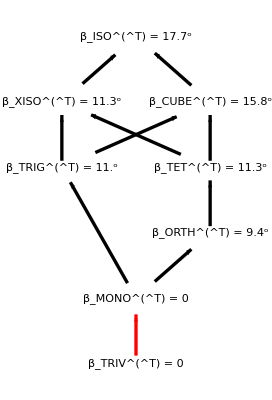

[T] = 1/160(252 | -12 √6 | -52 | 16 √6 | -24 √2 | 0
-12 √6 | 180 | 12 √6 | 6 | 2 √3 | -32
-52 | 12 √6 | 252 | 4 √6 | -36 √2 | 0
16 √6 | 6 | 4 √6 | 211 | -23 √3 | -48
-24 √2 | 2 √3 | -36 √2 | -23 √3 | 257 | -16 √3
0 | -32 | 0 | -48 | -16 √3 | 288)

## Sets of elastic maps

#### Brownlee et al. (2017) database of lower-crustal rocks

```mathematica
ifile="/Users/carltape/Downloads/CijFull_Tectonics2017.xlsx";
```

```mathematica
If[FileExistsQ[ifile],
data=Import[ifile,{"Data",1}];
headers=data[[1]];
values=data[[2;;]];
densityValues=values[[All,1]];
indexValues=Round[values[[All,2]]];
tensorValues=values[[All,3;;]];
createSymmetricMatrix[row_]:={
{row[[1]],row[[2]],row[[3]],row[[4]],row[[5]],row[[6]]},
{row[[2]],row[[7]],row[[8]],row[[9]],row[[10]],row[[11]]},{row[[3]],row[[8]],row[[12]],row[[13]],row[[14]],row[[15]]},{row[[4]],row[[9]],row[[13]],row[[16]],row[[17]],row[[18]]},{row[[5]],row[[10]],row[[14]],row[[17]],row[[19]],row[[20]]},{row[[6]],row[[11]],row[[15]],row[[18]],row[[20]],row[[21]]}};
symmetricMatrices=createSymmetricMatrix/@tensorValues;

TmatBrownlee=100.TmatOfCmat/@symmetricMatrices;  (* convert from Mbar to GPa *)

Do[
density[TmatBrownlee[[i]]]=1000.densityValues[[i]];  (* convert to kg/m3 *)
sti=ToString[indexValues[[i]]];
MatrixNote[TmatBrownlee[[i]]]="T is Brownlee"<>sti;
MatrixShortNote[TmatBrownlee[[i]]]=sti,
{i,Length[densityValues]}];

MatrixForm[TmatBrownlee[[1]]]
]
```

(83.2 | -0.04 | 1.3 | 0.43 | -0.502295 | 1.22474
-0.04 | 83.28 | 0.26 | 0.1 | -0.323316 | -1.82895
1.3 | 0.26 | 84.48 | -0.4 | 0.450333 | -0.636867
0.43 | 0.1 | -0.4 | 83.585 | 0.228053 | 1.00837
-0.502295 | -0.323316 | 0.450333 | 0.228053 | 82.9683 | 1.80784
1.22474 | -1.82895 | -0.636867 | 1.00837 | 1.80784 | 224.557)

#### TRIV maps

```mathematica
TmatallTRIV={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96,TmatBrownAn00Pert,TmatIgel,TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatBColivine,TmatBCenstatite,TmatMar17,TmatMar17mod,TmatIgel,TmatSSA2023,TmatArtsVosges,TmatVestrum,TmatFrancois,TmatFrancoisOak,TmatFrancoisBeechPert,TmatFrancoisSipoPert,TmatFrancoisVosges,TmatLokajicekWG100lp,TmatLokajicekWG100hp,TmatLokajicekWG600lp,TmatLokajicekWG600hp,TT21TRIV,TmatIsmailMainpriceTotal,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceKimberlite,TmatJi1994CastleRock,TmatJi1994AlligatorLake,TmatJi1994NunivakIsland};
Length[%]
```

37

#### Brown, Angel, Ross (2016) feldspars

```mathematica
TmatallBrown={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96};
Length[%]
```

8

#### Brown and Abramson (2016) amphiboles

```mathematica
TmatallBrownAbramson={TmatBrownAbramson2016s1,TmatBrownAbramson2016s2,TmatBrownAbramson2016s3,TmatBrownAbramson2016s4,TmatBrownAbramson2016s5,TmatBrownAbramson2016s6,TmatBrownAbramson2016s7,TmatBrownAbramson2016s8,TmatBrownAbramson2016s9};
Length[%]
```

9

#### MONO, ORTH, and higher-symmetry maps

```mathematica
TmatallMore=Join[TmatallBrownAbramson,{TmatBColivine,TmatBCenstatite,TmatRussell}];
Length[%]
```

12

#### TT24 maps (Mar17 is included in TmatallTRIV)

```mathematica
TmatallTT24={TT24MONOa,TT24MONOb,TT24ORTHa,TT24ORTHb,TT24TETa,TT24TETb};
Length[%]
```

6

#### TT21 maps

```mathematica
TmatallTT21={TT21TRIV,TT21MONO,TT21ORTH,TT24ORTHb,TT21TET,TT21XISO,TT21CUBE,TT21TRIG,TT21ISO,TmatDefeat};
Length[%]
```

10

#### measured natural Earth materials (common rocks and minerals) note: IsmailMainprice are averages

```mathematica
TmatEarth=Join[TmatBrownlee,TmatallBrown,TmatallBrownAbramson,
{TmatFrancoisVosges,TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatArtsVosges,
TmatLokajicekWG100lp,TmatLokajicekWG100hp,TmatLokajicekWG600lp,TmatLokajicekWG600hp,
TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceKimberlite,
TmatJi1994CastleRock,TmatJi1994AlligatorLake,TmatJi1994NunivakIsland}];
Length[%]
```

127

```mathematica
TmatMeasured=Join[TmatEarth,{TmatVestrum,TmatFrancois,TmatFrancoisOak,TmatFrancoisBeechPert,TmatFrancoisSipoPert}];
Length[%]
```

132

#### all maps

```mathematica
Tmatall =Join[TmatBrownlee,TmatallTRIV,TmatallMore,TmatallTT24,TmatallTT21];
```

```mathematica
Print[Length[Tmatall]]
Tmatall=DeleteCases[Tmatall,TmatBrownAn00Pert];
Tmatall=DeleteCases[Tmatall,TT21ISO];
Print[Length[Tmatall]]
```

161

159

#### 2024 Zenodo collection (Tape and Gupta) Sorted in the order shown in the table, which is descending by betaISO.

```mathematica
TmatZenodo={TmatSSA2023,TmatBrownAn00Pert,TmatIgel,TmatMar17,TmatBrownAn00,TmatFrancois,TmatMar17mod,TmatBrownAbramson2016s1,TmatBrownAn96,TmatAminzadehGrimsel0p1,TmatAminzadehBukov0p1,TmatBrownAbramson2016s9,TmatArtsVosges,TmatBColivine,TmatLokajicekWG600lp,TmatVestrum,TmatBCenstatite,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatLokajicekWG100lp,TmatIsmailMainpriceTotal,TmatIsmailMainpriceKimberlite,TmatRussell,TmatJi1994CastleRock,TmatJi1994NunivakIsland,TmatJi1994AlligatorLake,TmatLokajicekWG100hp,TmatLokajicekWG600hp};
Length[%]
```

28

```mathematica
TmatZenodoAlphabetical={TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatBCenstatite,TmatBColivine,TmatBrownAbramson2016s1,TmatBrownAbramson2016s9,TmatBrownAn00Pert,TmatBrownAn00,TmatBrownAn96,TmatFrancois,TmatIgel,TmatIsmailMainpriceKimberlite,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceTotal,TmatJi1994AlligatorLake,TmatJi1994CastleRock,TmatJi1994NunivakIsland,TmatLokajicekWG100hp,TmatLokajicekWG100lp,TmatLokajicekWG600hp,TmatLokajicekWG600lp,TmatMar17mod,TmatMar17,TmatRussell,TmatSSA2023,TmatVestrum,TmatArtsVosges};
Length[%]
```

28

## Sets of elastic maps perturbed to their extremes (these are used in ChristoffelVels.nb)

```mathematica
TmatChoose=Tmatall;stlab="All";
```

```mathematica
TmatChoose=TmatZenodo;stlab="Zendodo";
```

```mathematica
TmatChoose=TmatEarth;stlab="Earth";
```

```mathematica
(*tpertTmat[#]&/@TmatChoose *)
```

```mathematica
(*Do[Print[i,"/",Length[TmatChoose]," ",Dimensions[TmatChoose[[i]]],"  ",Tlab[TmatChoose[[i]]]],{i,1,Length[TmatChoose]}]*)
```

#### tpertTmat[Tmat_, dt_:0.01, tstart_:0, tend_:-100] is defined above

#### TmatChoosePertN: perturb T AWAY from TISO (t < 0); “N” refers to negative (t < 0)

```mathematica
TmatChoosePertN=TmatChoose;
Do[
tpertx=tpertTmat[TmatChoose[[i]]];
TmatChoosePertN[[i]]=Tpert[TmatChoose[[i]],tpertx];
density[TmatChoosePertN[[i]]]=density[TmatChoose[[i]]];
MatrixNote[TmatChoosePertN[[i]]]=MatrixNote[TmatChoose[[i]]]<>"PertN";
MatrixShortNote[TmatChoosePertN[[i]]]=MatrixShortNote[TmatChoose[[i]]]<>"pn";
Print[i,"/",Length[TmatChoose]," ",Dimensions[TmatChoose[[i]]],"  ",Tlab[TmatChoose[[i]]],"  ",tpertx];
,{i,Length[TmatChoose]}]
```

1/127 {6,6}  Brownlee1  -34.28

2/127 {6,6}  Brownlee2  -13.85

3/127 {6,6}  Brownlee3  -18.09

4/127 {6,6}  Brownlee4  -16.77

5/127 {6,6}  Brownlee5  -10.74

6/127 {6,6}  Brownlee6  -19.06

7/127 {6,6}  Brownlee9  -9.45

8/127 {6,6}  Brownlee8  -8.2

9/127 {6,6}  Brownlee9  -9.45

10/127 {6,6}  Brownlee10  -14.64

11/127 {6,6}  Brownlee11  -10.79

12/127 {6,6}  Brownlee12  -7.5

13/127 {6,6}  Brownlee13  -6.99

14/127 {6,6}  Brownlee14  -7.73

15/127 {6,6}  Brownlee15  -12.93

16/127 {6,6}  Brownlee16  -12.46

17/127 {6,6}  Brownlee17  -8.55

18/127 {6,6}  Brownlee18  -9.09

19/127 {6,6}  Brownlee19  -11.01

20/127 {6,6}  Brownlee20  -12.52

21/127 {6,6}  Brownlee21  -12.61

22/127 {6,6}  Brownlee22  -40.99

23/127 {6,6}  Brownlee23  -25.56

24/127 {6,6}  Brownlee24  -28.88

25/127 {6,6}  Brownlee25  -2.38

26/127 {6,6}  Brownlee26  -10.23

27/127 {6,6}  Brownlee27  -8.21

28/127 {6,6}  Brownlee28  -4.96

29/127 {6,6}  Brownlee29  -32.65

30/127 {6,6}  Brownlee30  -30.19

31/127 {6,6}  Brownlee31  -10.36

32/127 {6,6}  Brownlee32  -36.19

33/127 {6,6}  Brownlee33  -14.73

34/127 {6,6}  Brownlee34  -10.3

35/127 {6,6}  Brownlee35  -3.67

36/127 {6,6}  Brownlee36  -1.63

37/127 {6,6}  Brownlee37  -14.52

38/127 {6,6}  Brownlee38  -14.77

39/127 {6,6}  Brownlee39  -3.19

40/127 {6,6}  Brownlee40  -5.95

41/127 {6,6}  Brownlee41  -3.21

42/127 {6,6}  Brownlee42  -8.47

43/127 {6,6}  Brownlee43  -35.21

44/127 {6,6}  Brownlee44  -20.89

45/127 {6,6}  Brownlee45  -9.64

46/127 {6,6}  Brownlee46  -14.38

47/127 {6,6}  Brownlee47  -8.6

48/127 {6,6}  Brownlee48  -4.13

49/127 {6,6}  Brownlee49  -12.76

50/127 {6,6}  Brownlee50  -4.25

51/127 {6,6}  Brownlee51  -13.24

52/127 {6,6}  Brownlee52  -6.73

53/127 {6,6}  Brownlee53  -20.75

54/127 {6,6}  Brownlee54  -11.

55/127 {6,6}  Brownlee55  -13.91

56/127 {6,6}  Brownlee56  -14.23

57/127 {6,6}  Brownlee57  -5.61

58/127 {6,6}  Brownlee58  -13.52

59/127 {6,6}  Brownlee59  -6.42

60/127 {6,6}  Brownlee60  -4.41

61/127 {6,6}  Brownlee61  -11.21

62/127 {6,6}  Brownlee62  -12.89

63/127 {6,6}  Brownlee63  -19.48

64/127 {6,6}  Brownlee64  -12.39

65/127 {6,6}  Brownlee65  -5.14

66/127 {6,6}  Brownlee66  -16.44

67/127 {6,6}  Brownlee67  -20.72

68/127 {6,6}  Brownlee68  -26.86

69/127 {6,6}  Brownlee69  -6.93

70/127 {6,6}  Brownlee70  -8.02

71/127 {6,6}  Brownlee71  -5.92

72/127 {6,6}  Brownlee72  -7.49

73/127 {6,6}  Brownlee73  -5.67

74/127 {6,6}  Brownlee74  -25.98

75/127 {6,6}  Brownlee75  -17.38

76/127 {6,6}  Brownlee76  -14.79

77/127 {6,6}  Brownlee77  -21.12

78/127 {6,6}  Brownlee78  -18.08

79/127 {6,6}  Brownlee79  -12.68

80/127 {6,6}  Brownlee80  -26.54

81/127 {6,6}  Brownlee81  -14.76

82/127 {6,6}  Brownlee82  -16.61

83/127 {6,6}  Brownlee83  -27.62

84/127 {6,6}  Brownlee84  -10.87

85/127 {6,6}  Brownlee85  -16.4

86/127 {6,6}  Brownlee86  -8.33

87/127 {6,6}  Brownlee87  -10.51

88/127 {6,6}  Brownlee88  -5.4

89/127 {6,6}  Brownlee89  -9.63

90/127 {6,6}  Brownlee90  -9.46

91/127 {6,6}  Brownlee91  -13.25

92/127 {6,6}  Brownlee92  -6.67

93/127 {6,6}  Brownlee93  -8.79

94/127 {6,6}  Brownlee94  -13.56

95/127 {6,6}  Brownlee95  -7.58

96/127 {6,6}  Brownlee96  -8.62

97/127 {6,6}  BrownAn00  -0.66

98/127 {6,6}  BrownAn25  -0.79

99/127 {6,6}  BrownAn37  -0.84

100/127 {6,6}  BrownAn48  -0.85

101/127 {6,6}  BrownAn60  -0.91

102/127 {6,6}  BrownAn67  -0.95

103/127 {6,6}  BrownAn78  -1.08

104/127 {6,6}  BrownAn96  -1.09

105/127 {6,6}  BrownAbramson1  -1.75

106/127 {6,6}  BrownAbramson2  -1.61

107/127 {6,6}  BrownAbramson3  -1.72

108/127 {6,6}  BrownAbramson4  -1.92

109/127 {6,6}  BrownAbramson5  -1.52

110/127 {6,6}  BrownAbramson6  -1.8

111/127 {6,6}  BrownAbramson7  -1.42

112/127 {6,6}  BrownAbramson8  -1.78

113/127 {6,6}  BrownAbramson9  -2.34

114/127 {6,6}  F-Vosges-sandstone  -1.4

115/127 {6,6}  Aminzadeh-Bukov-0.1  -1.69

116/127 {6,6}  Aminzadeh-Grimsel-0.1  -1.39

117/127 {6,6}  A-Vosges-sandstone  -2.1

118/127 {6,6}  Lokajicek-WG100-lp  -8.13

119/127 {6,6}  Lokajicek-WG100-hp  -24.7

120/127 {6,6}  Lokajicek-WG600-lp  -3.06

121/127 {6,6}  Lokajicek-WG600-hp  -30.75

122/127 {6,6}  IM1998-spreading-ridge  -9.56

123/127 {6,6}  IM1998-subduction  -8.88

124/127 {6,6}  IM1998-kimberlite  -10.62

125/127 {6,6}  Ji1994-CastleRock  -14.26

126/127 {6,6}  Ji1994-AlligatorLake  -22.29

127/127 {6,6}  Ji1994-NunivakIsland  -11.38

#### TmatChoosePertP: perturb TISO AWAY from T (t > 1); “P” refers to positive (t > 1)

```mathematica
TmatChoosePertP=TmatChoose;
Do[
tpertx=tpertTmat[TmatChoose[[i]],0.01,1,100];
TmatChoosePertP[[i]]=Tpert[TmatChoose[[i]],tpertx];
density[TmatChoosePertP[[i]]]=density[TmatChoose[[i]]];
MatrixNote[TmatChoosePertP[[i]]]=MatrixNote[TmatChoose[[i]]]<>"PertP";
MatrixShortNote[TmatChoosePertP[[i]]]=MatrixShortNote[TmatChoose[[i]]]<>"pp";
Print[i,"/",Length[TmatChoose]," ",Dimensions[TmatChoose[[i]]],"  ",Tlab[TmatChoose[[i]]],"  ",tpertx];
,{i,Length[TmatChoose]}]
```

1/127 {6,6}  Brownlee1  45.99

2/127 {6,6}  Brownlee2  15.97

3/127 {6,6}  Brownlee3  18.53

4/127 {6,6}  Brownlee4  12.31

5/127 {6,6}  Brownlee5  13.87

6/127 {6,6}  Brownlee6  22.33

7/127 {6,6}  Brownlee9  13.64

8/127 {6,6}  Brownlee8  9.

9/127 {6,6}  Brownlee9  13.64

10/127 {6,6}  Brownlee10  12.68

11/127 {6,6}  Brownlee11  14.32

12/127 {6,6}  Brownlee12  9.73

13/127 {6,6}  Brownlee13  5.96

14/127 {6,6}  Brownlee14  9.33

15/127 {6,6}  Brownlee15  8.66

16/127 {6,6}  Brownlee16  11.09

17/127 {6,6}  Brownlee17  8.59

18/127 {6,6}  Brownlee18  8.71

19/127 {6,6}  Brownlee19  11.15

20/127 {6,6}  Brownlee20  15.08

21/127 {6,6}  Brownlee21  23.13

22/127 {6,6}  Brownlee22  64.86

23/127 {6,6}  Brownlee23  28.06

24/127 {6,6}  Brownlee24  34.08

25/127 {6,6}  Brownlee25  3.91

26/127 {6,6}  Brownlee26  6.29

27/127 {6,6}  Brownlee27  11.22

28/127 {6,6}  Brownlee28  5.03

29/127 {6,6}  Brownlee29  39.01

30/127 {6,6}  Brownlee30  29.62

31/127 {6,6}  Brownlee31  11.15

32/127 {6,6}  Brownlee32  27.83

33/127 {6,6}  Brownlee33  14.58

34/127 {6,6}  Brownlee34  13.15

35/127 {6,6}  Brownlee35  5.26

36/127 {6,6}  Brownlee36  3.84

37/127 {6,6}  Brownlee37  13.07

38/127 {6,6}  Brownlee38  18.81

39/127 {6,6}  Brownlee39  4.71

40/127 {6,6}  Brownlee40  6.65

41/127 {6,6}  Brownlee41  4.73

42/127 {6,6}  Brownlee42  9.56

43/127 {6,6}  Brownlee43  28.79

44/127 {6,6}  Brownlee44  17.92

45/127 {6,6}  Brownlee45  9.98

46/127 {6,6}  Brownlee46  16.59

47/127 {6,6}  Brownlee47  9.47

48/127 {6,6}  Brownlee48  5.94

49/127 {6,6}  Brownlee49  10.33

50/127 {6,6}  Brownlee50  7.02

51/127 {6,6}  Brownlee51  18.89

52/127 {6,6}  Brownlee52  10.8

53/127 {6,6}  Brownlee53  18.4

54/127 {6,6}  Brownlee54  11.23

55/127 {6,6}  Brownlee55  13.18

56/127 {6,6}  Brownlee56  14.28

57/127 {6,6}  Brownlee57  6.15

58/127 {6,6}  Brownlee58  20.56

59/127 {6,6}  Brownlee59  9.9

60/127 {6,6}  Brownlee60  5.69

61/127 {6,6}  Brownlee61  11.16

62/127 {6,6}  Brownlee62  16.21

63/127 {6,6}  Brownlee63  14.76

64/127 {6,6}  Brownlee64  9.64

65/127 {6,6}  Brownlee65  6.61

66/127 {6,6}  Brownlee66  19.83

67/127 {6,6}  Brownlee67  17.86

68/127 {6,6}  Brownlee68  19.29

69/127 {6,6}  Brownlee69  6.93

70/127 {6,6}  Brownlee70  8.73

71/127 {6,6}  Brownlee71  7.81

72/127 {6,6}  Brownlee72  9.

73/127 {6,6}  Brownlee73  7.19

74/127 {6,6}  Brownlee74  29.06

75/127 {6,6}  Brownlee75  16.92

76/127 {6,6}  Brownlee76  18.77

77/127 {6,6}  Brownlee77  16.53

78/127 {6,6}  Brownlee78  17.4

79/127 {6,6}  Brownlee79  12.35

80/127 {6,6}  Brownlee80  26.71

81/127 {6,6}  Brownlee81  12.02

82/127 {6,6}  Brownlee82  20.57

83/127 {6,6}  Brownlee83  28.85

84/127 {6,6}  Brownlee84  15.03

85/127 {6,6}  Brownlee85  17.6

86/127 {6,6}  Brownlee86  8.54

87/127 {6,6}  Brownlee87  9.78

88/127 {6,6}  Brownlee88  6.96

89/127 {6,6}  Brownlee89  11.31

90/127 {6,6}  Brownlee90  10.4

91/127 {6,6}  Brownlee91  16.94

92/127 {6,6}  Brownlee92  7.7

93/127 {6,6}  Brownlee93  11.59

94/127 {6,6}  Brownlee94  12.47

95/127 {6,6}  Brownlee95  10.18

96/127 {6,6}  Brownlee96  10.6

97/127 {6,6}  BrownAn00  1.85

98/127 {6,6}  BrownAn25  2.05

99/127 {6,6}  BrownAn37  2.01

100/127 {6,6}  BrownAn48  1.95

101/127 {6,6}  BrownAn60  2.13

102/127 {6,6}  BrownAn67  2.12

103/127 {6,6}  BrownAn78  2.16

104/127 {6,6}  BrownAn96  2.23

105/127 {6,6}  BrownAbramson1  2.93

106/127 {6,6}  BrownAbramson2  2.94

107/127 {6,6}  BrownAbramson3  3.18

108/127 {6,6}  BrownAbramson4  3.02

109/127 {6,6}  BrownAbramson5  2.91

110/127 {6,6}  BrownAbramson6  3.07

111/127 {6,6}  BrownAbramson7  2.85

112/127 {6,6}  BrownAbramson8  3.31

113/127 {6,6}  BrownAbramson9  3.42

114/127 {6,6}  F-Vosges-sandstone  3.23

115/127 {6,6}  Aminzadeh-Bukov-0.1  3.71

116/127 {6,6}  Aminzadeh-Grimsel-0.1  3.79

117/127 {6,6}  A-Vosges-sandstone  3.92

118/127 {6,6}  Lokajicek-WG100-lp  10.39

119/127 {6,6}  Lokajicek-WG100-hp  31.66

120/127 {6,6}  Lokajicek-WG600-lp  3.89

121/127 {6,6}  Lokajicek-WG600-hp  33.62

122/127 {6,6}  IM1998-spreading-ridge  7.09

123/127 {6,6}  IM1998-subduction  7.64

124/127 {6,6}  IM1998-kimberlite  10.39

125/127 {6,6}  Ji1994-CastleRock  9.1

126/127 {6,6}  Ji1994-AlligatorLake  26.6

127/127 {6,6}  Ji1994-NunivakIsland  12.05

```mathematica
TmatChooseISO=Closest[#,ISO]&/@TmatChoose;
```

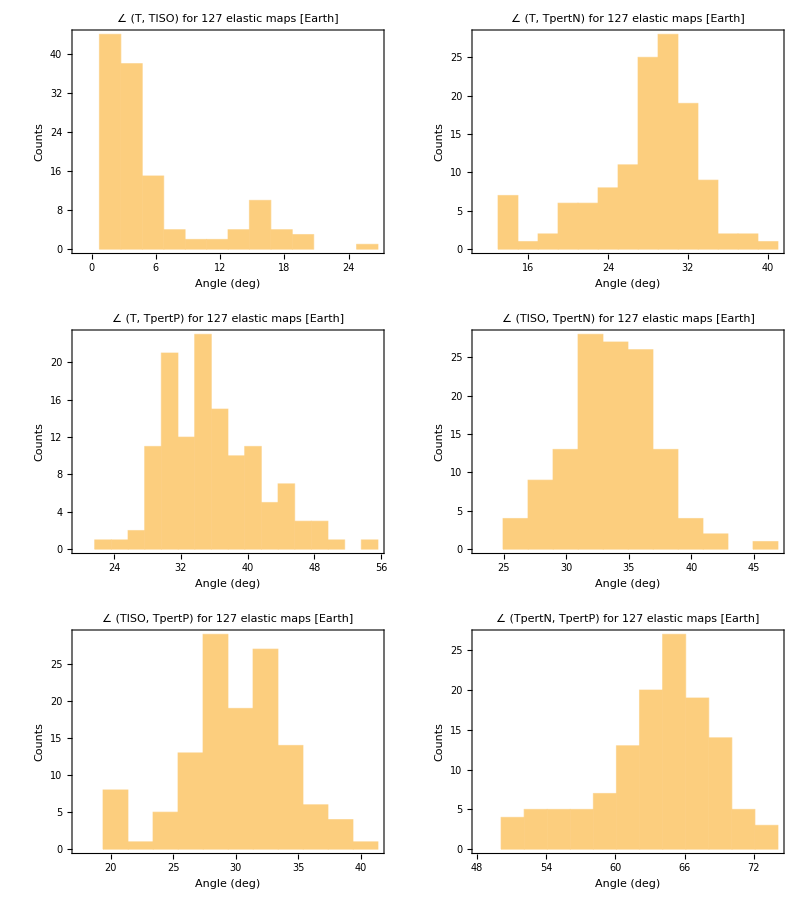

```mathematica
sets={TmatChoose,TmatChooseISO,TmatChoosePertN,TmatChoosePertP};
tlabs={"T","TISO","TpertN","TpertP"};
combinations={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}};
dwid=2;
computeAngles[setA_,setB_]:=Flatten[Table[AngleMatrix[setA[[i]],setB[[i]]]/Degree,{i,1,Length[setA]}]]
histograms=Table[Module[{angles},angles=computeAngles[sets[[combinations[[k,1]]]],sets[[combinations[[k,2]]]]];
Histogram[angles,{Min[angles]-dwid,Max[angles]+dwid,dwid},Frame->True,FrameLabel->{Style["Angle (deg)"],Style["Counts"]},PlotLabel->StringForm["∠ (`1`, `2`) for "<>ToString[Length[TmatChoose]]<>" elastic maps ["<>stlab<>"]",tlabs[[combinations[[k,1]]]],tlabs[[combinations[[k,2]]]]],ImageSize->300]],{k,Length[combinations]}];
Grid[Partition[histograms,2]]
```

```mathematica
Column[Table[stMeanMed[computeAngles[sets[[combinations[[k,1]]]],sets[[combinations[[k,2]]]]],3],{k,Length[combinations]}]]
```

Mean: 5.783 ± 5.526 Median: 3.377 ± 1.490
Mean: 27.734 ± 5.420 Median: 28.633 ± 3.006
Mean: 35.835 ± 5.810 Median: 34.790 ± 3.539
Mean: 33.518 ± 3.508 Median: 33.851 ± 2.213
Mean: 30.051 ± 4.250 Median: 30.063 ± 2.549
Mean: 63.569 ± 5.062 Median: 64.244 ± 2.802

#### check out the values for a particular map

```mathematica
angles=computeAngles[TmatChoosePertN,TmatChoosePertP];
imax=First[Flatten[Position[angles,Max[angles]]]]
MatrixNote[TmatChoose[[imax]]]
MatrixNote[TmatChoosePertN[[imax]]]
PrintVoigt[TmatChoosePertN[[imax]]]
MatrixNote[TmatChoosePertP[[imax]]]
PrintVoigt[TmatChoosePertP[[imax]]]
AngleMatrix[TmatChoosePertN[[imax]],TmatChoosePertP[[imax]]]/Degree
```

116

T is Aminzadeh-Grimsel-0.1

T is Aminzadeh-Grimsel-0.1PertN

The [T]_𝔹𝔹 matrix is (19.5086 | 3.4894 | 4.063 | 4.0869 | -0.0965907 | -1.83434
3.4894 | 5.3598 | 3.346 | -4.2064 | -3.25649 | -2.49783
4.063 | 3.346 | 34.9002 | 1.7447 | 2.88392 | -1.65871
4.0869 | -4.2064 | 1.7447 | 33.3228 | 0.883115 | -5.83477
-0.0965907 | -3.25649 | 2.88392 | 0.883115 | 19.5086 | 34.5095
-1.83434 | -2.49783 | -1.65871 | -5.83477 | 34.5095 | 67.53)

The eigenvalues are: {86.2061,38.201,33.1138,18.556,3.95407,0.0990489}

The Voigt matrix is (62.945 | 25.368 | 10.7651 | -2.8202 | 0.1434 | -0.717
25.368 | 54.4366 | 4.98127 | 1.2667 | -4.063 | 1.0277
10.7651 | 4.98127 | 2.97987 | -0.6931 | 0.8604 | -2.3422
-2.8202 | 1.2667 | -0.6931 | 9.7543 | 1.7447 | 2.0315
0.1434 | -4.063 | 0.8604 | 1.7447 | 2.6799 | 1.673
-0.717 | 1.0277 | -2.3422 | 2.0315 | 1.673 | 17.4501)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 57.0198   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.595 = 34.09^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (22.52 | 0. | 0. | 0. | 0. | 0.
0. | 22.52 | 0. | 0. | 0. | 0.
0. | 0. | 22.52 | 0. | 0. | 0.
0. | 0. | 0. | 22.52 | 0. | 0.
0. | 0. | 0. | 0. | 22.52 | 0.
0. | 0. | 0. | 0. | 0. | 67.53)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 15.0033 and μ = 11.26, bulk modulus κ = 22.51, Poisson ratio = 0.285633

T is Aminzadeh-Grimsel-0.1PertP

The [T]_𝔹𝔹 matrix is (26.0354 | -4.0734 | -4.743 | -4.7709 | 0.112757 | 2.14134
-4.0734 | 42.5522 | -3.906 | 4.9104 | 3.80151 | 2.91587
-4.743 | -3.906 | 8.0678 | -2.0367 | -3.36659 | 1.93632
-4.7709 | 4.9104 | -2.0367 | 9.9092 | -1.03092 | 6.8113
0.112757 | 3.80151 | -3.36659 | -1.03092 | 26.0354 | -40.2851
2.14134 | 2.91587 | 1.93632 | 6.8113 | -40.2851 | 67.53)

The eigenvalues are: {92.7404,45.2791,27.3681,10.4349,4.21621,0.0912779}

The Voigt matrix is (7.84703 | 2.90403 | 19.9509 | 3.2922 | -0.1674 | 0.837
2.90403 | 17.7794 | 26.7027 | -1.4787 | 4.743 | -1.1997
19.9509 | 26.7027 | 77.8481 | 0.8091 | -1.0044 | 2.7342
3.2922 | -1.4787 | 0.8091 | 13.0177 | -2.0367 | -2.3715
-0.1674 | 4.743 | -1.0044 | -2.0367 | 21.2761 | -1.953
0.837 | -1.1997 | 2.7342 | -2.3715 | -1.953 | 4.0339)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 66.5628   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.669 = 38.31^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (22.52 | 0. | 0. | 0. | 0. | 0.
0. | 22.52 | 0. | 0. | 0. | 0.
0. | 0. | 22.52 | 0. | 0. | 0.
0. | 0. | 0. | 22.52 | 0. | 0.
0. | 0. | 0. | 0. | 22.52 | 0.
0. | 0. | 0. | 0. | 0. | 67.53)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 15.0033 and μ = 11.26, bulk modulus κ = 22.51, Poisson ratio = 0.285633

72.4085